# Chaotic Signature in DNA

## Definitions

```mathematica
pGUE[s_]:=(32/Pi^2)*s^2*Exp[-(4/Pi)*s^2];
cdfGUE[s_]:=GammaRegularized[3/2,0,(4/Pi)*s^2];

pGOE[s_]:=(Pi/2)*s*Exp[-(Pi/4)*s^2];
cdfGOE[s_]:=1-Exp[-(Pi/4)*s^2];

pGSE[s_]:=(2^18/(3^6*Pi^3))*s^4*Exp[-(64/(9*Pi))*s^2];
cdfGSE[s_]:=GammaRegularized[5/2,0,(64/(9*Pi))*s^2];

pPoisson[s_]:=Exp[-s];
cdfPoisson[s_]:=1-Exp[-s];

pSP[s_]:=4*s*Exp[-2*s];
```

```mathematica
(*2. DEFINE FUNCTION TO COMPUTE r-VALUES FOR A SINGLE FILE*)
ProcessSingleFileForR[filePath_]:=Module[{importedData,rawEnergies,sortedLevels,rawSpacings,rValues},(*Import CSV as raw Data table*)importedData=Import[filePath,"Data"];
If[Length[importedData]≤1,Return[{}]];
(*Extract column 4 ("orbital_energy_hartree") and clean*)rawEnergies=ToExpression[Rest[importedData][[All,4]]];
sortedLevels=Sort[N[DeleteCases[rawEnergies,_Missing|Null|""|_String]]];
If[Length[sortedLevels]<10,Return[{}]];(*Skip files with too few levels*)(*Compute consecutive raw spacings s_i=E_{i+1}-E_i*)rawSpacings=Differences[sortedLevels];
If[Length[rawSpacings]<2,Return[{}]];
(*Compute adjacent-gap ratios r_i=Min(s_i,s_{i+1})/Max(s_i,s_{i+1})*)rValues=Table[Min[rawSpacings[[i]],rawSpacings[[i+1]]]/Max[rawSpacings[[i]],rawSpacings[[i+1]]],{i,1,Length[rawSpacings]-1}];
rValues];
```

```mathematica
sigmaPoisson[L_]:=L;
sigmaSemiPoisson[L_]:=L/2+(1-Exp[-4*L])/8;sigmaGOE[L_]:=(2/Pi^2)*(Log[2*Pi*L]+EulerGamma+1-Pi^2/8);
```

## H-Bond

### AT Done

#### Interaction Energy Done

```mathematica
SetDirectory["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\AT\\Interaction Energies"];
```

```mathematica
IntEnergydataAT=Import["output1_interaction_energies.csv"];
```

```mathematica
ColumnF=IntEnergydataAT[[All,6]];
MainIntATdata=Take[ColumnF,{2,1001}];
%//Length
```

1000

```mathematica
IntATSorted=SortBy[MainIntATdata,N];
Print[ "Maximum Value: ",Max[IntATSorted]"kJ/mol"]
Print[ "Minimum Value: ",Min[IntATSorted]"kJ/mol"]
```

Maximum Value: -0.2663 kJ/mol

Minimum Value: -67.5652 kJ/mol

```mathematica
(* Perform Spectral Unfolding via KDE *)
nTotal=Length[IntATSorted];
kdeDist=SmoothKernelDistribution[IntATSorted];

(* Compute smooth cumulative counting function N_smooth(E)*)
unfoldedLevels=Table[nTotal*CDF[kdeDist,e],{e,IntATSorted}];

(* Compute Normalized Spacings (s)*)
spacings=Differences[unfoldedLevels];
s=spacings/Mean[spacings];

(*Filter out extreme outliers for a clean plot*)
sClean=Select[s,(#>0&&#<4.0)&];
```

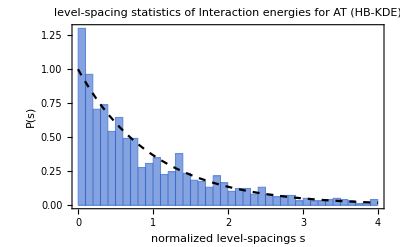

```mathematica
ATIntEnergyPlotHB=Histogram[sClean,{0.1},"PDF",ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},All},
Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacings s",10,Bold,FontFamily->"Arial",Black],Style["P(s)",10,Bold,FontFamily->"Arial",Black]},PlotLabel->Style["level-spacing statistics of Interaction energies for AT (HB-KDE)",10,Bold,FontFamily->"Arial",Darker[Blue]],Epilog->{{Darker[Black],Thickness[0.005],Dashed,Plot[pPoisson[x],{x,0,4},PlotStyle->Directive[Darker[Black],Dashed,Thick]][[1]]}}]
```

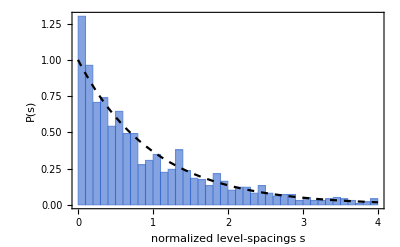

```mathematica
ATIntEnergyPlotHBNoTitle=Histogram[sClean,{0.1},"PDF",ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},All},
Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacings s",10,Bold,FontFamily->"Arial",Black],Style["P(s)",10,Bold,FontFamily->"Arial",Black]},(*PlotLabel->Style["level-spacing statistics of Interaction energies for AT (HB-KDE)",10,Bold,FontFamily->"Arial",Darker[Blue]],*)Epilog->{{Darker[Black],Thickness[0.005],Dashed,Plot[pPoisson[x],{x,0,4},PlotStyle->Directive[Darker[Black],Dashed,Thick]][[1]]}}]
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\ATIntEnergyPlotHB.png",ATIntEnergyPlotHB,ImageResolution->300];
```

#### Ground State Done

```mathematica
SetDirectory["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\AT\\Ground State\\Results of Output 1"];
```

```mathematica
GSdataAT=Import["ground_state_summary.csv"];
```

```mathematica
GSMainAT=Take[GSdataAT[[All,5]],{2,1001}];
%//Length
```

1000

```mathematica
GSMainATSorted=SortBy[GSMainAT,N];
Print[ "Maximum Value: ",Max[GSMainAT]"ev"]
Print[ "Minimum Value: ",Min[GSMainAT]"ev"]
```

Maximum Value: -25056. ev

Minimum Value: -25056.7 ev

```mathematica
(* Perform Spectral Unfolding via KDE *)
nTotal=Length[GSMainATSorted];
kdeDist=SmoothKernelDistribution[GSMainATSorted];

(* Compute smooth cumulative counting function N_smooth(E)*)
unfoldedLevels=Table[nTotal*CDF[kdeDist,e],{e,GSMainATSorted}];

(* Compute Normalized Spacings (s)*)
spacings=Differences[unfoldedLevels];
s=spacings/Mean[spacings];

(*Filter out extreme outliers for a clean plot*)
sClean=Select[s,(#>0&&#<4.0)&];
```

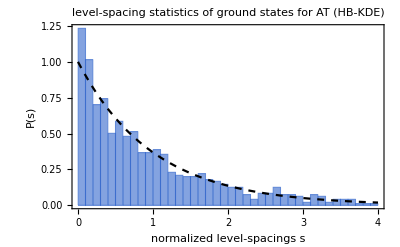

```mathematica
ATGroundStatePlotHB=Histogram[sClean,{0.1},"PDF",ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},All},
Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacings s",10,Bold,FontFamily->"Arial",Black],Style["P(s)",10,Bold,FontFamily->"Arial",Black]},PlotLabel->Style["level-spacing statistics of ground states for AT (HB-KDE)",10,Bold,FontFamily->"Arial",Darker[Blue]],Epilog->{{Darker[Black],Thickness[0.005],Dashed,Plot[pPoisson[x],{x,0,4},PlotStyle->Directive[Darker[Black],Dashed,Thick]][[1]]}}]
```

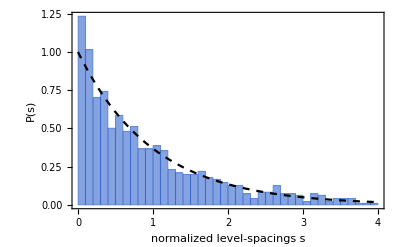

```mathematica
ATGroundStatePlotHBNoTitle=Histogram[sClean,{0.1},"PDF",ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},All},
Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacings s",10,Bold,FontFamily->"Arial",Black],Style["P(s)",10,Bold,FontFamily->"Arial",Black]},Epilog->{{Darker[Black],Thickness[0.005],Dashed,Plot[pPoisson[x],{x,0,4},PlotStyle->Directive[Darker[Black],Dashed,Thick]][[1]]}}]
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\ATGroundStatePlotHB.png",ATGroundStatePlotHB,ImageResolution->300];
```

#### Excited States (TDDFT) Done

```mathematica
directory="C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\AT\\TDDFT";
files=Sort[FileNames["*.csv",directory,Infinity]];
Length[files]
```

100

```mathematica
getEnergies[file_]:=Module[{data,energies},data=Import[file,"CSV"];
energies=Cases[Rest[data],row_List/;Length[row]≥2:>row[[2]]];
N[Cases[energies,_?NumericQ]]]
```

```mathematica
getEnergies[First[files]]
```

{4.69247,4.86559,4.93135,5.24513,5.35421,5.44901,5.46677,5.47361,5.60656,5.74522}

```mathematica
getNormalizedSpacings[file_]:=Module[{energies,spacings},energies=Sort[getEnergies[file]];
If[Length[energies]<2,Return[{}]];
spacings=Differences[energies];
If[Mean[spacings]≤0,Return[{}]];
spacings/Mean[spacings]]
```

```mathematica
getNormalizedSpacings[First[files]]
```

{1.48003,0.562218,2.68249,0.932503,0.810469,0.151768,0.0585168,1.13658,1.18543}

```mathematica
allSpacings=Flatten[getNormalizedSpacings/@files];
```

```mathematica
Length[allSpacings]
```

900

```mathematica
Mean[allSpacings]
```

1.

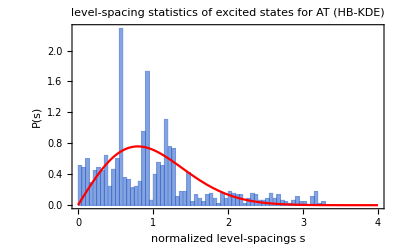

```mathematica
ATExcitedStatesPlotHB=Histogram[allSpacings,{0.05},"PDF",ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},All},
Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacings s",10,Bold,FontFamily->"Arial",Black],Style["P(s)",10,Bold,FontFamily->"Arial",Black]},PlotLabel->Style["level-spacing statistics of excited states for AT (HB-KDE)",10,Bold,FontFamily->"Arial",Darker[Blue]],Epilog->{{Darker[Black],Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]}}]
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\ATExcitedStatesPlotHB.png",ATExcitedStatesPlotHB,ImageResolution->300];
```

#### Orbital Energy Done

Gaussian KDE Unfolding

```mathematica
filePaths=FileNames["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\AT\\Orbital Energy Levels\\frame_*.csv"];
Print["Total files found: ",Length[filePaths]];
```

Total files found: 1000

```mathematica
(*DIRECTORY CONTAINING THE 1000 CSV FILES*)folder="C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\AT\\Orbital Energy Levels";

filePaths=FileNames["frame_*.csv",folder];

Print["Total files found: ",Length[filePaths]];


(*EXTRACT ALL ORBITAL ENERGIES*)

allEnergies=Flatten[Table[data=Import[file,"CSV"];
Select[Rest[data][[All,5]],NumericQ],{file,filePaths}]];


(*CALCULATE MINIMUM AND MAXIMUM*)

Print["Total orbital energies: ",Length[allEnergies]];

Print["Minimum orbital energy (eV): ",Min[allEnergies]];

Print["Maximum orbital energy (eV): ",Max[allEnergies]];
```

Total files found: 1000

Total orbital energies: 321000

Minimum orbital energy (eV): -520.099

Maximum orbital energy (eV): 106.009

```mathematica
(* DEFINE UNFOLDING& NORMALIZATION FUNCTION FOR A SINGLE FILE *)
ProcessSingleFile[filePath_]:=Module[{importedData,rawEnergies,sortedLevels,nTotal,trimCount,coreLevels,nCore,kdeDist,unfoldedLevels,spacings,meanS,normSpacings},importedData=Import[filePath,"Data"];
If[Length[importedData]≤1,Return[{}]];

(* Extract energy column *)
rawEnergies=ToExpression[Rest[importedData][[All,5]]];
sortedLevels=Sort[N[DeleteCases[rawEnergies,_Missing|Null|""|_String]]];
nTotal=Length[sortedLevels];
If[nTotal<20,Return[{}]];

(* Band-edge trimming (outer 10%)*)
trimCount=Floor[0.1*nTotal];
coreLevels=Take[sortedLevels,{trimCount+1,nTotal-trimCount}];
nCore=Length[coreLevels];
If[nCore<10,Return[{}]];

(* Gaussian KDE Unfolding *)
kdeDist=SmoothKernelDistribution[coreLevels];
unfoldedLevels=Table[nCore*CDF[kdeDist,e],{e,coreLevels}];

(* Spacings& Local Normalization *)
spacings=Differences[unfoldedLevels];
If[Length[spacings]==0,Return[{}]];
meanS=Mean[spacings];
If[meanS≤0||!NumberQ[meanS],Return[{}]];
normSpacings=spacings/meanS;

(* Filter strictly within plot range boundary *)
(*Select[normSpacings,(#>0&&#≤3.5)&]];*)
Select[normSpacings,(#>0)&]]
```

```mathematica
(* PROCESS ALL FILES IN PARALLEL AND FLATTEN *)
AllSpacingsKDE=Flatten[ParallelTable[ProcessSingleFile[file],{file,filePaths}]];

Print["Total pooled normalized spacings across all files: ",Length[AllSpacingsKDE]];
Print["Ensemble Mean Spacing: ",N[Mean[AllSpacingsKDE]]];
```

Total pooled normalized spacings across all files: 256000

Ensemble Mean Spacing: 1.

```mathematica
AllSpacingsKDE//Length
```

256000

```mathematica
Print[ "Maximum value of spacings: ",Max[AllSpacingsKDE]"ev"]
Print[ "Minimum value of spacings: ",Min[AllSpacingsKDE]"ev"]
```

Maximum value of spacings: 12.3998 ev

Minimum value of spacings: 0.000487664 ev

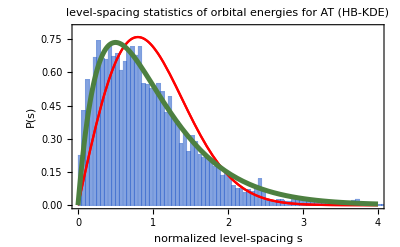

```mathematica
(* Generate Customized Plot *)
ATHBOrbEnergyKDEUnf=Histogram[AllSpacingsKDE,{0.05},"PDF",
ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},{0,0.8}},Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],
BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacing s",10,Bold,FontFamily->"Arial",Black],
Style["P(s)",10,Bold,FontFamily->"Arial",Black]},
PlotLabel->Style["level-spacing statistics of orbital energies for AT (HB-KDE)",10,Bold,FontFamily->"Arial",Darker[Blue]],Epilog->{{Red,,Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,,Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,Thickness[0.005],Plot[pSP[x],{x,0,4},PlotStyle->Directive[RGBColor[0.3,0.5,0.25],Thickness[0.009]]][[1]]}}]
```

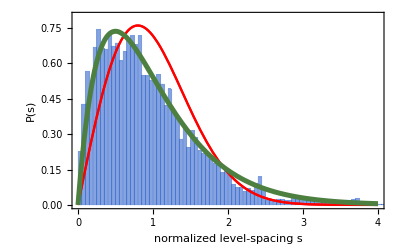

```mathematica
(* Generate Customized Plot *)
ATHBOrbEnergyKDEUnfNoTitle=Histogram[AllSpacingsKDE,{0.05},"PDF",
ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},{0,0.8}},Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],
BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacing s",10,Bold,FontFamily->"Arial",Black],
Style["P(s)",10,Bold,FontFamily->"Arial",Black]},
Epilog->{{Red,,Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,,Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,Thickness[0.005],Plot[pSP[x],{x,0,4},PlotStyle->Directive[RGBColor[0.3,0.5,0.25],Thickness[0.009]]][[1]]}}]
```

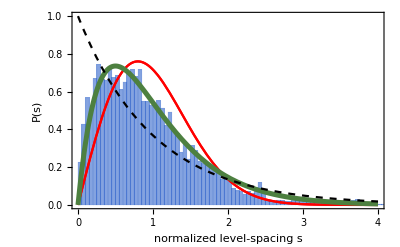

```mathematica
(* Generate Customized Plot *)
ATHBOrbEnergyKDEUnfNoTitleWithPoisson=Histogram[AllSpacingsKDE,{0.05},"PDF",
ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},{0,1}},Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],
BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacing s",10,Bold,FontFamily->"Arial",Black],
Style["P(s)",10,Bold,FontFamily->"Arial",Black]},
Epilog->{{Red,,Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,,Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,Thickness[0.005],Plot[pSP[x],{x,0,4},PlotStyle->Directive[RGBColor[0.3,0.5,0.25],Thickness[0.009]]][[1]]},{Darker[Black],Thickness[0.005],Dashed,Plot[pPoisson[x],{x,0,4},PlotStyle->Directive[Darker[Black],Dashed,Thick]][[1]]}}]
```

```mathematica
Max[HistogramList[AllSpacingsKDE,{0.05},"PDF"][[2]]]
```

0.743984

```mathematica
bins=HistogramList[AllSpacingsKDE,{0.05},"PDF"];
MaximalBy[Transpose[{MovingAverage[bins[[1]],2],bins[[2]]}],Last][[1]]
```

{0.275,0.743984}

```mathematica
NMaximize[{pGOE[x],0≤x≤3.5},x]
```

{0.760173,{x→0.797885}}

```mathematica
NMaximize[{pSP[x],0≤x≤3.5},x]
```

{0.735759,{x→0.5}}

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\ATHBOrbEnergyKDEUnf.png",ATHBOrbEnergyKDEUnf,ImageResolution->300];
```

#### Fock Matrix Eigenvalues Done

```mathematica
SetDirectory["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\AT\\Fock matrix eigenvalues"];
```

```mathematica
FMEdata=Import["multimode_unfolded_spacings.csv"];
ColumnC=FMEdata[[All,3]];
%//Length
```

253568

```mathematica
MainFMEdata=Take[ColumnC,{2,Length[ColumnC]}];
%//Length
```

253567

```mathematica
FMESorted=SortBy[MainFMEdata,N];
Print[ "Maximum Value: ",Max[FMESorted]"Hartree"]
Print[ "Minimum Value: ",Min[FMESorted]"Hartree"]
```

Maximum Value: 3.99825 Hartree

Minimum Value: 0.000398438 Hartree

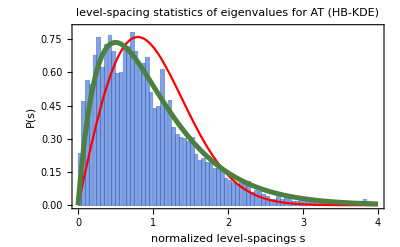

```mathematica
FMEforATPlotHB=Histogram[FMESorted,{0.05},"PDF",ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},{0,0.8}},
Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacings s",10,Bold,FontFamily->"Arial",Black],Style["P(s)",10,Bold,FontFamily->"Arial",Black]},PlotLabel->Style["level-spacing statistics of eigenvalues for AT (HB-KDE)",10,Bold,FontFamily->"Arial",Darker[Blue]],Epilog->{{Darker[Black],Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,Thickness[0.005],Plot[pSP[x],{x,0,4},PlotStyle->Directive[RGBColor[0.3,0.5,0.25],Thickness[0.009]]][[1]]}}]
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\FMEforATPlotHB.png",FMEforATPlotHB,ImageResolution->300];
```

### GC Done

#### Interaction Energy Done

```mathematica
SetDirectory["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\GC\\Interaction Energies"];
```

```mathematica
IntEnergydataGC=Import["output1_interaction_energies.csv"];
```

```mathematica
ColumnF=IntEnergydataGC[[All,6]];
MainIntGCdata=Take[ColumnF,{2,1001}];
%//Length
```

1000

```mathematica
IntGCSorted=SortBy[MainIntGCdata,N];
Print[ "Maximum Value: ",Max[IntGCSorted]"kJ/mol"]
Print[ "Minimum Value: ",Min[IntGCSorted]"kJ/mol"]
```

Maximum Value: -34.5671 kJ/mol

Minimum Value: -122.345 kJ/mol

```mathematica
(* Perform Spectral Unfolding via KDE *)
nTotal=Length[IntGCSorted];
kdeDist=SmoothKernelDistribution[IntGCSorted];

(* Compute smooth cumulative counting function N_smooth(E)*)
unfoldedLevels=Table[nTotal*CDF[kdeDist,e],{e,IntGCSorted}];

(* Compute Normalized Spacings (s)*)
spacings=Differences[unfoldedLevels];
s=spacings/Mean[spacings];

(*Filter out extreme outliers for a clean plot*)
sClean=Select[s,(#>0&&#<4.0)&];
```

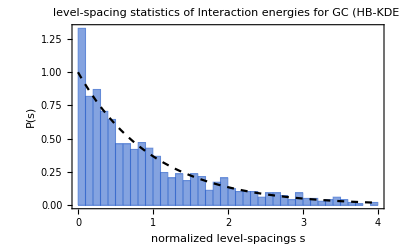

```mathematica
GCIntEnergyPlotHB=Histogram[sClean,{0.1},"PDF",ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},All},
Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],(*Change Thick to Thickness[0.005] for precise sizing*)(*3. Customize Tick Numbers (Font,Size,and Color)*)BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
(*4. Frame Labels*)FrameLabel->{Style["normalized level-spacings s",10,Bold,FontFamily->"Arial",Black],Style["P(s)",10,Bold,FontFamily->"Arial",Black]},PlotLabel->Style["level-spacing statistics of Interaction energies for GC (HB-KDE)",10,Bold,FontFamily->"Arial",Darker[Blue]],Epilog->{(*Poisson Curve (Dark Green,Dashed)*){Darker[Black],Thickness[0.005],Dashed,Plot[pPoisson[x],{x,0,4},PlotStyle->Directive[Darker[Black],Dashed,Thick]][[1]]}}]
```

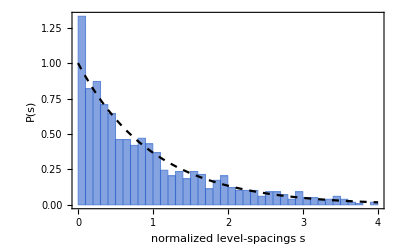

```mathematica
GCIntEnergyPlotHBNNoTitle=Histogram[sClean,{0.1},"PDF",ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},All},
Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],(*Change Thick to Thickness[0.005] for precise sizing*)(*3. Customize Tick Numbers (Font,Size,and Color)*)BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
(*4. Frame Labels*)FrameLabel->{Style["normalized level-spacings s",10,Bold,FontFamily->"Arial",Black],Style["P(s)",10,Bold,FontFamily->"Arial",Black]},Epilog->{(*Poisson Curve (Dark Green,Dashed)*){Darker[Black],Thickness[0.005],Dashed,Plot[pPoisson[x],{x,0,4},PlotStyle->Directive[Darker[Black],Dashed,Thick]][[1]]}}]
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\GCIntEnergyPlotHB.png",GCIntEnergyPlotHB,ImageResolution->300];
```

#### Ground State Done

```mathematica
SetDirectory["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\GC\\Ground States"];
```

```mathematica
GSdataGC=Import["ground_state_summary.csv"];
```

```mathematica
GSMainGC=Take[GSdataGC[[All,5]],{2,1001}];
%//Length
```

1000

```mathematica
GSMainGCSorted=SortBy[GSMainGC,N];
Print[ "Maximum Value: ",Max[GSMainGC]"ev"]
Print[ "Minimum Value: ",Min[GSMainGC]"ev"]
```

Maximum Value: -25492.1 ev

Minimum Value: -25493. ev

```mathematica
(* Perform Spectral Unfolding via KDE *)
nTotal=Length[GSMainGCSorted];
kdeDist=SmoothKernelDistribution[GSMainGCSorted];

(* Compute smooth cumulative counting function N_smooth(E)*)
unfoldedLevels=Table[nTotal*CDF[kdeDist,e],{e,GSMainGCSorted}];

(* Compute Normalized Spacings (s)*)
spacings=Differences[unfoldedLevels];
s=spacings/Mean[spacings];

(*Filter out extreme outliers for a clean plot*)
sClean=Select[s,(#>0&&#<4.0)&];
```

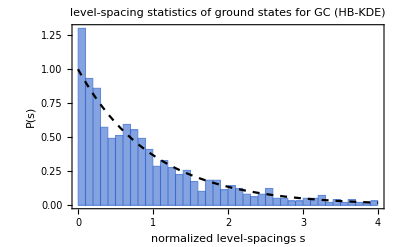

```mathematica
GCGroundStatePlotHB=Histogram[sClean,{0.1},"PDF",ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},All},
Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacings s",10,Bold,FontFamily->"Arial",Black],Style["P(s)",10,Bold,FontFamily->"Arial",Black]},PlotLabel->Style["level-spacing statistics of ground states for GC (HB-KDE)",10,Bold,FontFamily->"Arial",Darker[Blue]],Epilog->{{Darker[Black],Thickness[0.005],Dashed,Plot[pPoisson[x],{x,0,4},PlotStyle->Directive[Darker[Black],Dashed,Thick]][[1]]}}]
```

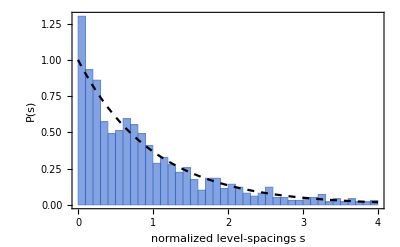

```mathematica
GCGroundStatePlotHBNoTitle=Histogram[sClean,{0.1},"PDF",ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},All},
Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacings s",10,Bold,FontFamily->"Arial",Black],Style["P(s)",10,Bold,FontFamily->"Arial",Black]},Epilog->{{Darker[Black],Thickness[0.005],Dashed,Plot[pPoisson[x],{x,0,4},PlotStyle->Directive[Darker[Black],Dashed,Thick]][[1]]}}]
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\GCGroundStatePlotHB.png",GCGroundStatePlotHB,ImageResolution->300];
```

#### Excited States (TDDFT) Done

```mathematica
directory="C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\GC\\TDDFT";
files=Sort[FileNames["*.csv",directory,Infinity]];
Length[files]
```

100

```mathematica
getEnergies[file_]:=Module[{data,energies},data=Import[file,"CSV"];
energies=Cases[Rest[data],row_List/;Length[row]≥2:>row[[2]]];
N[Cases[energies,_?NumericQ]]]
```

```mathematica
getEnergies[First[files]]
```

{3.19017,4.30357,4.4253,4.82998,4.9236,5.22139,5.27348,5.32563,5.37683,5.38047}

```mathematica
getNormalizedSpacings[file_]:=Module[{energies,spacings},energies=Sort[getEnergies[file]];
If[Length[energies]<2,Return[{}]];
spacings=Differences[energies];
If[Mean[spacings]≤0,Return[{}]];
spacings/Mean[spacings]]
```

```mathematica
getNormalizedSpacings[First[files]]
```

{4.57499,0.5002,1.66283,0.384696,1.22362,0.214041,0.214285,0.210366,0.0149621}

```mathematica
allSpacings=Flatten[getNormalizedSpacings/@files];
```

```mathematica
Length[allSpacings]
```

900

```mathematica
Mean[allSpacings]
```

1.

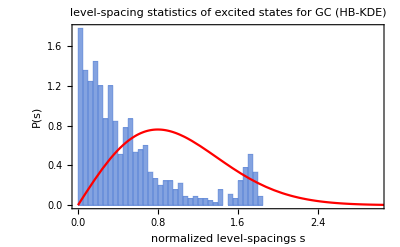

```mathematica
GCExcitedStatesPlotHB=Histogram[allSpacings,{0.05},"PDF",ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,3},All},
Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacings s",10,Bold,FontFamily->"Arial",Black],Style["P(s)",10,Bold,FontFamily->"Arial",Black]},PlotLabel->Style["level-spacing statistics of excited states for GC (HB-KDE)",10,Bold,FontFamily->"Arial",Darker[Blue]],Epilog->{{Darker[Black],Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]}}]
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\GCExcitedStatesPlotHB.png",GCExcitedStatesPlotHB,ImageResolution->300];
```

#### Orbital Energy Done

Gaussian KDE Unfolding

```mathematica
filePaths=FileNames["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\GC\\Orbital Energy Levels\\frame_*.csv"];
Print["Total files found: ",Length[filePaths]];
```

Total files found: 1000

```mathematica
(*DIRECTORY CONTAINING THE 1000 CSV FILES*)folder="C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\GC\\Orbital Energy Levels";

filePaths=FileNames["frame_*.csv",folder];

Print["Total files found: ",Length[filePaths]];


(*EXTRACT ALL ORBITAL ENERGIES*)

allEnergies=Flatten[Table[data=Import[file,"CSV"];
Select[Rest[data][[All,5]],NumericQ],{file,filePaths}]];


(*CALCULATE MINIMUM AND MAXIMUM*)

Print["Total orbital energies: ",Length[allEnergies]];

Print["Minimum orbital energy (eV): ",Min[allEnergies]];

Print["Maximum orbital energy (eV): ",Max[allEnergies]];
```

Total files found: 1000

Total orbital energies: 316000

Minimum orbital energy (eV): -520.325

Maximum orbital energy (eV): 105.866

```mathematica
(* DEFINE UNFOLDING& NORMALIZATION FUNCTION FOR A SINGLE FILE *)
ProcessSingleFile[filePath_]:=Module[{importedData,rawEnergies,sortedLevels,nTotal,trimCount,coreLevels,nCore,kdeDist,unfoldedLevels,spacings,meanS,normSpacings},importedData=Import[filePath,"Data"];
If[Length[importedData]≤1,Return[{}]];

(* Extract energy column *)
rawEnergies=ToExpression[Rest[importedData][[All,5]]];
sortedLevels=Sort[N[DeleteCases[rawEnergies,_Missing|Null|""|_String]]];
nTotal=Length[sortedLevels];
If[nTotal<20,Return[{}]];

(* Band-edge trimming (outer 10%)*)
trimCount=Floor[0.1*nTotal];
coreLevels=Take[sortedLevels,{trimCount+1,nTotal-trimCount}];
nCore=Length[coreLevels];
If[nCore<10,Return[{}]];

(* Gaussian KDE Unfolding *)
kdeDist=SmoothKernelDistribution[coreLevels];
unfoldedLevels=Table[nCore*CDF[kdeDist,e],{e,coreLevels}];

(* Spacings& Local Normalization *)
spacings=Differences[unfoldedLevels];
If[Length[spacings]==0,Return[{}]];
meanS=Mean[spacings];
If[meanS≤0||!NumberQ[meanS],Return[{}]];
normSpacings=spacings/meanS;

(* Filter strictly within plot range boundary *)
(*Select[normSpacings,(#>0&&#≤3.5)&]];*)
Select[normSpacings,(#>0)&]]
```

```mathematica
(* PROCESS ALL FILES IN PARALLEL AND FLATTEN *)
AllSpacingsKDE=Flatten[ParallelTable[ProcessSingleFile[file],{file,filePaths}]];

Print["Total pooled normalized spacings across all files: ",Length[AllSpacingsKDE]];
Print["Ensemble Mean Spacing: ",N[Mean[AllSpacingsKDE]]];
```

Total pooled normalized spacings across all files: 253000

Ensemble Mean Spacing: 1.

```mathematica
Print[ "Maximum value of spacings: ",Max[AllSpacingsKDE]"ev"]
Print[ "Minimum value of spacings: ",Min[AllSpacingsKDE]"ev"]
```

Maximum value of spacings: 9.94629 ev

Minimum value of spacings: 0.00152653 ev

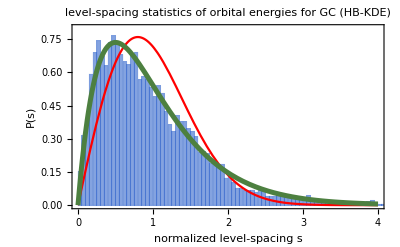

```mathematica
(* Generate Customized Plot *)
GCHBOrbEnergyKDEUnf=Histogram[AllSpacingsKDE,{0.05},"PDF",
ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},{0,0.8}},Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],
BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacing s",10,Bold,FontFamily->"Arial",Black],
Style["P(s)",10,Bold,FontFamily->"Arial",Black]},
PlotLabel->Style["level-spacing statistics of orbital energies for GC (HB-KDE)",10,Bold,FontFamily->"Arial",Darker[Blue]],Epilog->{{Red,,Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,Thickness[0.005],Plot[pSP[x],{x,0,4},PlotStyle->Directive[RGBColor[0.3,0.5,0.25],Thickness[0.009]]][[1]]}}]
```

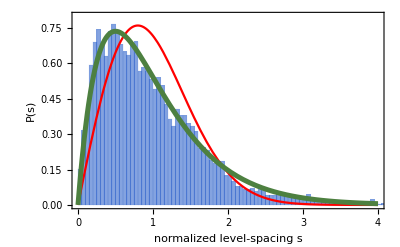

```mathematica
(* Generate Customized Plot *)
GCHBOrbEnergyKDEUnfNoTitle=Histogram[AllSpacingsKDE,{0.05},"PDF",
ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},{0,0.8}},Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],
BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacing s",10,Bold,FontFamily->"Arial",Black],
Style["P(s)",10,Bold,FontFamily->"Arial",Black]},
Epilog->{{Red,,Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,Thickness[0.005],Plot[pSP[x],{x,0,4},PlotStyle->Directive[RGBColor[0.3,0.5,0.25],Thickness[0.009]]][[1]]}}]
```

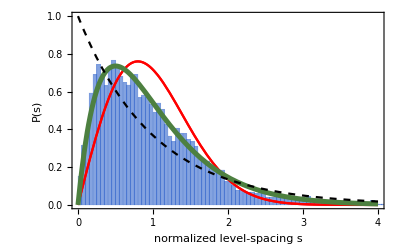

```mathematica
(* Generate Customized Plot *)
GCHBOrbEnergyKDEUnfNoTitleWithPoisson=Histogram[AllSpacingsKDE,{0.05},"PDF",
ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},{0,1}},Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],
BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacing s",10,Bold,FontFamily->"Arial",Black],
Style["P(s)",10,Bold,FontFamily->"Arial",Black]},
Epilog->{{Red,,Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,,Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,Thickness[0.005],Plot[pSP[x],{x,0,4},PlotStyle->Directive[RGBColor[0.3,0.5,0.25],Thickness[0.009]]][[1]]},{Darker[Black],Thickness[0.005],Dashed,Plot[pPoisson[x],{x,0,4},PlotStyle->Directive[Darker[Black],Dashed,Thick]][[1]]}}]
```

```mathematica
Max[HistogramList[AllSpacingsKDE,{0.05},"PDF"][[2]]]
```

0.774266

```mathematica
bins=HistogramList[AllSpacingsKDE,{0.05},"PDF"];
MaximalBy[Transpose[{MovingAverage[bins[[1]],2],bins[[2]]}],Last][[1]]
```

{0.475,0.774266}

```mathematica
NMaximize[{pGOE[x],0≤x≤3.5},x]
```

{0.760173,{x→0.797885}}

```mathematica
NMaximize[{pSP[x],0≤x≤3.5},x]
```

{0.735759,{x→0.5}}

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\GCHBOrbEnergyKDEUnf.png",GCHBOrbEnergyKDEUnf,ImageResolution->300];
```

#### Fock Matrix Eigenvalues Done

```mathematica
SetDirectory["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\GC\\Fock matrix eigenvalues"];
```

```mathematica
FMEdata=Import["multimode_unfolded_spacings.csv"];
```

```mathematica
ColumnC=FMEdata[[All,3]];
%//Length
```

251488

```mathematica
MainFMEdata=Take[ColumnC,{2,Length[ColumnC]}];
%//Length
```

251487

```mathematica
FMESorted=SortBy[MainFMEdata,N];
Print[ "Maximum Value: ",Max[FMESorted]"Hartree"]
Print[ "Minimum Value: ",Min[FMESorted]"Hartree"]
```

Maximum Value: 3.99821 Hartree

Minimum Value: 0.00155015 Hartree

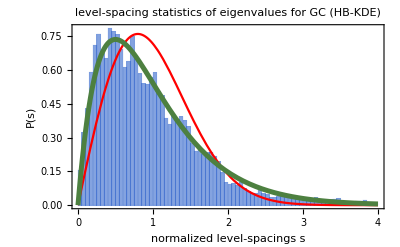

```mathematica
FMEforGCPlotHB=Histogram[FMESorted,{0.05},"PDF",ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},All},
Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacings s",10,Bold,FontFamily->"Arial",Black],Style["P(s)",10,Bold,FontFamily->"Arial",Black]},PlotLabel->Style["level-spacing statistics of eigenvalues for GC (HB-KDE)",10,Bold,FontFamily->"Arial",Darker[Blue]],Epilog->{{Darker[Black],Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,Thickness[0.005],Plot[pSP[x],{x,0,4},PlotStyle->Directive[RGBColor[0.3,0.5,0.25],Thickness[0.009]]][[1]]}}]
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\FMEforGCPlotHB.png",FMEforGCPlotHB,ImageResolution->300];
```

### Both Done

#### Interaction Energy Done

```mathematica
SetDirectory["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\AT\\Interaction Energies"];
```

```mathematica
IntEnergydataAT=Import["output1_interaction_energies.csv"];
```

```mathematica
ColumnF=IntEnergydataAT[[All,6]];
MainIntATdata=Take[ColumnF,{2,1001}];
%//Length
```

1000

```mathematica
SetDirectory["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\GC\\Interaction Energies"];
```

```mathematica
IntEnergydataGC=Import["output1_interaction_energies.csv"];
```

```mathematica
ColumnF=IntEnergydataGC[[All,6]];
MainIntGCdata=Take[ColumnF,{2,1001}];
%//Length
```

1000

```mathematica
MainIntDataBoth=SortBy[Join[MainIntATdata,MainIntGCdata],N];
%//Length
```

2000

```mathematica
(* Perform Spectral Unfolding via KDE *)
nTotal=Length[MainIntDataBoth];
kdeDist=SmoothKernelDistribution[MainIntDataBoth];

(* Compute smooth cumulative counting function N_smooth(E)*)
unfoldedLevels=Table[nTotal*CDF[kdeDist,e],{e,MainIntDataBoth}];

(* Compute Normalized Spacings (s)*)
spacings=Differences[unfoldedLevels];
s=spacings/Mean[spacings];

(*Filter out extreme outliers for a clean plot*)
sClean=Select[s,(#>0&&#<4.0)&];
```

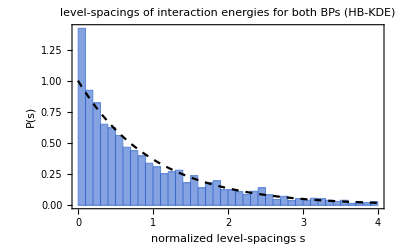

```mathematica
BothIntEnergyPlotHB=Histogram[sClean,{0.1},"PDF",ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},All},
Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacings s",10,Bold,FontFamily->"Arial",Black],Style["P(s)",10,Bold,FontFamily->"Arial",Black]},PlotLabel->Style["level-spacings of interaction energies for both BPs (HB-KDE)",10,Bold,FontFamily->"Arial",Darker[Blue]],Epilog->{{Darker[Black],Thickness[0.005],Dashed,Plot[pPoisson[x],{x,0,4},PlotStyle->Directive[Darker[Black],Dashed,Thick]][[1]]}}]
```

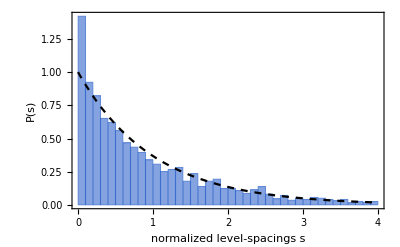

```mathematica
BothIntEnergyPlotHBNoTitle=Histogram[sClean,{0.1},"PDF",ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},All},
Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacings s",10,Bold,FontFamily->"Arial",Black],Style["P(s)",10,Bold,FontFamily->"Arial",Black]},Epilog->{{Darker[Black],Thickness[0.005],Dashed,Plot[pPoisson[x],{x,0,4},PlotStyle->Directive[Darker[Black],Dashed,Thick]][[1]]}}]
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\BothIntEnergyPlotHB.png",BothIntEnergyPlotHB,ImageResolution->300];
```

#### Ground State Done

```mathematica
SetDirectory["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\AT\\Ground State\\Results of Output 1"];
```

```mathematica
GSdataAT=Import["ground_state_summary.csv"];
```

```mathematica
GSMainAT=Take[GSdataAT[[All,5]],{2,1001}];
%//Length
```

1000

```mathematica
SetDirectory["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\GC\\Ground States"];
```

```mathematica
GSdataGC=Import["ground_state_summary.csv"];
```

```mathematica
GSMainGC=Take[GSdataGC[[All,5]],{2,1001}];
%//Length
```

1000

```mathematica
GSMainBothSorted=SortBy[Join[GSMainAT,GSMainGC],N];
%//Length
```

2000

```mathematica
(* Perform Spectral Unfolding via KDE *)
nTotal=Length[GSMainBothSorted];
kdeDist=SmoothKernelDistribution[GSMainBothSorted];

(* Compute smooth cumulative counting function N_smooth(E)*)
unfoldedLevels=Table[nTotal*CDF[kdeDist,e],{e,GSMainBothSorted}];

(* Compute Normalized Spacings (s)*)
spacings=Differences[unfoldedLevels];
s=spacings/Mean[spacings];

(*Filter out extreme outliers for a clean plot*)
sClean=Select[s,(#>0&&#<4.0)&];
```

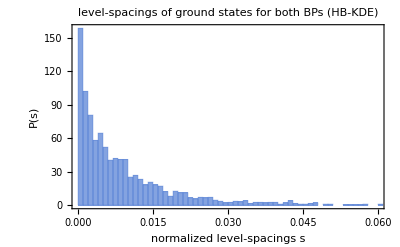

```mathematica
BothGroundStatePlotHB=Histogram[sClean,{0.001},"PDF",ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,0.06},All},
Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacings s",10,Bold,FontFamily->"Arial",Black],Style["P(s)",10,Bold,FontFamily->"Arial",Black]},PlotLabel->Style["level-spacings of ground states for both BPs (HB-KDE)",10,Bold,FontFamily->"Arial",Darker[Blue]](*,Epilog->{{Darker[Black],Thickness[0.005],Dashed,Plot[pPoisson[x],{x,0,0.6},PlotStyle->Directive[Darker[Black],Dashed,Thick]][[1]]}}*)]
```

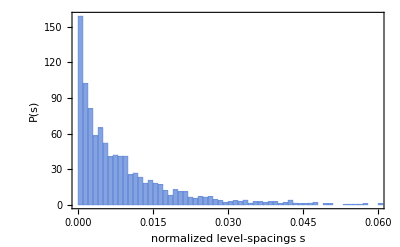

```mathematica
BothGroundStatePlotHBNoTitle=Histogram[sClean,{0.001},"PDF",ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,0.06},All},
Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacings s",10,Bold,FontFamily->"Arial",Black],Style["P(s)",10,Bold,FontFamily->"Arial",Black]}(*,Epilog->{{Darker[Black],Thickness[0.005],Dashed,Plot[pPoisson[x],{x,0,0.6},PlotStyle->Directive[Darker[Black],Dashed,Thick]][[1]]}}*)]
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\BothGroundStatePlotHB.png",BothGroundStatePlotHB,ImageResolution->300];
```

#### Excited States Done

```mathematica
directory="C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\AT\\TDDFT";
filesAT=Sort[FileNames["*.csv",directory,Infinity]];
Length[filesAT]
```

100

```mathematica
directory="C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\GC\\TDDFT";
filesGC=Sort[FileNames["*.csv",directory,Infinity]];
Length[filesGC]
```

100

```mathematica
files=Join[filesAT,filesGC];
%//Length
```

200

```mathematica
getEnergies[file_]:=Module[{data,energies},data=Import[file,"CSV"];
energies=Cases[Rest[data],row_List/;Length[row]≥2:>row[[2]]];
N[Cases[energies,_?NumericQ]]]
```

```mathematica
getEnergies[First[files]]
```

{4.69247,4.86559,4.93135,5.24513,5.35421,5.44901,5.46677,5.47361,5.60656,5.74522}

```mathematica
getNormalizedSpacings[file_]:=Module[{energies,spacings},energies=Sort[getEnergies[file]];
If[Length[energies]<2,Return[{}]];
spacings=Differences[energies];
If[Mean[spacings]≤0,Return[{}]];
spacings/Mean[spacings]]
```

```mathematica
getNormalizedSpacings[First[files]]
```

{1.48003,0.562218,2.68249,0.932503,0.810469,0.151768,0.0585168,1.13658,1.18543}

```mathematica
allSpacings=Flatten[getNormalizedSpacings/@files];
```

```mathematica
Length[allSpacings]
```

1800

```mathematica
Mean[allSpacings]
```

1.

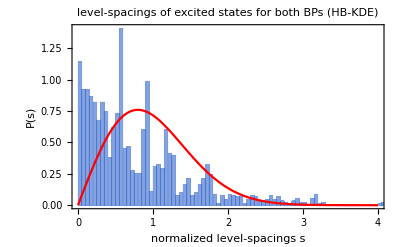

```mathematica
BothExcitedStatesPlotHB=Histogram[allSpacings,{0.05},"PDF",ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},All},
Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacings s",10,Bold,FontFamily->"Arial",Black],Style["P(s)",10,Bold,FontFamily->"Arial",Black]},PlotLabel->Style["level-spacings of excited states for both BPs (HB-KDE)",10,Bold,FontFamily->"Arial",Darker[Blue]],Epilog->{{Darker[Black],Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]}}]
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\BothExcitedStatesPlotHB.png",BothExcitedStatesPlotHB,ImageResolution->300];
```

#### Orbital Energy Done

```mathematica
filePaths1=FileNames["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\AT\\Orbital Energy Levels\\frame_*.csv"];
Print["Total files found: ",Length[filePaths1]];
```

Total files found: 1000

```mathematica
filePaths2=FileNames["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\GC\\Orbital Energy Levels\\frame_*.csv"];
Print["Total files found: ",Length[filePaths2]];
```

Total files found: 1000

```mathematica
filePaths=Join[filePaths1,filePaths2];
%//Length
```

2000

```mathematica
(* DEFINE UNFOLDING& NORMALIZATION FUNCTION FOR A SINGLE FILE *)
ProcessSingleFile[filePath_]:=Module[{importedData,rawEnergies,sortedLevels,nTotal,trimCount,coreLevels,nCore,kdeDist,unfoldedLevels,spacings,meanS,normSpacings},importedData=Import[filePath,"Data"];
If[Length[importedData]≤1,Return[{}]];

(* Extract energy column *)
rawEnergies=ToExpression[Rest[importedData][[All,5]]];
sortedLevels=Sort[N[DeleteCases[rawEnergies,_Missing|Null|""|_String]]];
nTotal=Length[sortedLevels];
If[nTotal<20,Return[{}]];

(* Band-edge trimming (outer 10%)*)
trimCount=Floor[0.1*nTotal];
coreLevels=Take[sortedLevels,{trimCount+1,nTotal-trimCount}];
nCore=Length[coreLevels];
If[nCore<10,Return[{}]];

(* Gaussian KDE Unfolding *)
kdeDist=SmoothKernelDistribution[coreLevels];
unfoldedLevels=Table[nCore*CDF[kdeDist,e],{e,coreLevels}];

(* Spacings& Local Normalization *)
spacings=Differences[unfoldedLevels];
If[Length[spacings]==0,Return[{}]];
meanS=Mean[spacings];
If[meanS≤0||!NumberQ[meanS],Return[{}]];
normSpacings=spacings/meanS;

(* Filter strictly within plot range boundary *)
Select[normSpacings,(#>0&&#≤3.5)&]];
```

```mathematica
(* PROCESS ALL FILES IN PARALLEL AND FLATTEN *)
AllSpacingsKDEBoth=Flatten[ParallelTable[ProcessSingleFile[file],{file,filePaths}]];

Print["Total pooled normalized spacings across all files: ",Length[AllSpacingsKDEBoth]];
Print["Ensemble Mean Spacing: ",N[Mean[AllSpacingsKDEBoth]]];
```

Total pooled normalized spacings across all files: 502191

Ensemble Mean Spacing: 0.931292

```mathematica
Print[ "Maximum value of spacings: ",Max[AllSpacingsKDEBoth]"ev"]
Print[ "Minimum value of spacings: ",Min[AllSpacingsKDEBoth]"ev"]
```

Maximum value of spacings: 3.49968 ev

Minimum value of spacings: 0.000487664 ev

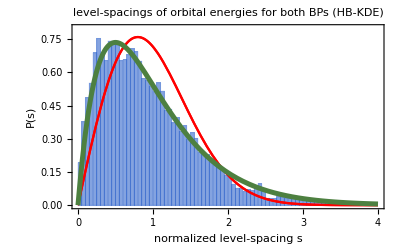

```mathematica
(* Generate Customized Plot *)
BothHBOrbEnergyKDEUnf=Histogram[AllSpacingsKDEBoth,{0.05},"PDF",
ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},{0,0.8}},Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],
BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacing s",10,Bold,FontFamily->"Arial",Black],
Style["P(s)",10,Bold,FontFamily->"Arial",Black]},
PlotLabel->Style["level-spacings of orbital energies for both BPs (HB-KDE)",10,Bold,FontFamily->"Arial",Darker[Blue]],Epilog->{{Red,,Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,,Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,Thickness[0.005],Plot[pSP[x],{x,0,4},PlotStyle->Directive[RGBColor[0.3,0.5,0.25],Thickness[0.009]]][[1]]}}]
```

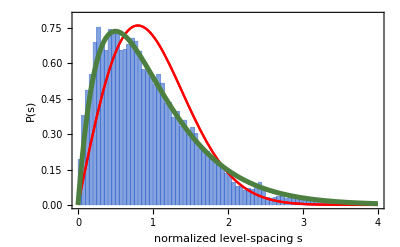

```mathematica
(* Generate Customized Plot *)
BothHBOrbEnergyKDEUnfNoTitle=Histogram[AllSpacingsKDEBoth,{0.05},"PDF",
ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},{0,0.8}},Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],
BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacing s",10,Bold,FontFamily->"Arial",Black],
Style["P(s)",10,Bold,FontFamily->"Arial",Black]},
Epilog->{{Red,,Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,,Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,Thickness[0.005],Plot[pSP[x],{x,0,4},PlotStyle->Directive[RGBColor[0.3,0.5,0.25],Thickness[0.009]]][[1]]}}]
```

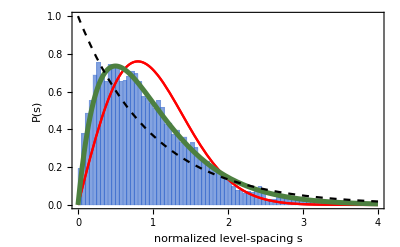

```mathematica
(* Generate Customized Plot *)
BothHBOrbEnergyKDEUnfNoTitleWithPoisson=Histogram[AllSpacingsKDEBoth,{0.05},"PDF",
ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},{0,1}},Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],
BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacing s",10,Bold,FontFamily->"Arial",Black],
Style["P(s)",10,Bold,FontFamily->"Arial",Black]},
Epilog->{{Red,,Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,,Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,Thickness[0.005],Plot[pSP[x],{x,0,4},PlotStyle->Directive[RGBColor[0.3,0.5,0.25],Thickness[0.009]]][[1]]},{Darker[Black],Thickness[0.005],Dashed,Plot[pPoisson[x],{x,0,4},PlotStyle->Directive[Darker[Black],Dashed,Thick]][[1]]}}]
```

```mathematica
(* Generate Customized Plot *)
BothHBOrbEnergyKDEUnfNoTitleWithPoisson=Histogram[AllSpacingsKDEBoth,{0.05},"PDF",
ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},{0,0.8}},Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],
BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacing s",10,Bold,FontFamily->"Arial",Black],
Style["P(s)",10,Bold,FontFamily->"Arial",Black]},
Epilog->{{Red,,Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,,Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,Thickness[0.005],Plot[pSP[x],{x,0,4},PlotStyle->Directive[RGBColor[0.3,0.5,0.25],Thickness[0.009]]][[1]]}}]
```

-Graphics-

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\BothHBOrbEnergyKDEUnf.png",BothHBOrbEnergyKDEUnf,ImageResolution->300];
```

#### Fock Matrix Eigenvalues Done

```mathematica
SetDirectory["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\AT\\Fock matrix eigenvalues"];
```

```mathematica
FMEdata=Import["multimode_unfolded_spacings.csv"];
ColumnC=FMEdata[[All,3]];
%//Length
```

253568

```mathematica
MainFMEdataAT=Take[ColumnC,{2,Length[ColumnC]}];
%//Length
```

253567

```mathematica
SetDirectory["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\GC\\Fock matrix eigenvalues"];
```

```mathematica
FMEdata=Import["multimode_unfolded_spacings.csv"];
```

```mathematica
ColumnC=FMEdata[[All,3]];
%//Length
```

251488

```mathematica
MainFMEdataGC=Take[ColumnC,{2,Length[ColumnC]}];
%//Length
```

251487

```mathematica
FMESorted=SortBy[Join[MainFMEdataAT,MainFMEdataGC],N];
Print[ "Maximum Value: ",Max[FMESorted]"Hartree"]
Print[ "Minimum Value: ",Min[FMESorted]"Hartree"]
Length[FMESorted]
```

Maximum Value: 3.99825 Hartree

Minimum Value: 0.000398438 Hartree

505054

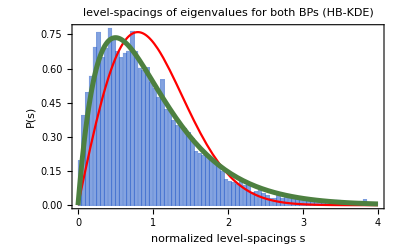

```mathematica
FMEforBothPlotHB=Histogram[FMESorted,{0.05},"PDF",ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},All},
Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacings s",10,Bold,FontFamily->"Arial",Black],Style["P(s)",10,Bold,FontFamily->"Arial",Black]},PlotLabel->Style["level-spacings of eigenvalues for both BPs (HB-KDE)",10,Bold,FontFamily->"Arial",Darker[Blue]],Epilog->{{Darker[Black],Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,Thickness[0.005],Plot[pSP[x],{x,0,4},PlotStyle->Directive[RGBColor[0.3,0.5,0.25],Thickness[0.009]]][[1]]}}]
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\FMEforBothPlotHB.png",FMEforBothPlotHB,ImageResolution->300];
```

### Export

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\ATIntEnergyPlotHB.png",ATIntEnergyPlotHB,ImageResolution->300];
Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\GCIntEnergyPlotHB.png",GCIntEnergyPlotHB,ImageResolution->300];
Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\BothIntEnergyPlotHB.png",BothIntEnergyPlotHB,ImageResolution->300];
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\ATGroundStatePlotHB.png",ATGroundStatePlotHB,ImageResolution->300];Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\GCGroundStatePlotHB.png",GCGroundStatePlotHB,ImageResolution->300];
Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\BothGroundStatePlotHB.png",BothGroundStatePlotHB,ImageResolution->300];
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\ATExcitedStatesPlotHB.png",ATExcitedStatesPlotHB,ImageResolution->300];
Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\GCExcitedStatesPlotHB.png",GCExcitedStatesPlotHB,ImageResolution->300];
Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\BothExcitedStatesPlotHB.png",BothExcitedStatesPlotHB,ImageResolution->300];
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\ATHBOrbEnergyKDEUnf.png",ATHBOrbEnergyKDEUnf,ImageResolution->300];
Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\GCHBOrbEnergyKDEUnf.png",GCHBOrbEnergyKDEUnf,ImageResolution->300];
Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\BothHBOrbEnergyKDEUnf.png",BothHBOrbEnergyKDEUnf,ImageResolution->300];
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\FMEforATPlotHB.png",FMEforATPlotHB,ImageResolution->300];
Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\FMEforGCPlotHB.png",FMEforGCPlotHB,ImageResolution->300];
Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\FMEforBothPlotHB.png",FMEforBothPlotHB,ImageResolution->300];
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\ATIntEnergyPlotHBNoTitle.png",ATIntEnergyPlotHBNoTitle,ImageResolution->300];
Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\GCIntEnergyPlotHBNNoTitle.png",GCIntEnergyPlotHBNNoTitle,ImageResolution->300];
Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\BothIntEnergyPlotHBNoTitle.png",BothIntEnergyPlotHBNoTitle,ImageResolution->300];
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\ATGroundStatePlotHBNoTitle.png",ATGroundStatePlotHBNoTitle,ImageResolution->300];Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\GCGroundStatePlotHBNoTitle.png",GCGroundStatePlotHBNoTitle,ImageResolution->300];
Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\BothGroundStatePlotHBNoTitle.png",BothGroundStatePlotHBNoTitle,ImageResolution->300];
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\ATHBOrbEnergyKDEUnfNoTitle.png",ATHBOrbEnergyKDEUnfNoTitle,ImageResolution->300];
Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\GCHBOrbEnergyKDEUnfNoTitle.png",GCHBOrbEnergyKDEUnfNoTitle,ImageResolution->300];
Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\BothHBOrbEnergyKDEUnfNoTitle.png",BothHBOrbEnergyKDEUnfNoTitle,ImageResolution->300];
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\ATHBOrbEnergyKDEUnfNoTitleWithPoisson.png",ATHBOrbEnergyKDEUnfNoTitleWithPoisson,ImageResolution->300];
Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\GCHBOrbEnergyKDEUnfNoTitleWithPoisson.png",GCHBOrbEnergyKDEUnfNoTitleWithPoisson,ImageResolution->300];
Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\BothHBOrbEnergyKDEUnfNoTitleWithPoisson.png",BothHBOrbEnergyKDEUnfNoTitleWithPoisson,ImageResolution->300];
```

## Multimode

### AT Done

#### Interaction Energy Done

```mathematica
SetDirectory["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\AT\\Interaction Energies"];
```

```mathematica
IntEnergydataAT=Import["output1_interaction_energies.csv"];
```

```mathematica
ColumnF=IntEnergydataAT[[All,6]];
MainIntATdata=Take[ColumnF,{2,1001}];
%//Length
```

1000

```mathematica
IntATSorted=SortBy[MainIntATdata,N];
Print[ "Maximum Value: ",Max[IntATSorted]"kJ/mol"]
Print[ "Minimum Value: ",Min[IntATSorted]"kJ/mol"]
```

Maximum Value: -53.6711 kJ/mol

Minimum Value: -86.5068 kJ/mol

```mathematica
(* Perform Spectral Unfolding via KDE *)
nTotal=Length[IntATSorted];
kdeDist=SmoothKernelDistribution[IntATSorted];

(* Compute smooth cumulative counting function N_smooth(E)*)
unfoldedLevels=Table[nTotal*CDF[kdeDist,e],{e,IntATSorted}];

(* Compute Normalized Spacings (s)*)
spacings=Differences[unfoldedLevels];
s=spacings/Mean[spacings];

(*Filter out extreme outliers for a clean plot*)
sClean=Select[s,(#>0&&#<4.0)&];
```

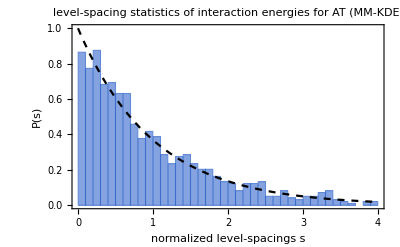

```mathematica
ATIntEnergyPlotMM=Histogram[sClean,{0.1},"PDF",ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},{0,1}},
Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacings s",10,Bold,FontFamily->"Arial",Black],Style["P(s)",10,Bold,FontFamily->"Arial",Black]},PlotLabel->Style["level-spacing statistics of interaction energies for AT (MM-KDE)",10,Bold,FontFamily->"Arial",Darker[Blue]],Epilog->{{Darker[Black],Thickness[0.005],Dashed,Plot[pPoisson[x],{x,0,4},PlotStyle->Directive[Darker[Black],Dashed,Thick]][[1]]}}]
```

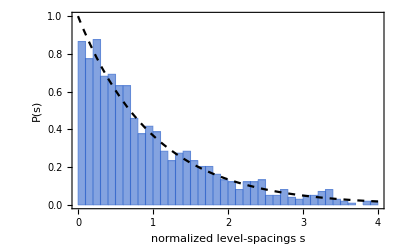

```mathematica
ATIntEnergyPlotMMNoTitle=Histogram[sClean,{0.1},"PDF",ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},{0,1}},
Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacings s",10,Bold,FontFamily->"Arial",Black],Style["P(s)",10,Bold,FontFamily->"Arial",Black]},Epilog->{{Darker[Black],Thickness[0.005],Dashed,Plot[pPoisson[x],{x,0,4},PlotStyle->Directive[Darker[Black],Dashed,Thick]][[1]]}}]
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\Final Results\\ATIntEnergyPlotMM.png",ATIntEnergyPlotMM,ImageResolution->300];
```

#### Ground State Done

```mathematica
SetDirectory["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\AT\\Ground State\\Results of Output 1"];
```

```mathematica
GSdataAT=Import["ground_state_summary.csv"];
```

```mathematica
GSMainAT=Take[GSdataAT[[All,5]],{2,1001}];
%//Length
```

1000

```mathematica
GSMainATSorted=SortBy[GSMainAT,N];
Print[ "Maximum Value: ",Max[GSMainAT]"ev"]
Print[ "Minimum Value: ",Min[GSMainAT]"ev"]
```

Maximum Value: -25055.7 ev

Minimum Value: -25056.5 ev

```mathematica
(* Perform Spectral Unfolding via KDE *)
nTotal=Length[GSMainATSorted];
kdeDist=SmoothKernelDistribution[GSMainATSorted];

(* Compute smooth cumulative counting function N_smooth(E)*)
unfoldedLevels=Table[nTotal*CDF[kdeDist,e],{e,GSMainATSorted}];

(* Compute Normalized Spacings (s)*)
spacings=Differences[unfoldedLevels];
s=spacings/Mean[spacings];

(*Filter out extreme outliers for a clean plot*)
sClean=Select[s,(#>0&&#<4.0)&];
```

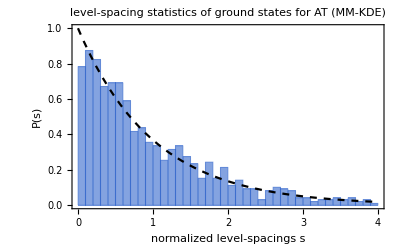

```mathematica
ATGroundStatePlotMM=Histogram[sClean,{0.1},"PDF",ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},{0,1}},
Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacings s",10,Bold,FontFamily->"Arial",Black],Style["P(s)",10,Bold,FontFamily->"Arial",Black]},PlotLabel->Style["level-spacing statistics of ground states for AT (MM-KDE)",10,Bold,FontFamily->"Arial",Darker[Blue]],Epilog->{{Darker[Black],Thickness[0.005],Dashed,Plot[pPoisson[x],{x,0,4},PlotStyle->Directive[Darker[Black],Dashed,Thick]][[1]]}}]
```

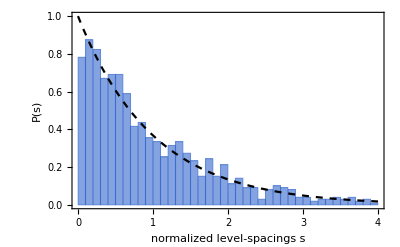

```mathematica
ATGroundStatePlotMMNoTitle=Histogram[sClean,{0.1},"PDF",ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},{0,1}},
Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacings s",10,Bold,FontFamily->"Arial",Black],Style["P(s)",10,Bold,FontFamily->"Arial",Black]},Epilog->{{Darker[Black],Thickness[0.005],Dashed,Plot[pPoisson[x],{x,0,4},PlotStyle->Directive[Darker[Black],Dashed,Thick]][[1]]}}]
```

```mathematica
Directory[]
```

C:\Users\Mehdi Ameri\Desktop\MM-Results\AT\Ground State\Results of Output 1

```mathematica
Export["ATGroundStatePlotMM.png",ATGroundStatePlotMM,ImageResolution->300];
```

#### Excited States (TDDFT) Done

```mathematica
directory="C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\AT\\TDDFT";
files=Sort[FileNames["*.csv",directory,Infinity]];
Length[files]
```

100

```mathematica
getEnergies[file_]:=Module[{data,energies},data=Import[file,"CSV"];
energies=Cases[Rest[data],row_List/;Length[row]≥2:>row[[2]]];
N[Cases[energies,_?NumericQ]]]
```

```mathematica
getEnergies[First[files]]
```

{5.01448,5.18258,5.2045,5.2833,5.4504,5.51115,5.53408,5.57785,5.78962,5.84631}

```mathematica
getNormalizedSpacings[file_]:=Module[{energies,spacings},energies=Sort[getEnergies[file]];
If[Length[energies]<2,Return[{}]];
spacings=Differences[energies];
If[Mean[spacings]≤0,Return[{}]];
spacings/Mean[spacings]]
```

```mathematica
getNormalizedSpacings[First[files]]
```

{1.8188,0.237101,0.852658,1.80785,0.65727,0.248162,0.473562,2.29122,0.613369}

```mathematica
allSpacings=Flatten[getNormalizedSpacings/@files];
```

```mathematica
Length[allSpacings]
```

900

```mathematica
Mean[allSpacings]
```

1.

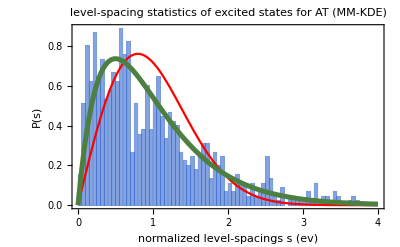

```mathematica
ATExcitedStatesPlotMM=Histogram[allSpacings,{0.05},"PDF",ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},All},
Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacings s (ev)",10,Bold,FontFamily->"Arial",Black],Style["P(s)",10,Bold,FontFamily->"Arial",Black]},PlotLabel->Style["level-spacing statistics of excited states for AT (MM-KDE)",10,Bold,FontFamily->"Arial",Darker[Blue]],Epilog->{{Darker[Black],Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,Thickness[0.005],Plot[pSP[x],{x,0,4},PlotStyle->Directive[RGBColor[0.3,0.5,0.25],Thickness[0.009]]][[1]]}}]
```

```mathematica
Directory[]
```

C:\Users\Mehdi Ameri\Desktop\MM-Results\AT\Ground State\Results of Output 1

```mathematica
Export["ATExcitedStatesPlotMM.png",ATExcitedStatesPlotMM,ImageResolution->300];
```

#### Orbital Energy Done

Gaussian KDE Unfolding

```mathematica
filePaths=FileNames["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\AT\\Orbital Energy Levels\\multimode_sample_*.csv"];
Print["Total files found: ",Length[filePaths]];
```

Total files found: 1000

```mathematica
(*DIRECTORY CONTAINING THE 1000 CSV FILES*)folder="C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\AT\\Orbital Energy Levels";

filePaths=FileNames["multimode_sample_*.csv",folder];

Print["Total files found: ",Length[filePaths]];


(*EXTRACT ALL ORBITAL ENERGIES*)

allEnergies=Flatten[Table[data=Import[file,"CSV"];
Select[Rest[data][[All,5]],NumericQ],{file,filePaths}]];


(*CALCULATE MINIMUM AND MAXIMUM*)

Print["Total orbital energies: ",Length[allEnergies]];

Print["Minimum orbital energy (eV): ",Min[allEnergies]];

Print["Maximum orbital energy (eV): ",Max[allEnergies]];
```

Total files found: 1000

Total orbital energies: 321000

Minimum orbital energy (eV): -520.548

Maximum orbital energy (eV): 105.058

```mathematica
(* DEFINE UNFOLDING& NORMALIZATION FUNCTION FOR A SINGLE FILE *)
ProcessSingleFile[filePath_]:=Module[{importedData,rawEnergies,sortedLevels,nTotal,trimCount,coreLevels,nCore,kdeDist,unfoldedLevels,spacings,meanS,normSpacings},importedData=Import[filePath,"Data"];
If[Length[importedData]≤1,Return[{}]];

(* Extract energy column *)
rawEnergies=ToExpression[Rest[importedData][[All,5]]];
sortedLevels=Sort[N[DeleteCases[rawEnergies,_Missing|Null|""|_String]]];
nTotal=Length[sortedLevels];
If[nTotal<20,Return[{}]];

(* Band-edge trimming (outer 10%)*)
trimCount=Floor[0.1*nTotal];
coreLevels=Take[sortedLevels,{trimCount+1,nTotal-trimCount}];
nCore=Length[coreLevels];
If[nCore<10,Return[{}]];

(* Gaussian KDE Unfolding *)
kdeDist=SmoothKernelDistribution[coreLevels];
unfoldedLevels=Table[nCore*CDF[kdeDist,e],{e,coreLevels}];

(* Spacings& Local Normalization *)
spacings=Differences[unfoldedLevels];
If[Length[spacings]==0,Return[{}]];
meanS=Mean[spacings];
If[meanS≤0||!NumberQ[meanS],Return[{}]];
normSpacings=spacings/meanS;

(* Filter strictly within plot range boundary *)
(*Select[normSpacings,(#>0&&#≤3.5)&]];*)
Select[normSpacings,(#>0)&]]
```

```mathematica
(* PROCESS ALL FILES IN PARALLEL AND FLATTEN *)
AllSpacingsKDE=Flatten[ParallelTable[ProcessSingleFile[file],{file,filePaths}]];

Print["Total pooled normalized spacings across all files: ",Length[AllSpacingsKDE]];
Print["Ensemble Mean Spacing: ",N[Mean[AllSpacingsKDE]]];
```

Total pooled normalized spacings across all files: 256000

Ensemble Mean Spacing: 1.

```mathematica
Print[ "Maximum value of spacings: ",Max[AllSpacingsKDE]"ev"]
Print[ "Minimum value of spacings: ",Min[AllSpacingsKDE]"ev"]
```

Maximum value of spacings: 13.4328 ev

Minimum value of spacings: 0.00101688 ev

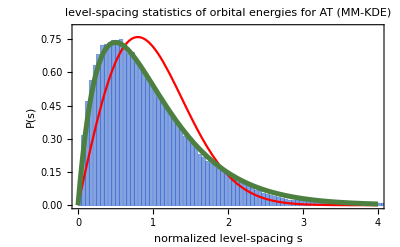

```mathematica
(* Generate Customized Plot *)
ATMMOrbEnergyKDEUnf=Histogram[AllSpacingsKDE,{0.05},"PDF",
ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},{0,0.8}},Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],
BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacing s",10,Bold,FontFamily->"Arial",Black],
Style["P(s)",10,Bold,FontFamily->"Arial",Black]},
PlotLabel->Style["level-spacing statistics of orbital energies for AT (MM-KDE)",10,Bold,FontFamily->"Arial",Darker[Blue]],Epilog->{{Red,,Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,(*Dashed,*)Thick]][[1]]},{Green,Thickness[0.005],Plot[pSP[x],{x,0,4},PlotStyle->Directive[RGBColor[0.3,0.5,0.25],Thickness[0.009]]][[1]]}}]
```

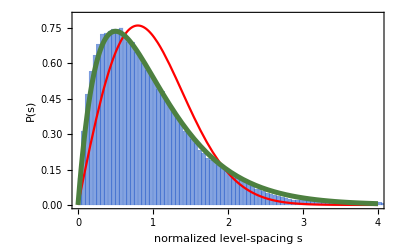

```mathematica
(* Generate Customized Plot *)
ATMMOrbEnergyKDEUnfNoTitle=Histogram[AllSpacingsKDE,{0.05},"PDF",
ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},{0,0.8}},Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],
BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacing s",10,Bold,FontFamily->"Arial",Black],
Style["P(s)",10,Bold,FontFamily->"Arial",Black]},
Epilog->{{Red,,Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,(*Dashed,*)Thick]][[1]]},{Green,Thickness[0.005],Plot[pSP[x],{x,0,4},PlotStyle->Directive[RGBColor[0.3,0.5,0.25],Thickness[0.009]]][[1]]}}]
```

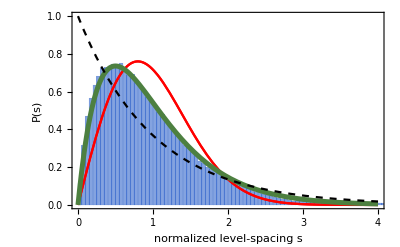

```mathematica
(* Generate Customized Plot *)
ATMMOrbEnergyKDEUnfNoTitleWithPoisson=Histogram[AllSpacingsKDE,{0.05},"PDF",
ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},{0,1}},Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],
BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacing s",10,Bold,FontFamily->"Arial",Black],
Style["P(s)",10,Bold,FontFamily->"Arial",Black]},
Epilog->{{Red,,Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,,Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,Thickness[0.005],Plot[pSP[x],{x,0,4},PlotStyle->Directive[RGBColor[0.3,0.5,0.25],Thickness[0.009]]][[1]]},{Darker[Black],Thickness[0.005],Dashed,Plot[pPoisson[x],{x,0,4},PlotStyle->Directive[Darker[Black],Dashed,Thick]][[1]]}}]
```

```mathematica
Mean[AllSpacingsKDE]
```

1.

```mathematica
Max[HistogramList[AllSpacingsKDE,{0.05},"PDF"][[2]]]
```

0.749687

```mathematica
bins=HistogramList[AllSpacingsKDE,{0.05},"PDF"];
MaximalBy[Transpose[{MovingAverage[bins[[1]],2],bins[[2]]}],Last][[1]]
```

{0.575,0.749687}

```mathematica
NMaximize[{pGOE[x],0≤x≤3.5},x]
```

{0.760173,{x→0.797885}}

```mathematica
NMaximize[{pSP[x],0≤x≤3.5},x]
```

{0.735759,{x→0.5}}

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\ATMMOrbEnergyKDEUnf.png",ATMMOrbEnergyKDEUnf,ImageResolution->300];
```

#### Fock Matrix Eigenvalues Done

```mathematica
SetDirectory["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\AT\\Fock matrix eigenvalues"];
```

```mathematica
FMEdata=Import["multimode_unfolded_spacings.csv"];
ColumnC=FMEdata[[All,3]];
%//Length
```

253514

```mathematica
MainFMEdata=Take[ColumnC,{2,Length[ColumnC]}];
%//Length
```

253513

```mathematica
FMESorted=SortBy[MainFMEdata,N];
Print[ "Maximum Value: ",Max[FMESorted]"Hartree"]
Print[ "Minimum Value: ",Min[FMESorted]"Hartree"]
```

Maximum Value: 3.99999 Hartree

Minimum Value: 0.000975601 Hartree

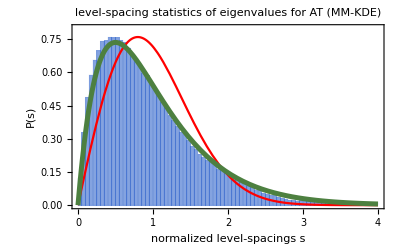

```mathematica
FMEforATPlotMM=Histogram[FMESorted,{0.05},"PDF",ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},{0,0.8}},
Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacings s",10,Bold,FontFamily->"Arial",Black],Style["P(s)",10,Bold,FontFamily->"Arial",Black]},PlotLabel->Style["level-spacing statistics of eigenvalues for AT (MM-KDE)",10,Bold,FontFamily->"Arial",Darker[Blue]],Epilog->{{Darker[Black],Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,Thickness[0.005],Plot[pSP[x],{x,0,4},PlotStyle->Directive[RGBColor[0.3,0.5,0.25],Thickness[0.009]]][[1]]}}]
```

```mathematica
SetDirectory["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\AT\\Fock matrix eigenvalues"];
```

```mathematica
Directory[]
```

C:\Users\Mehdi Ameri\Desktop\MM-Results\AT\Fock matrix eigenvalues

```mathematica
Export["FMEforATPlotMM.png",FMEforATPlotMM,ImageResolution->300];
```

### GC Done

#### Interaction Energy Done

```mathematica
SetDirectory["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\GC\\Interaction Energies"];
```

```mathematica
IntEnergydataGC=Import["output1_interaction_energies.csv"];
```

```mathematica
ColumnF=IntEnergydataAT[[All,6]];
MainIntGCdata=Take[ColumnF,{2,1001}];
%//Length
```

1000

```mathematica
IntGCSorted=SortBy[MainIntGCdata,N];
Print[ "Maximum Value: ",Max[IntGCSorted]"kJ/mol"]
Print[ "Minimum Value: ",Min[IntGCSorted]"kJ/mol"]
```

Maximum Value: -53.6711 kJ/mol

Minimum Value: -86.5068 kJ/mol

```mathematica
(* Perform Spectral Unfolding via KDE *)
nTotal=Length[IntGCSorted];
kdeDist=SmoothKernelDistribution[IntGCSorted];

(* Compute smooth cumulative counting function N_smooth(E)*)
unfoldedLevels=Table[nTotal*CDF[kdeDist,e],{e,IntGCSorted}];

(* Compute Normalized Spacings (s)*)
spacings=Differences[unfoldedLevels];
s=spacings/Mean[spacings];

(*Filter out extreme outliers for a clean plot*)
sClean=Select[s,(#>0&&#<4.0)&];
```

```mathematica
GCIntEnergyPlotMM=Histogram[sClean,{0.1},"PDF",ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},{0,1}},
Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacings s",10,Bold,FontFamily->"Arial",Black],Style["P(s)",10,Bold,FontFamily->"Arial",Black]},PlotLabel->Style["level-spacing statistics of interaction energies for AT (MM-KDE)",10,Bold,FontFamily->"Arial",Darker[Blue]],Epilog->{{Darker[Black],Thickness[0.005],Dashed,Plot[pPoisson[x],{x,0,4},PlotStyle->Directive[Darker[Black],Dashed,Thick]][[1]]}}]
```

-Graphics-

```mathematica
GCIntEnergyPlotMMNoTitle=Histogram[sClean,{0.1},"PDF",ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},{0,1}},
Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacings s",10,Bold,FontFamily->"Arial",Black],Style["P(s)",10,Bold,FontFamily->"Arial",Black]},Epilog->{{Darker[Black],Thickness[0.005],Dashed,Plot[pPoisson[x],{x,0,4},PlotStyle->Directive[Darker[Black],Dashed,Thick]][[1]]}}]
```

-Graphics-

```mathematica
Directory[]
```

C:\Users\Mehdi Ameri\Desktop\MM-Results\GC\Interaction Energies

```mathematica
Export["GCIntEnergyPlotMM.png",GCIntEnergyPlotMM,ImageResolution->300];
```

#### Ground State Done

```mathematica
SetDirectory["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\GC\\Ground State"];
```

```mathematica
GSdataAT=Import["ground_state_summary.csv"];
```

```mathematica
GSMainAT=Take[GSdataAT[[All,5]],{2,1001}];
%//Length
```

1000

```mathematica
GSMainATSorted=SortBy[GSMainAT,N];
Print[ "Maximum Value: ",Max[GSMainAT]"ev"]
Print[ "Minimum Value: ",Min[GSMainAT]"ev"]
```

Maximum Value: -25492. ev

Minimum Value: -25492.9 ev

```mathematica
(* Perform Spectral Unfolding via KDE *)
nTotal=Length[GSMainATSorted];
kdeDist=SmoothKernelDistribution[GSMainATSorted];

(* Compute smooth cumulative counting function N_smooth(E)*)
unfoldedLevels=Table[nTotal*CDF[kdeDist,e],{e,GSMainATSorted}];

(* Compute Normalized Spacings (s)*)
spacings=Differences[unfoldedLevels];
s=spacings/Mean[spacings];

(*Filter out extreme outliers for a clean plot*)
sClean=Select[s,(#>0&&#<4.0)&];
```

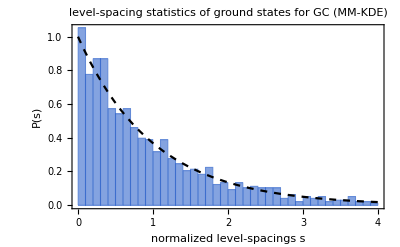

```mathematica
GCGroundStatePlotMM=Histogram[sClean,{0.1},"PDF",ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},{0,1.05}},
Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacings s",10,Bold,FontFamily->"Arial",Black],Style["P(s)",10,Bold,FontFamily->"Arial",Black]},PlotLabel->Style["level-spacing statistics of ground states for GC (MM-KDE)",10,Bold,FontFamily->"Arial",Darker[Blue]],Epilog->{{Darker[Black],Thickness[0.005],Dashed,Plot[pPoisson[x],{x,0,4},PlotStyle->Directive[Darker[Black],Dashed,Thick]][[1]]}}]
```

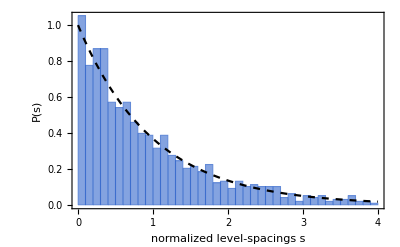

```mathematica
GCGroundStatePlotMMNoTitle=Histogram[sClean,{0.1},"PDF",ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},{0,1.05}},
Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacings s",10,Bold,FontFamily->"Arial",Black],Style["P(s)",10,Bold,FontFamily->"Arial",Black]},Epilog->{{Darker[Black],Thickness[0.005],Dashed,Plot[pPoisson[x],{x,0,4},PlotStyle->Directive[Darker[Black],Dashed,Thick]][[1]]}}]
```

```mathematica
Directory[]
```

C:\Users\Mehdi Ameri\Desktop\MM-Results\GC\Ground State

```mathematica
Export["GCGroundStatePlotMM.png",GCGroundStatePlotMM,ImageResolution->300];
```

#### Excited States (TDDFT) Done

```mathematica
directory="C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\GC\\TDDFT";
files=Sort[FileNames["*.csv",directory,Infinity]];
Length[files]
```

100

```mathematica
getEnergies[file_]:=Module[{data,energies},data=Import[file,"CSV"];
energies=Cases[Rest[data],row_List/;Length[row]≥2:>row[[2]]];
N[Cases[energies,_?NumericQ]]]
```

```mathematica
getEnergies[First[files]]
```

{3.24608,4.32009,4.43938,4.82732,4.86186,5.17093,5.18546,5.2056,5.29825,5.34659}

```mathematica
getNormalizedSpacings[file_]:=Module[{energies,spacings},energies=Sort[getEnergies[file]];
If[Length[energies]<2,Return[{}]];
spacings=Differences[energies];
If[Mean[spacings]≤0,Return[{}]];
spacings/Mean[spacings]]
```

```mathematica
getNormalizedSpacings[First[files]]
```

{4.60181,0.511099,1.6622,0.147995,1.32424,0.0622617,0.0862934,0.397007,0.207083}

```mathematica
allSpacings=Flatten[getNormalizedSpacings/@files];
```

```mathematica
Length[allSpacings]
```

900

```mathematica
Mean[allSpacings]
```

1.

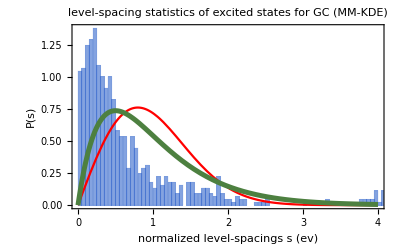

```mathematica
GCExcitedStatesPlotMM=Histogram[allSpacings,{0.05},"PDF",ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},All},
Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacings s (ev)",10,Bold,FontFamily->"Arial",Black],Style["P(s)",10,Bold,FontFamily->"Arial",Black]},PlotLabel->Style["level-spacing statistics of excited states for GC (MM-KDE)",10,Bold,FontFamily->"Arial",Darker[Blue]],Epilog->{{Darker[Black],Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,Thickness[0.005],Plot[pSP[x],{x,0,4},PlotStyle->Directive[RGBColor[0.3,0.5,0.25],Thickness[0.009]]][[1]]}}]
```

```mathematica
Directory[]
```

C:\Users\Mehdi Ameri\Desktop\MM-Results\GC\Ground State

```mathematica
Export["GCExcitedStatesPlotMM.png",GCExcitedStatesPlotMM,ImageResolution->300];
```

#### Orbital Energy Done

Gaussian KDE Unfolding

```mathematica
filePaths=FileNames["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\GC\\Orbital Energy Levels\\multimode_sample_*.csv"];
Print["Total files found: ",Length[filePaths]];
```

Total files found: 1000

```mathematica
(*DIRECTORY CONTAINING THE 1000 CSV FILES*)folder="C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\GC\\Orbital Energy Levels";

filePaths=FileNames["multimode_sample_*.csv",folder];

Print["Total files found: ",Length[filePaths]];


(*EXTRACT ALL ORBITAL ENERGIES*)

allEnergies=Flatten[Table[data=Import[file,"CSV"];
Select[Rest[data][[All,5]],NumericQ],{file,filePaths}]];


(*CALCULATE MINIMUM AND MAXIMUM*)

Print["Total orbital energies: ",Length[allEnergies]];

Print["Minimum orbital energy (eV): ",Min[allEnergies]];

Print["Maximum orbital energy (eV): ",Max[allEnergies]];
```

Total files found: 1000

Total orbital energies: 316000

Minimum orbital energy (eV): -520.555

Maximum orbital energy (eV): 104.59

```mathematica
(* DEFINE UNFOLDING& NORMALIZATION FUNCTION FOR A SINGLE FILE *)
ProcessSingleFile[filePath_]:=Module[{importedData,rawEnergies,sortedLevels,nTotal,trimCount,coreLevels,nCore,kdeDist,unfoldedLevels,spacings,meanS,normSpacings},importedData=Import[filePath,"Data"];
If[Length[importedData]≤1,Return[{}]];

(* Extract energy column *)
rawEnergies=ToExpression[Rest[importedData][[All,5]]];
sortedLevels=Sort[N[DeleteCases[rawEnergies,_Missing|Null|""|_String]]];
nTotal=Length[sortedLevels];
If[nTotal<20,Return[{}]];

(* Band-edge trimming (outer 10%)*)
trimCount=Floor[0.1*nTotal];
coreLevels=Take[sortedLevels,{trimCount+1,nTotal-trimCount}];
nCore=Length[coreLevels];
If[nCore<10,Return[{}]];

(* Gaussian KDE Unfolding *)
kdeDist=SmoothKernelDistribution[coreLevels];
unfoldedLevels=Table[nCore*CDF[kdeDist,e],{e,coreLevels}];

(* Spacings& Local Normalization *)
spacings=Differences[unfoldedLevels];
If[Length[spacings]==0,Return[{}]];
meanS=Mean[spacings];
If[meanS≤0||!NumberQ[meanS],Return[{}]];
normSpacings=spacings/meanS;

(* Filter strictly within plot range boundary *)
(*Select[normSpacings,(#>0&&#≤3.5)&]];*)
Select[normSpacings,(#>0)&]]
```

```mathematica
(* PROCESS ALL FILES IN PARALLEL AND FLATTEN *)
AllSpacingsKDE=Flatten[ParallelTable[ProcessSingleFile[file],{file,filePaths}]];

Print["Total pooled normalized spacings across all files: ",Length[AllSpacingsKDE]];
Print["Ensemble Mean Spacing: ",N[Mean[AllSpacingsKDE]]];
```

Total pooled normalized spacings across all files: 253000

Ensemble Mean Spacing: 1.

```mathematica
Print[ "Maximum value of spacings: ",Max[AllSpacingsKDE]"ev"]
Print[ "Minimum value of spacings: ",Min[AllSpacingsKDE]"ev"]
```

Maximum value of spacings: 10.3224 ev

Minimum value of spacings: 0.00101639 ev

```mathematica
ScientificForm[0.0010163876514204403]
```

1.01639×10^-3

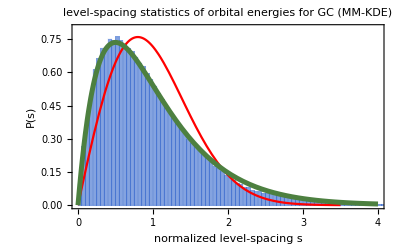

```mathematica
(* Generate Customized Plot *)
GCMMOrbEnergyKDEUnf=Histogram[AllSpacingsKDE,{0.05},"PDF",
ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},{0,0.8}},Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],
BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacing s",10,Bold,FontFamily->"Arial",Black],
Style["P(s)",10,Bold,FontFamily->"Arial",Black]},
PlotLabel->Style["level-spacing statistics of orbital energies for GC (MM-KDE)",10,Bold,FontFamily->"Arial",Darker[Blue]],Epilog->{{Red,,Thickness[0.005],Plot[pGOE[x],{x,0,3.5},PlotStyle->Directive[Red,(*Dashed,*)Thick]][[1]]},{Green,Thickness[0.005],Plot[pSP[x],{x,0,4},PlotStyle->Directive[RGBColor[0.3,0.5,0.25],Thickness[0.009]]][[1]]}}]
```

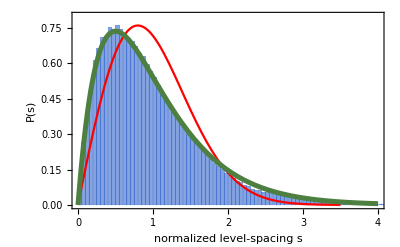

```mathematica
(* Generate Customized Plot *)
GCMMOrbEnergyKDEUnfNoTitle=Histogram[AllSpacingsKDE,{0.05},"PDF",
ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},{0,0.8}},Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],
BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacing s",10,Bold,FontFamily->"Arial",Black],
Style["P(s)",10,Bold,FontFamily->"Arial",Black]},
Epilog->{{Red,,Thickness[0.005],Plot[pGOE[x],{x,0,3.5},PlotStyle->Directive[Red,(*Dashed,*)Thick]][[1]]},{Green,Thickness[0.005],Plot[pSP[x],{x,0,4},PlotStyle->Directive[RGBColor[0.3,0.5,0.25],Thickness[0.009]]][[1]]}}]
```

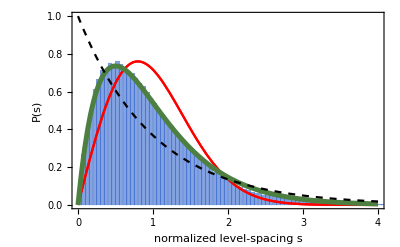

```mathematica
(* Generate Customized Plot *)
GCMMOrbEnergyKDEUnfNoTitleWithPoisson=Histogram[AllSpacingsKDE,{0.05},"PDF",
ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},{0,1}},Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],
BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacing s",10,Bold,FontFamily->"Arial",Black],
Style["P(s)",10,Bold,FontFamily->"Arial",Black]},
Epilog->{{Red,,Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,,Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,Thickness[0.005],Plot[pSP[x],{x,0,4},PlotStyle->Directive[RGBColor[0.3,0.5,0.25],Thickness[0.009]]][[1]]},{Darker[Black],Thickness[0.005],Dashed,Plot[pPoisson[x],{x,0,4},PlotStyle->Directive[Darker[Black],Dashed,Thick]][[1]]}}]
```

```mathematica
Mean[AllSpacingsKDE]
```

1.

```mathematica
ChiSquareDistribution[4]
```

ChiSquareDistribution[4]

```mathematica
Max[HistogramList[AllSpacingsKDE,{0.05},"PDF"][[2]]]
```

0.760949

```mathematica
bins=HistogramList[AllSpacingsKDE,{0.05},"PDF"];

MaximalBy[Transpose[{MovingAverage[bins[[1]],2],bins[[2]]}],Last]
```

{{0.525,0.760949}}

```mathematica
NMaximize[{pGOE[x],0≤x≤3.5},x]
```

{0.760173,{x→0.797885}}

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\GCMMOrbEnergyKDEUnf.png",GCMMOrbEnergyKDEUnf,ImageResolution->300];
```

#### Fock Matrix Eigenvalues Done

```mathematica
SetDirectory["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\GC\\Fock matrix eigenvalues"];
```

```mathematica
FMEdata=Import["multimode_unfolded_spacings.csv"];
ColumnC=FMEdata[[All,3]];
%//Length
```

251660

```mathematica
MainFMEdata=Take[ColumnC,{2,Length[ColumnC]}];
%//Length
```

251659

```mathematica
FMESorted=SortBy[MainFMEdata,N];
Print[ "Maximum Value: ",Max[FMESorted]"Hartree"]
Print[ "Minimum Value: ",Min[FMESorted]"Hartree"]
```

Maximum Value: 3.99915 Hartree

Minimum Value: 0.00100451 Hartree

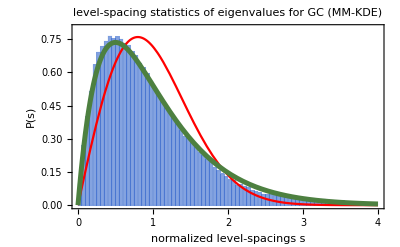

```mathematica
FMEforGCPlotMM=Histogram[FMESorted,{0.05},"PDF",ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},{0,0.8}},
Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacings s",10,Bold,FontFamily->"Arial",Black],Style["P(s)",10,Bold,FontFamily->"Arial",Black]},PlotLabel->Style["level-spacing statistics of eigenvalues for GC (MM-KDE)",10,Bold,FontFamily->"Arial",Darker[Blue]],Epilog->{{Darker[Black],Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,Thickness[0.005],Plot[pSP[x],{x,0,4},PlotStyle->Directive[RGBColor[0.3,0.5,0.25],Thickness[0.009]]][[1]]}}]
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\FMEforGCPlotMM.png",FMEforGCPlotMM,ImageResolution->300];
```

### Both Done

#### Interaction Energy Done

```mathematica
SetDirectory["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\AT\\Interaction Energies"];
```

```mathematica
IntEnergydataAT=Import["output1_interaction_energies.csv"];
```

```mathematica
ColumnF=IntEnergydataAT[[All,6]];
MainIntATdata=Take[ColumnF,{2,1001}];
%//Length
```

1000

```mathematica
SetDirectory["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\GC\\Interaction Energies"];
```

```mathematica
IntEnergydataGC=Import["output1_interaction_energies.csv"];
```

```mathematica
ColumnF=IntEnergydataGC[[All,6]];
MainIntGCdata=Take[ColumnF,{2,1001}];
%//Length
```

1000

```mathematica
MainIntDataBoth=SortBy[Join[MainIntATdata,MainIntGCdata],N];
%//Length
```

2000

```mathematica
(* Perform Spectral Unfolding via KDE *)
nTotal=Length[MainIntDataBoth];
kdeDist=SmoothKernelDistribution[MainIntDataBoth];

(* Compute smooth cumulative counting function N_smooth(E)*)
unfoldedLevels=Table[nTotal*CDF[kdeDist,e],{e,MainIntDataBoth}];

(* Compute Normalized Spacings (s)*)
spacings=Differences[unfoldedLevels];
s=spacings/Mean[spacings];

(*Filter out extreme outliers for a clean plot*)
sClean=Select[s,(#>0&&#<4.0)&];
```

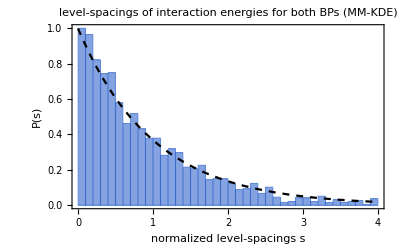

```mathematica
BothIntEnergyPlotMM=Histogram[sClean,{0.1},"PDF",ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},All},
Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacings s",10,Bold,FontFamily->"Arial",Black],Style["P(s)",10,Bold,FontFamily->"Arial",Black]},PlotLabel->Style["level-spacings of interaction energies for both BPs (MM-KDE)",10,Bold,FontFamily->"Arial",Darker[Blue]],Epilog->{{Darker[Black],Thickness[0.005],Dashed,Plot[pPoisson[x],{x,0,4},PlotStyle->Directive[Darker[Black],Dashed,Thick]][[1]]}}]
```

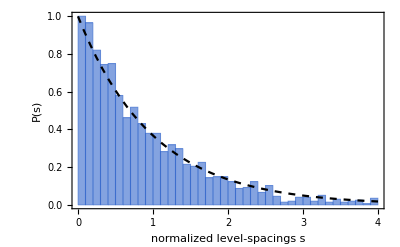

```mathematica
BothIntEnergyPlotMMNoTitle=Histogram[sClean,{0.1},"PDF",ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},All},
Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacings s",10,Bold,FontFamily->"Arial",Black],Style["P(s)",10,Bold,FontFamily->"Arial",Black]},Epilog->{{Darker[Black],Thickness[0.005],Dashed,Plot[pPoisson[x],{x,0,4},PlotStyle->Directive[Darker[Black],Dashed,Thick]][[1]]}}]
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\BothIntEnergyPlotMM.png",BothIntEnergyPlotMM,ImageResolution->300];
```

#### Ground State Done

```mathematica
SetDirectory["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\AT\\Ground State\\Results of Output 1"];
```

```mathematica
GSdataAT=Import["ground_state_summary.csv"];
```

```mathematica
GSMainAT=Take[GSdataAT[[All,5]],{2,1001}];
%//Length
```

1000

```mathematica
SetDirectory["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\GC\\Ground State"];
```

```mathematica
GSdataGC=Import["ground_state_summary.csv"];
```

```mathematica
GSMainGC=Take[GSdataGC[[All,5]],{2,1001}];
%//Length
```

1000

```mathematica
GSMainBothSorted=SortBy[Join[GSMainAT,GSMainGC],N];
%//Length
```

2000

```mathematica
(* Perform Spectral Unfolding via KDE *)
nTotal=Length[GSMainBothSorted];
kdeDist=SmoothKernelDistribution[GSMainBothSorted];

(* Compute smooth cumulative counting function N_smooth(E)*)
unfoldedLevels=Table[nTotal*CDF[kdeDist,e],{e,GSMainBothSorted}];

(* Compute Normalized Spacings (s)*)
spacings=Differences[unfoldedLevels];
s=spacings/Mean[spacings];

(*Filter out extreme outliers for a clean plot*)
sClean=Select[s,(#>0&&#<4.0)&];
```

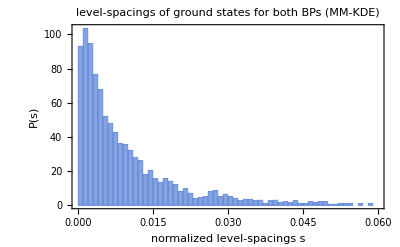

```mathematica
BothGroundStatePlotMM=Histogram[sClean,{0.001},"PDF",ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,0.06},All},
Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacings s",10,Bold,FontFamily->"Arial",Black],Style["P(s)",10,Bold,FontFamily->"Arial",Black]},PlotLabel->Style["level-spacings of ground states for both BPs (MM-KDE)",10,Bold,FontFamily->"Arial",Darker[Blue]](*,Epilog->{{Darker[Black],Thickness[0.005],Dashed,Plot[pPoisson[x],{x,0,0.6},PlotStyle->Directive[Darker[Black],Dashed,Thick]][[1]]}}*)]
```

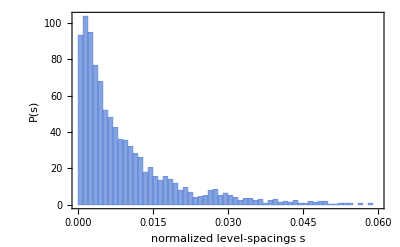

```mathematica
BothGroundStatePlotMMNoTitle=Histogram[sClean,{0.001},"PDF",ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,0.06},All},
Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacings s",10,Bold,FontFamily->"Arial",Black],Style["P(s)",10,Bold,FontFamily->"Arial",Black]}(*,Epilog->{{Darker[Black],Thickness[0.005],Dashed,Plot[pPoisson[x],{x,0,0.6},PlotStyle->Directive[Darker[Black],Dashed,Thick]][[1]]}}*)]
```

```mathematica
SetDirectory["C:\\Users\\Mehdi Ameri\\Desktop"];
```

```mathematica
Directory[]
```

C:\Users\Mehdi Ameri\Desktop

```mathematica
Export["BothGroundStatePlotMM.png",BothGroundStatePlotMM,ImageResolution->300];
```

#### Excited States Done

```mathematica
directory="C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\AT\\TDDFT";
filesAT=Sort[FileNames["*.csv",directory,Infinity]];
Length[filesAT]
```

100

```mathematica
directory="C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\GC\\TDDFT";
filesGC=Sort[FileNames["*.csv",directory,Infinity]];
Length[filesGC]
```

100

```mathematica
files=Join[filesAT,filesGC];
%//Length
```

200

```mathematica
getEnergies[file_]:=Module[{data,energies},data=Import[file,"CSV"];
energies=Cases[Rest[data],row_List/;Length[row]≥2:>row[[2]]];
N[Cases[energies,_?NumericQ]]]
```

```mathematica
getEnergies[First[files]]
```

{5.01448,5.18258,5.2045,5.2833,5.4504,5.51115,5.53408,5.57785,5.78962,5.84631}

```mathematica
getNormalizedSpacings[file_]:=Module[{energies,spacings},energies=Sort[getEnergies[file]];
If[Length[energies]<2,Return[{}]];
spacings=Differences[energies];
If[Mean[spacings]≤0,Return[{}]];
spacings/Mean[spacings]]
```

```mathematica
getNormalizedSpacings[First[files]]
```

{1.8188,0.237101,0.852658,1.80785,0.65727,0.248162,0.473562,2.29122,0.613369}

```mathematica
allSpacings=Flatten[getNormalizedSpacings/@files];
```

```mathematica
Length[allSpacings]
```

1800

```mathematica
Mean[allSpacings]
```

1.

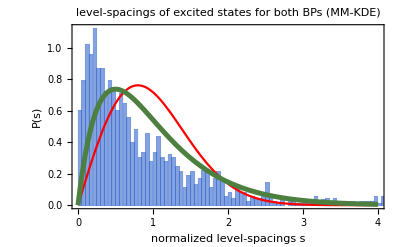

```mathematica
BothExcitedStatesPlotMM=Histogram[allSpacings,{0.05},"PDF",ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},All},
Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacings s",10,Bold,FontFamily->"Arial",Black],Style["P(s)",10,Bold,FontFamily->"Arial",Black]},PlotLabel->Style["level-spacings of excited states for both BPs (MM-KDE)",10,Bold,FontFamily->"Arial",Darker[Blue]],Epilog->{{Darker[Black],Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,Thickness[0.005],Plot[pSP[x],{x,0,4},PlotStyle->Directive[RGBColor[0.3,0.5,0.25],Thickness[0.009]]][[1]]}}]
```

#### Orbital Energy Done

```mathematica
filePaths1=FileNames["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\AT\\Orbital Energy Levels\\multimode_sample_*.csv"];
Print["Total files found: ",Length[filePaths1]];
```

Total files found: 1000

```mathematica
filePaths2=FileNames["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\GC\\Orbital Energy Levels\\multimode_sample_*.csv"];
Print["Total files found: ",Length[filePaths2]];
```

Total files found: 1000

```mathematica
filePaths=Join[filePaths1,filePaths2];
%//Length
```

2000

```mathematica
(* DEFINE UNFOLDING& NORMALIZATION FUNCTION FOR A SINGLE FILE *)
ProcessSingleFile[filePath_]:=Module[{importedData,rawEnergies,sortedLevels,nTotal,trimCount,coreLevels,nCore,kdeDist,unfoldedLevels,spacings,meanS,normSpacings},importedData=Import[filePath,"Data"];
If[Length[importedData]≤1,Return[{}]];

(* Extract energy column *)
rawEnergies=ToExpression[Rest[importedData][[All,5]]];
sortedLevels=Sort[N[DeleteCases[rawEnergies,_Missing|Null|""|_String]]];
nTotal=Length[sortedLevels];
If[nTotal<20,Return[{}]];

(* Band-edge trimming (outer 10%)*)
trimCount=Floor[0.1*nTotal];
coreLevels=Take[sortedLevels,{trimCount+1,nTotal-trimCount}];
nCore=Length[coreLevels];
If[nCore<10,Return[{}]];

(* Gaussian KDE Unfolding *)
kdeDist=SmoothKernelDistribution[coreLevels];
unfoldedLevels=Table[nCore*CDF[kdeDist,e],{e,coreLevels}];

(* Spacings& Local Normalization *)
spacings=Differences[unfoldedLevels];
If[Length[spacings]==0,Return[{}]];
meanS=Mean[spacings];
If[meanS≤0||!NumberQ[meanS],Return[{}]];
normSpacings=spacings/meanS;

(* Filter strictly within plot range boundary *)
Select[normSpacings,(#>0&&#≤3.5)&]];
```

```mathematica
(* PROCESS ALL FILES IN PARALLEL AND FLATTEN *)
AllSpacingsKDEBoth=Flatten[ParallelTable[ProcessSingleFile[file],{file,filePaths}]];

Print["Total pooled normalized spacings across all files: ",Length[AllSpacingsKDEBoth]];
Print["Ensemble Mean Spacing: ",N[Mean[AllSpacingsKDEBoth]]];
```

Total pooled normalized spacings across all files: 503175

Ensemble Mean Spacing: 0.939949

```mathematica
Print[ "Maximum value of spacings: ",Max[AllSpacingsKDEBoth]"ev"]
Print[ "Minimum value of spacings: ",Min[AllSpacingsKDEBoth]"ev"]
```

Maximum value of spacings: 3.49995 ev

Minimum value of spacings: 0.00101639 ev

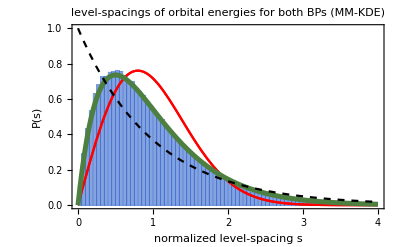

```mathematica
(* Generate Customized Plot *)
BothMMOrbEnergyKDEUnf=Histogram[AllSpacingsKDEBoth,{0.05},"PDF",
ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},{0,1}},Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],
BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacing s",10,Bold,FontFamily->"Arial",Black],
Style["P(s)",10,Bold,FontFamily->"Arial",Black]},
PlotLabel->Style["level-spacings of orbital energies for both BPs (MM-KDE)",10,Bold,FontFamily->"Arial",Darker[Blue]],Epilog->{{Red,,Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,,Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,Thickness[0.005],Plot[pSP[x],{x,0,4},PlotStyle->Directive[RGBColor[0.3,0.5,0.25],Thickness[0.009]]][[1]]},{Darker[Black],Thickness[0.005],Dashed,Plot[pPoisson[x],{x,0,4},PlotStyle->Directive[Darker[Black],Dashed,Thick]][[1]]}}]
```

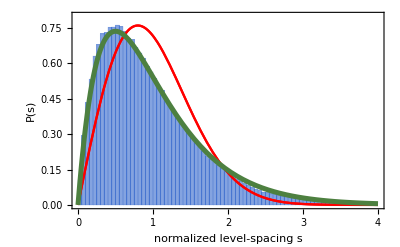

```mathematica
(* Generate Customized Plot *)
BothMMOrbEnergyKDEUnfNoTitle=Histogram[AllSpacingsKDEBoth,{0.05},"PDF",
ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},{0,0.8}},Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],
BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacing s",10,Bold,FontFamily->"Arial",Black],
Style["P(s)",10,Bold,FontFamily->"Arial",Black]},Epilog->{{Red,,Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Red,,Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,Thickness[0.005],Plot[pSP[x],{x,0,4},PlotStyle->Directive[RGBColor[0.3,0.5,0.25],Thickness[0.009]]][[1]]}}]
```

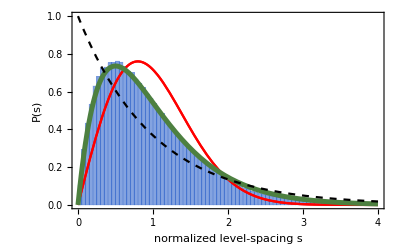

```mathematica
(* Generate Customized Plot *)
BothMMOrbEnergyKDEUnfNoTitleWithPoisson=Histogram[AllSpacingsKDEBoth,{0.05},"PDF",
ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},{0,1}},Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],
BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacing s",10,Bold,FontFamily->"Arial",Black],
Style["P(s)",10,Bold,FontFamily->"Arial",Black]},
Epilog->{{Red,,Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,,Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,Thickness[0.005],Plot[pSP[x],{x,0,4},PlotStyle->Directive[RGBColor[0.3,0.5,0.25],Thickness[0.009]]][[1]]},{Darker[Black],Thickness[0.005],Dashed,Plot[pPoisson[x],{x,0,4},PlotStyle->Directive[Darker[Black],Dashed,Thick]][[1]]}}]
```

```mathematica
SetDirectory["C:\\Users\\Mehdi Ameri\\Desktop"];
```

```mathematica
Export["BothMMOrbEnergyKDEUnf.png",BothMMOrbEnergyKDEUnf,ImageResolution->300];
```

#### Fock Matrix Eigenvalues Done

```mathematica
SetDirectory["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\AT\\Fock matrix eigenvalues"];
```

```mathematica
FMEdata=Import["multimode_unfolded_spacings.csv"];
ColumnC=FMEdata[[All,3]];
%//Length
```

253514

```mathematica
MainFMEdataAT=Take[ColumnC,{2,Length[ColumnC]}];
%//Length
```

253513

```mathematica
SetDirectory["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\GC\\Fock matrix eigenvalues"];
```

```mathematica
FMEdata=Import["multimode_unfolded_spacings.csv"];
```

```mathematica
ColumnC=FMEdata[[All,3]];
%//Length
```

251660

```mathematica
MainFMEdataGC=Take[ColumnC,{2,Length[ColumnC]}];
%//Length
```

251659

```mathematica
FMESorted=SortBy[Join[MainFMEdataAT,MainFMEdataGC],N];
Print[ "Maximum Value: ",Max[FMESorted]"Hartree"]
Print[ "Minimum Value: ",Min[FMESorted]"Hartree"]
Length[FMESorted]
```

Maximum Value: 3.99999 Hartree

Minimum Value: 0.000975601 Hartree

505172

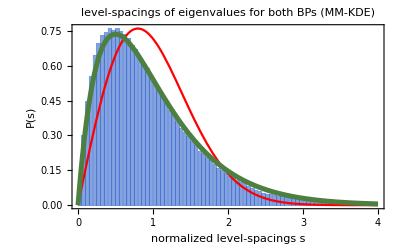

```mathematica
FMEforBothPlotMM=Histogram[FMESorted,{0.05},"PDF",ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},All},
Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacings s",10,Bold,FontFamily->"Arial",Black],Style["P(s)",10,Bold,FontFamily->"Arial",Black]},PlotLabel->Style["level-spacings of eigenvalues for both BPs (MM-KDE)",10,Bold,FontFamily->"Arial",Darker[Blue]],Epilog->{{Darker[Black],Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,Thickness[0.005],Plot[pSP[x],{x,0,4},PlotStyle->Directive[RGBColor[0.3,0.5,0.25],Thickness[0.009]]][[1]]}}]
```

```mathematica
SetDirectory["C:\\Users\\Mehdi Ameri\\Desktop"];
```

```mathematica
Directory[]
```

C:\Users\Mehdi Ameri\Desktop

```mathematica
Export["FMEforBothPlotMM.png",FMEforBothPlotMM,ImageResolution->300];
```

### Export

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\Final Results\\ATIntEnergyPlotMM.png",ATIntEnergyPlotMM,ImageResolution->300];
Export["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\Final Results\\GCIntEnergyPlotMM.png",GCIntEnergyPlotMM,ImageResolution->300];
Export["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\Final Results\\BothIntEnergyPlotMM.png",BothIntEnergyPlotMM,ImageResolution->300];
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\Final Results\\ATGroundStatePlotMM.png",ATGroundStatePlotMM,ImageResolution->300];Export["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\Final Results\\GCGroundStatePlotMM.png",GCGroundStatePlotMM,ImageResolution->300];
Export["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\Final Results\\BothGroundStatePlotMM.png",BothGroundStatePlotMM,ImageResolution->300];
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\Final Results\\ATExcitedStatesPlotMM.png",ATExcitedStatesPlotMM,ImageResolution->300];
Export["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\Final Results\\GCExcitedStatesPlotMM.png",GCExcitedStatesPlotMM,ImageResolution->300];
Export["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\Final Results\\BothExcitedStatesPlotMM.png",BothExcitedStatesPlotMM,ImageResolution->300];
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\Final Results\\ATMMOrbEnergyKDEUnf.png",ATMMOrbEnergyKDEUnf,ImageResolution->300];
Export["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\Final Results\\GCMMOrbEnergyKDEUnf.png",GCMMOrbEnergyKDEUnf,ImageResolution->300];
Export["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\Final Results\\BothMMOrbEnergyKDEUnf.png",BothMMOrbEnergyKDEUnf,ImageResolution->300];
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\Final Results\\GCMMOrbEnergyKDEUnf.png",GCMMOrbEnergyKDEUnf,ImageResolution->300];
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\Final Results\\FMEforATPlotMM.png",FMEforATPlotMM,ImageResolution->300];
Export["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\Final Results\\FMEforGCPlotMM.png",FMEforGCPlotMM,ImageResolution->300];
Export["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\Final Results\\FMEforBothPlotMM.png",FMEforBothPlotMM,ImageResolution->300];
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\Final Results\\ATIntEnergyPlotMMNoTitle.png",ATIntEnergyPlotMMNoTitle,ImageResolution->300];
Export["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\Final Results\\GCIntEnergyPlotMMNoTitle.png",GCIntEnergyPlotMMNoTitle,ImageResolution->300];
Export["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\Final Results\\BothIntEnergyPlotMMNoTitle.png",BothIntEnergyPlotMMNoTitle,ImageResolution->300];
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\Final Results\\ATGroundStatePlotMMNoTitle.png",ATGroundStatePlotMMNoTitle,ImageResolution->300];Export["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\Final Results\\GCGroundStatePlotMMNoTitle.png",GCGroundStatePlotMMNoTitle,ImageResolution->300];
Export["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\Final Results\\BothGroundStatePlotMMNoTitle.png",BothGroundStatePlotMMNoTitle,ImageResolution->300];
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\Final Results\\ATMMOrbEnergyKDEUnfNoTitle.png",ATMMOrbEnergyKDEUnfNoTitle,ImageResolution->300];
Export["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\Final Results\\GCMMOrbEnergyKDEUnfNoTitle.png",GCMMOrbEnergyKDEUnfNoTitle,ImageResolution->300];
Export["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\Final Results\\BothMMOrbEnergyKDEUnfNoTitle.png",BothMMOrbEnergyKDEUnfNoTitle,ImageResolution->300];
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\Final Results\\GCMMOrbEnergyKDEUnfNoTitle.png",GCMMOrbEnergyKDEUnfNoTitle,ImageResolution->300];
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\Final Results\\ATMMOrbEnergyKDEUnfNoTitleWithPoisson.png",ATMMOrbEnergyKDEUnfNoTitleWithPoisson,ImageResolution->300];
Export["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\Final Results\\GCMMOrbEnergyKDEUnfNoTitleWithPoisson.png",GCMMOrbEnergyKDEUnfNoTitleWithPoisson,ImageResolution->300];
Export["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\Final Results\\BothMMOrbEnergyKDEUnfNoTitleWithPoisson.png",BothMMOrbEnergyKDEUnfNoTitleWithPoisson,ImageResolution->300];
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\Final Results\\GCMMOrbEnergyKDEUnfNoTitleWithPoisson.png",GCMMOrbEnergyKDEUnfNoTitleWithPoisson,ImageResolution->300];
```

## Adjacent-gap ratios

AT-HB

```mathematica
filePaths=FileNames["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\AT\\Orbital Energy Levels\\frame_*.csv"];
Print["Total files found: ",Length[filePaths]];
```

Total files found: 1000

```mathematica
allRValues=Flatten[ParallelTable[ProcessSingleFileForR[file],{file,filePaths}]];

Print["Total pooled r-values across all files: ",Length[allRValues]];
If[Length[allRValues]>0,Print["Ensemble Mean Adjacent-Gap Ratio for AT-HB <r>: ",N[Mean[allRValues]]],Print["Warning: allRValues is empty. Please check file paths and format."]];
```

Total pooled r-values across all files: 319000

Ensemble Mean Adjacent-Gap Ratio for AT-HB <r>: 0.46362

```mathematica
fileMeans=DeleteCases[ProcessSingleFileForR/@filePaths,_?(_=={})];
fileMeans=Mean/@fileMeans;

Print["Mean of file-level <r>: ",Mean[fileMeans]];
Print["Standard Error of the Mean: ",StandardDeviation[fileMeans]/Sqrt[Length[fileMeans]]];
```

Mean of file-level <r>: 0.46362

Standard Error of the Mean: 0.000332567

```mathematica
Print[StandardDeviation[fileMeans]/Sqrt[Length[fileMeans]]*100 ," %"]
```

0.0332567 %

GC-HB

```mathematica
filePaths=FileNames["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\GC\\Orbital Energy Levels\\frame_*.csv"];
Print["Total files found: ",Length[filePaths]];
```

Total files found: 1000

```mathematica
allRValues=Flatten[ParallelTable[ProcessSingleFileForR[file],{file,filePaths}]];

Print["Total pooled r-values across all files: ",Length[allRValues]];
If[Length[allRValues]>0,Print["Ensemble Mean Adjacent-Gap Ratio for GC-HB <r>: ",N[Mean[allRValues]]],Print["Warning: allRValues is empty. Please check file paths and format."]];
```

Total pooled r-values across all files: 314000

Ensemble Mean Adjacent-Gap Ratio for GC-HB <r>: 0.467297

```mathematica
fileMeans=DeleteCases[ProcessSingleFileForR/@filePaths,_?(_=={})];
fileMeans=Mean/@fileMeans;

Print["Mean of file-level <r>: ",Mean[fileMeans]];
Print["Standard Error of the Mean: ",StandardDeviation[fileMeans]/Sqrt[Length[fileMeans]]];
```

Mean of file-level <r>: 0.467297

Standard Error of the Mean: 0.000542022

```mathematica
0.0005420223596*100
```

0.0542022

Both-HB

```mathematica
filePaths1=FileNames["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\AT\\Orbital Energy Levels\\frame_*.csv"];
Print["Total files found: ",Length[filePaths1]];
```

Total files found: 1000

```mathematica
filePaths2=FileNames["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\GC\\Orbital Energy Levels\\frame_*.csv"];
Print["Total files found: ",Length[filePaths2]];
```

Total files found: 1000

```mathematica
filePaths=Join[filePaths1,filePaths2];
%//Length
```

2000

```mathematica
allRValues=Flatten[ParallelTable[ProcessSingleFileForR[file],{file,filePaths}]];

Print["Total pooled r-values across all files: ",Length[allRValues]];
If[Length[allRValues]>0,Print["Ensemble Mean Adjacent-Gap Ratio for Both-HB <r>: ",N[Mean[allRValues]]],Print["Warning: allRValues is empty. Please check file paths and format."]];
```

Total pooled r-values across all files: 633000

Ensemble Mean Adjacent-Gap Ratio for Both-HB <r>: 0.465444

```mathematica
fileMeans=DeleteCases[ProcessSingleFileForR/@filePaths,_?(_=={})];
fileMeans=Mean/@fileMeans;

Print["Mean of file-level <r>: ",Mean[fileMeans]];
Print["Standard Error of the Mean: ",StandardDeviation[fileMeans]/Sqrt[Length[fileMeans]]];
```

Mean of file-level <r>: 0.465458

Standard Error of the Mean: 0.000320527

```mathematica
0.00032052*100
```

0.032052

AT-MM

```mathematica
filePaths=FileNames["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\AT\\Orbital Energy Levels\\multimode_sample_*.csv"];
Print["Total files found: ",Length[filePaths]];
```

Total files found: 1000

```mathematica
(*3. PROCESS ALL FILES IN PARALLEL AND FLATTEN*)
allRValues=Flatten[ParallelTable[ProcessSingleFileForR[file],{file,filePaths}]];

Print["Total pooled r-values across all files: ",Length[allRValues]];
If[Length[allRValues]>0,Print["Ensemble Mean Adjacent-Gap Ratio for AT-MM <r>: ",N[Mean[allRValues]]],Print["Warning: allRValues is empty. Please check file paths and format."]];
```

Total pooled r-values across all files: 319000

Ensemble Mean Adjacent-Gap Ratio for AT-MM <r>: 0.46553

```mathematica
fileMeans=DeleteCases[ProcessSingleFileForR/@filePaths,_?(_=={})];
fileMeans=Mean/@fileMeans;

Print["Mean of file-level <r>: ",Mean[fileMeans]];
Print["Standard Error of the Mean: ",StandardDeviation[fileMeans]/Sqrt[Length[fileMeans]]];
```

Mean of file-level <r>: 0.46553

Standard Error of the Mean: 0.000491184

```mathematica
0.0004911*100
```

0.04911

GC-MM

```mathematica
filePaths=FileNames["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\GC\\Orbital Energy Levels\\multimode_sample_*.csv"];
Print["Total files found: ",Length[filePaths]];
```

Total files found: 1000

```mathematica
(*3. PROCESS ALL FILES IN PARALLEL AND FLATTEN*)
allRValues=Flatten[ParallelTable[ProcessSingleFileForR[file],{file,filePaths}]];

Print["Total pooled r-values across all files: ",Length[allRValues]];
If[Length[allRValues]>0,Print["Ensemble Mean Adjacent-Gap Ratio for GC-MM <r>: ",N[Mean[allRValues]]],Print["Warning: allRValues is empty. Please check file paths and format."]];
```

Total pooled r-values across all files: 314000

Ensemble Mean Adjacent-Gap Ratio for GC-MM <r>: 0.477781

```mathematica
fileMeans=DeleteCases[ProcessSingleFileForR/@filePaths,_?(_=={})];
fileMeans=Mean/@fileMeans;

Print["Mean of file-level <r>: ",Mean[fileMeans]];
Print["Standard Error of the Mean: ",StandardDeviation[fileMeans]/Sqrt[Length[fileMeans]]];
```

Mean of file-level <r>: 0.477781

Standard Error of the Mean: 0.000498307

```mathematica
0.0004983*100
```

0.04983

Both-MM

```mathematica
filePaths1=FileNames["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\AT\\Orbital Energy Levels\\multimode_sample_*.csv"];
Print["Total files found: ",Length[filePaths1]];
```

Total files found: 1000

```mathematica
filePaths2=FileNames["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\GC\\Orbital Energy Levels\\multimode_sample_*.csv"];
Print["Total files found: ",Length[filePaths2]];
```

Total files found: 1000

```mathematica
filePaths=Join[filePaths1,filePaths2];
%//Length
```

2000

```mathematica
(*3. PROCESS ALL FILES IN PARALLEL AND FLATTEN*)
allRValues=Flatten[ParallelTable[ProcessSingleFileForR[file],{file,filePaths}]];

Print["Total pooled r-values across all files: ",Length[allRValues]];
If[Length[allRValues]>0,Print["Ensemble Mean Adjacent-Gap Ratio for both-MM <r>: ",N[Mean[allRValues]]],Print["Warning: allRValues is empty. Please check file paths and format."]];
```

Total pooled r-values across all files: 633000

Ensemble Mean Adjacent-Gap Ratio for both-MM <r>: 0.471607

```mathematica
fileMeans=DeleteCases[ProcessSingleFileForR/@filePaths,_?(_=={})];
fileMeans=Mean/@fileMeans;

Print["Mean of file-level <r>: ",Mean[fileMeans]];
Print["Standard Error of the Mean: ",StandardDeviation[fileMeans]/Sqrt[Length[fileMeans]]];
```

Mean of file-level <r>: 0.471655

Standard Error of the Mean: 0.000375635

```mathematica
0.0003756*100
```

0.03756

## Number Variance

### Both orbitals

#### AT-HB

Main Code New

```mathematica
(*CSV file pattern*)
filePattern="frame_*.csv";
orbitalSelection="All";
kdeBandwidth="Silverman";
Lvalues=Range[0.5,20,0.5];
nStarts=150;
edgeTrim=5;
minLevels=50;
```

```mathematica
folder=SystemDialogInput["Directory"];
If[folder===$Canceled,Abort[]];
files=Sort@FileNames[filePattern,folder];
Print["Files found: ",Length[files]];
If[files==={},Print["No CSV files found. Check the folder and file pattern."];
Abort[];];
If[!MemberQ[{"All","Occupied","Virtual"},orbitalSelection],Print["Invalid orbital selection."];
Abort[];];
```

Files found: 1000

```mathematica
readSpectrum[file_]:=Module[{data,rows,selectedRows,energies},data=Quiet@Check[Import[file,"CSV"],$Failed];
If[data===$Failed||!ListQ[data]||Length[data]<2,Return[$Failed]];
(*Remove header and select valid rows*)rows=Select[Rest[data],ListQ[#]&&Length[#]≥5&&NumericQ[#[[5]]]&&(orbitalSelection==="All"||NumericQ[#[[2]]])&];
(*Select occupied,virtual,or all orbitals*)selectedRows=Switch[orbitalSelection,"All",rows,"Occupied",Select[rows,#[[2]]>0&],"Virtual",Select[rows,#[[2]]==0&]];
If[selectedRows==={},Return[$Failed]];
(*Extract orbital energies in eV:column 5*)energies=N[selectedRows[[All,5]]];
If[!VectorQ[energies,NumericQ],Return[$Failed]];
If[!VectorQ[energies,TrueQ[Im[#]==0]&],Return[$Failed]];
Sort[Re[energies]]];
```

```mathematica
(*IMPORT ALL SPECTRA*)

rawSpectra=readSpectrum/@files;
validMask=ListQ/@rawSpectra;
spectra=Pick[rawSpectra,validMask];
validFiles=Pick[files,validMask];
Print["Valid spectra: ",Length[spectra]];
Print["Invalid files: ",Length[files]-Length[spectra]];
If[spectra==={},Print["No valid spectra found."];
Abort[];];


(*CHECK ORBITAL COUNTS*)

spectrumLengths=Length/@spectra;
Print["Orbital counts: ",Tally[spectrumLengths]];
If[Length[DeleteDuplicates[spectrumLengths]]≠1,Print["Error: Different numbers of orbitals per geometry."];
Abort[];];
nLevels=First[spectrumLengths];
If[nLevels<minLevels,Print["Insufficient number of orbitals."];
Abort[];];
Print["Orbitals per geometry: ",nLevels];
```

Valid spectra: 1000

Invalid files: 0

Orbital counts: {{321,1000}}

Orbitals per geometry: 321

```mathematica
(* ======================================================*)
(*4. CONSTRUCT THE COMMON ENSEMBLE KDE*)
(* ======================================================*)

(*Combine all orbital energies*)

allEnergies=Flatten[spectra];
Print["Total pooled energies: ",Length[allEnergies]];

(*Construct ONE KDE from the entire ensemble*)

commonKDE=Quiet@Check[SmoothKernelDistribution[allEnergies,kdeBandwidth],$Failed];
If[commonKDE===$Failed,Print["KDE construction failed."];
Abort[];];

(*Calculate the common cumulative density*)

commonCDFValues=N[CDF[commonKDE,#]&/@allEnergies];
If[!VectorQ[commonCDFValues,NumericQ],Print["Error in evaluating the common KDE CDF."];
Abort[];];
```

Total pooled energies: 321000

```mathematica
(* ======================================================*)
(*5. UNFOLD EACH GEOMETRY USING THE SAME KDE*)
(* ======================================================*)

(* Multiply the common CDF by the number of orbitals per geometry,NOT the total number of pooled energies *)

unfoldedFlat=nLevels commonCDFValues;

(*Restore the original geometry boundaries*)

unfoldedSpectra=Partition[unfoldedFlat,nLevels];

(*Sort individual unfolded spectra*)

unfoldedSpectra=Sort/@unfoldedSpectra;

Print["Common ensemble KDE unfolding completed."];
Print["Number of unfolded spectra: ",Length[unfoldedSpectra]];
```

Common ensemble KDE unfolding completed.

Number of unfolded spectra: 1000

```mathematica
(* ======================================================*)
(*6. NUMBER VARIANCE:INTERVAL COUNTING*)
(* ======================================================*)

ClearAll[intervalCounts,numberVarianceOne];


(*Count levels in intervals[x,x+L)*)

intervalCounts[levels_List,starts_List,len_?NumericQ]:=Module[{n=Length[levels],left=1,right=1,counts=ConstantArray[0,Length[starts]],t},Do[t=starts[[j]];
While[left≤n&&levels[[left]]<t,left++];
If[right<left,right=left];
While[right≤n&&levels[[right]]<t+len,right++];
counts[[j]]=right-left;,{j,Length[starts]}];
counts];


(*Number variance for one geometry*)

numberVarianceOne[levels_List,L_?NumericQ,nStarts_Integer,edgeTrim_?NumericQ]:=Module[{u,tMin,tMax,starts,counts},u=Sort[N[levels]];
If[Length[u]<2||L≤0,Return[Missing["Invalid"]]];
(*Remove edge regions*)tMin=First[u]+edgeTrim;
tMax=Last[u]-L-edgeTrim;
If[tMax≤tMin,Return[Missing["TooShort"]]];
(*Generate equally spaced window positions*)starts=N[Subdivide[tMin,tMax,nStarts]];
(*Count levels in all windows*)counts=intervalCounts[u,starts,L];
(*Calculate number variance*)Mean[(counts-L)^2]];
```

```mathematica
(* ======================================================*)
(*7. ENSEMBLE AVERAGING*)
(* ======================================================*)

numberVarianceEnsemble[unfolded_List,Lvals_List,nStarts_Integer,edgeTrim_?NumericQ]:=Table[Module[{vals},vals=Select[numberVarianceOne[#,ell,nStarts,edgeTrim]&/@unfolded,NumericQ];
If[Length[vals]≥2,{ell,Mean[vals],StandardDeviation[vals]/Sqrt[Length[vals]],Length[vals]},{ell,Indeterminate,Indeterminate,Length[vals]}]],{ell,Lvals}];
```

```mathematica
(* ======================================================*)
(*8. CALCULATE NUMBER VARIANCE FOR THE ENSEMBLE*)
(* ======================================================*)

Print["Calculating number variance..."];

commonKDEResults=numberVarianceEnsemble[unfoldedSpectra,Lvalues,nStarts,edgeTrim];


(*Extract results*)

commonKDEMean=commonKDEResults[[All,2]];

commonKDESE=commonKDEResults[[All,3]];

nContributing=commonKDEResults[[All,4]];


Print["Number variance calculation completed."];

Print["Minimum contributing geometries: ",Min[nContributing]];

Print["Maximum contributing geometries: ",Max[nContributing]];
```

Calculating number variance...

Number variance calculation completed.

Minimum contributing geometries: 1000

Maximum contributing geometries: 1000

```mathematica
(* ======================================================*)
(*9. THEORETICAL NUMBER VARIANCE CURVES*)
(* ======================================================*)

(* for large L *)
sigmaPoisson[L_?NumericQ]:=L;
sigmaSemiPoisson[L_?NumericQ]:=L/2+1/8;
sigmaGOE[L_?NumericQ]:=(2/Pi^2) (Log[2 Pi L]+EulerGamma+1-Pi^2/8);


(*sigmaPoisson[L_?NumericQ]:=L;
sigmaSemiPoisson[L_?NumericQ]:=L/2+(1-Exp[-4 L])/8;
sigmaGUE[L_?NumericQ]:=(Log[2 Pi L]+EulerGamma+1-Cos[2 Pi L]-CosIntegral[2 Pi L])/Pi^2+L (1-2 SinIntegral[2 Pi L]/Pi);
sigmaGOE[L_?NumericQ]:=2 sigmaGUE[L]+SinIntegral[Pi L]^2/Pi^2-SinIntegral[Pi L]/Pi;*)


(*Generate theoretical curves*)

poissonCurve=Table[{L,sigmaPoisson[L]},{L,Lvalues}];
semiPoissonCurve=Table[{L,sigmaSemiPoisson[L]},{L,Lvalues}];
GOECurve=Table[{L,sigmaGOE[L]},{L,Lvalues}];

(*Empirical KDE curve*)

empiricalCurve=Select[commonKDEResults[[All,{1,2}]],NumericQ[#[[2]]]&];
```

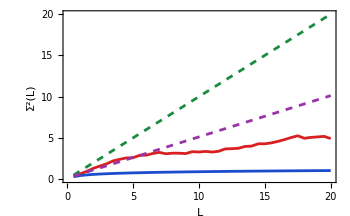

```mathematica
fontFamily="Times New Roman";
titlesSize=14;
fontSize=12;
lineThickness=2;
imageSize=350;
dataColor=RGBColor[0.85,0.12,0.12];
goeColor=RGBColor[0.1,0.3,0.8];
poissonColor=RGBColor[0.1,0.55,0.25];
semiColor=RGBColor[0.6,0.2,0.65];


(* ==============================================*)
(*NUMBER VARIANCE PLOT*)
(* ==============================================*)

ATHBNV=ListLinePlot[{empiricalCurve,GOECurve,poissonCurve,semiPoissonCurve},PlotStyle->{Directive[dataColor,AbsoluteThickness[lineThickness]],
Directive[goeColor,AbsoluteThickness[lineThickness]],
Directive[poissonColor,Dashed,AbsoluteThickness[lineThickness]],Directive[semiColor,Dashed,AbsoluteThickness[lineThickness]]},Frame->True,Axes->False,FrameLabel->{Style["L",titlesSize,Black,FontFamily->fontFamily],Style["Σ^2(L)",titlesSize,Black,FontFamily->fontFamily]},FrameStyle->Directive[Black,AbsoluteThickness[1.5]],FrameTicksStyle->Directive[Black,AbsoluteThickness[1.5],FontFamily->fontFamily(*,FontSize->fontSize*)],PlotRange->All,ImageSize->imageSize]
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\ATHBNV.png",ATHBNV,ImageResolution->300];
```

```mathematica
Export[FileNameJoin[{folder,"CommonEnsembleKDE_NumberVariance.csv"}],Prepend[commonKDEResults,{"L","MeanNumberVariance","StandardError","NumberOfGeometries"}],"CSV"];
```

```mathematica
GOEDeviation=Mean[Abs[empiricalCurve[[All,2]]-GOECurve[[All,2]]]];
PoissonDeviation=Mean[Abs[empiricalCurve[[All,2]]-poissonCurve[[All,2]]]];
SemiPoissonDeviation=Mean[Abs[empiricalCurve[[All,2]]-semiPoissonCurve[[All,2]]]];


(*RESULTS TABLE*)
Grid[{{"Ensemble","Mean Absolute Error"},{"GOE",NumberForm[GOEDeviation,{8,4}]},{"Poisson",NumberForm[PoissonDeviation,{8,4}]},{"Semi-Poisson",NumberForm[SemiPoissonDeviation,{8,4}]}},Frame->All,Alignment->Center]
```

Ensemble | Mean Absolute Error
GOE | 2.5130
Poisson | 6.8765
Semi-Poisson | 1.9574

```mathematica
(* =====================*)(*SPECTRAL COMPRESSIBILITY*)(* ==================================*)

(*SELECT LARGE-L FITTING RANGE*)
fitLmin=5;
fitLmax=20;

(*FUNCTION TO CALCULATE LINEAR SLOPE*)

spectralCompressibility[curve_]:=Module[{points,fit},points=Select[curve,fitLmin≤#[[1]]≤fitLmax&];
fit=Fit[points,{1,x},x];
Coefficient[fit,x]];


(*CALCULATE SPECTRAL COMPRESSIBILITY*)

chiData=spectralCompressibility[empiricalCurve];
chiGOE=spectralCompressibility[GOECurve];
chiPoisson=spectralCompressibility[poissonCurve];
chiSemiPoisson=spectralCompressibility[semiPoissonCurve];


(*DISPLAY RESULTS*)

Grid[{{"Ensemble","Spectral compressibility (χ)"},{"AT HB",NumberForm[chiData,{6,4}]},{"GOE",NumberForm[chiGOE,{6,4}]},{"Poisson",NumberForm[chiPoisson,{6,4}]},{"Semi-Poisson",NumberForm[chiSemiPoisson,{6,4}]}},Frame->All,Alignment->Center]
```

Ensemble | Spectral compressibility (χ)
AT HB | 0.1764
GOE | 0.0177
Poisson | 1.0000
Semi-Poisson | 0.5000

#### GC-HB

```mathematica
(*CSV file pattern*)
filePattern="frame_*.csv";
orbitalSelection="All";
kdeBandwidth="Silverman";
Lvalues=Range[0.5,20,0.5];
nStarts=150;
edgeTrim=5;
minLevels=50;
```

```mathematica
folder=SystemDialogInput["Directory"];
If[folder===$Canceled,Abort[]];
files=Sort@FileNames[filePattern,folder];
Print["Files found: ",Length[files]];
If[files==={},Print["No CSV files found. Check the folder and file pattern."];
Abort[];];
If[!MemberQ[{"All","Occupied","Virtual"},orbitalSelection],Print["Invalid orbital selection."];
Abort[];];
```

Files found: 1000

```mathematica
readSpectrum[file_]:=Module[{data,rows,selectedRows,energies},data=Quiet@Check[Import[file,"CSV"],$Failed];
If[data===$Failed||!ListQ[data]||Length[data]<2,Return[$Failed]];
(*Remove header and select valid rows*)rows=Select[Rest[data],ListQ[#]&&Length[#]≥5&&NumericQ[#[[5]]]&&(orbitalSelection==="All"||NumericQ[#[[2]]])&];
(*Select occupied,virtual,or all orbitals*)selectedRows=Switch[orbitalSelection,"All",rows,"Occupied",Select[rows,#[[2]]>0&],"Virtual",Select[rows,#[[2]]==0&]];
If[selectedRows==={},Return[$Failed]];
(*Extract orbital energies in eV:column 5*)energies=N[selectedRows[[All,5]]];
If[!VectorQ[energies,NumericQ],Return[$Failed]];
If[!VectorQ[energies,TrueQ[Im[#]==0]&],Return[$Failed]];
Sort[Re[energies]]];
```

```mathematica
(*IMPORT ALL SPECTRA*)

rawSpectra=readSpectrum/@files;
validMask=ListQ/@rawSpectra;
spectra=Pick[rawSpectra,validMask];
validFiles=Pick[files,validMask];
Print["Valid spectra: ",Length[spectra]];
Print["Invalid files: ",Length[files]-Length[spectra]];
If[spectra==={},Print["No valid spectra found."];
Abort[];];


(*CHECK ORBITAL COUNTS*)

spectrumLengths=Length/@spectra;
Print["Orbital counts: ",Tally[spectrumLengths]];
If[Length[DeleteDuplicates[spectrumLengths]]≠1,Print["Error: Different numbers of orbitals per geometry."];
Abort[];];
nLevels=First[spectrumLengths];
If[nLevels<minLevels,Print["Insufficient number of orbitals."];
Abort[];];
Print["Orbitals per geometry: ",nLevels];
```

Valid spectra: 1000

Invalid files: 0

Orbital counts: {{316,1000}}

Orbitals per geometry: 316

```mathematica
(* ======================================================*)
(*4. CONSTRUCT THE COMMON ENSEMBLE KDE*)
(* ======================================================*)

(*Combine all orbital energies*)

allEnergies=Flatten[spectra];
Print["Total pooled energies: ",Length[allEnergies]];

(*Construct ONE KDE from the entire ensemble*)

commonKDE=Quiet@Check[SmoothKernelDistribution[allEnergies,kdeBandwidth],$Failed];
If[commonKDE===$Failed,Print["KDE construction failed."];
Abort[];];

(*Calculate the common cumulative density*)

commonCDFValues=N[CDF[commonKDE,#]&/@allEnergies];
If[!VectorQ[commonCDFValues,NumericQ],Print["Error in evaluating the common KDE CDF."];
Abort[];];
```

Total pooled energies: 316000

```mathematica
(* ======================================================*)
(*5. UNFOLD EACH GEOMETRY USING THE SAME KDE*)
(* ======================================================*)

(* Multiply the common CDF by the number of orbitals per geometry,NOT the total number of pooled energies *)

unfoldedFlat=nLevels commonCDFValues;

(*Restore the original geometry boundaries*)

unfoldedSpectra=Partition[unfoldedFlat,nLevels];

(*Sort individual unfolded spectra*)

unfoldedSpectra=Sort/@unfoldedSpectra;

Print["Common ensemble KDE unfolding completed."];
Print["Number of unfolded spectra: ",Length[unfoldedSpectra]];
```

Common ensemble KDE unfolding completed.

Number of unfolded spectra: 1000

```mathematica
(* ======================================================*)
(*6. NUMBER VARIANCE:INTERVAL COUNTING*)
(* ======================================================*)

ClearAll[intervalCounts,numberVarianceOne];


(*Count levels in intervals[x,x+L)*)

intervalCounts[levels_List,starts_List,len_?NumericQ]:=Module[{n=Length[levels],left=1,right=1,counts=ConstantArray[0,Length[starts]],t},Do[t=starts[[j]];
While[left≤n&&levels[[left]]<t,left++];
If[right<left,right=left];
While[right≤n&&levels[[right]]<t+len,right++];
counts[[j]]=right-left;,{j,Length[starts]}];
counts];


(*Number variance for one geometry*)

numberVarianceOne[levels_List,L_?NumericQ,nStarts_Integer,edgeTrim_?NumericQ]:=Module[{u,tMin,tMax,starts,counts},u=Sort[N[levels]];
If[Length[u]<2||L≤0,Return[Missing["Invalid"]]];
(*Remove edge regions*)tMin=First[u]+edgeTrim;
tMax=Last[u]-L-edgeTrim;
If[tMax≤tMin,Return[Missing["TooShort"]]];
(*Generate equally spaced window positions*)starts=N[Subdivide[tMin,tMax,nStarts]];
(*Count levels in all windows*)counts=intervalCounts[u,starts,L];
(*Calculate number variance*)Mean[(counts-L)^2]];
```

```mathematica
(* ======================================================*)
(*7. ENSEMBLE AVERAGING*)
(* ======================================================*)

numberVarianceEnsemble[unfolded_List,Lvals_List,nStarts_Integer,edgeTrim_?NumericQ]:=Table[Module[{vals},vals=Select[numberVarianceOne[#,ell,nStarts,edgeTrim]&/@unfolded,NumericQ];
If[Length[vals]≥2,{ell,Mean[vals],StandardDeviation[vals]/Sqrt[Length[vals]],Length[vals]},{ell,Indeterminate,Indeterminate,Length[vals]}]],{ell,Lvals}];
```

```mathematica
(* ======================================================*)
(*8. CALCULATE NUMBER VARIANCE FOR THE ENSEMBLE*)
(* ======================================================*)

Print["Calculating number variance..."];

commonKDEResults=numberVarianceEnsemble[unfoldedSpectra,Lvalues,nStarts,edgeTrim];


(*Extract results*)

commonKDEMean=commonKDEResults[[All,2]];

commonKDESE=commonKDEResults[[All,3]];

nContributing=commonKDEResults[[All,4]];


Print["Number variance calculation completed."];

Print["Minimum contributing geometries: ",Min[nContributing]];

Print["Maximum contributing geometries: ",Max[nContributing]];
```

Calculating number variance...

Number variance calculation completed.

Minimum contributing geometries: 1000

Maximum contributing geometries: 1000

```mathematica
(* ======================================================*)
(*9. THEORETICAL NUMBER VARIANCE CURVES*)
(* ======================================================*)

(* for large L *)
sigmaPoisson[L_?NumericQ]:=L;
sigmaSemiPoisson[L_?NumericQ]:=L/2+1/8;
sigmaGOE[L_?NumericQ]:=(2/Pi^2) (Log[2 Pi L]+EulerGamma+1-Pi^2/8);


(*sigmaPoisson[L_?NumericQ]:=L;
sigmaSemiPoisson[L_?NumericQ]:=L/2+(1-Exp[-4 L])/8;
sigmaGUE[L_?NumericQ]:=(Log[2 Pi L]+EulerGamma+1-Cos[2 Pi L]-CosIntegral[2 Pi L])/Pi^2+L (1-2 SinIntegral[2 Pi L]/Pi);
sigmaGOE[L_?NumericQ]:=2 sigmaGUE[L]+SinIntegral[Pi L]^2/Pi^2-SinIntegral[Pi L]/Pi;*)


(*Generate theoretical curves*)

poissonCurve=Table[{L,sigmaPoisson[L]},{L,Lvalues}];
semiPoissonCurve=Table[{L,sigmaSemiPoisson[L]},{L,Lvalues}];
GOECurve=Table[{L,sigmaGOE[L]},{L,Lvalues}];

(*Empirical KDE curve*)

empiricalCurve=Select[commonKDEResults[[All,{1,2}]],NumericQ[#[[2]]]&];
```

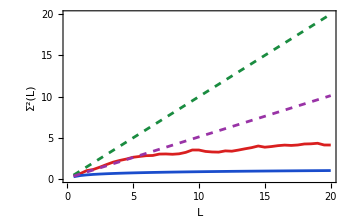

```mathematica
fontFamily="Times New Roman";
titlesSize=14;
fontSize=12;
lineThickness=2;
imageSize=350;
dataColor=RGBColor[0.85,0.12,0.12];
goeColor=RGBColor[0.1,0.3,0.8];
poissonColor=RGBColor[0.1,0.55,0.25];
semiColor=RGBColor[0.6,0.2,0.65];


(* ==============================================*)
(*NUMBER VARIANCE PLOT*)
(* ==============================================*)

GCHBNV=ListLinePlot[{empiricalCurve,GOECurve,poissonCurve,semiPoissonCurve},PlotStyle->{Directive[dataColor,AbsoluteThickness[lineThickness]],
Directive[goeColor,AbsoluteThickness[lineThickness]],
Directive[poissonColor,Dashed,AbsoluteThickness[lineThickness]],Directive[semiColor,Dashed,AbsoluteThickness[lineThickness]]},Frame->True,Axes->False,FrameLabel->{Style["L",titlesSize,Black,FontFamily->fontFamily],Style["Σ^2(L)",titlesSize,Black,FontFamily->fontFamily]},FrameStyle->Directive[Black,AbsoluteThickness[1.5]],FrameTicksStyle->Directive[Black,AbsoluteThickness[1.5],FontFamily->fontFamily(*,FontSize->fontSize*)],PlotRange->All,ImageSize->imageSize]
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\GCHBNV.png",GCHBNV,ImageResolution->300];
```

```mathematica
GOEDeviation=Mean[Abs[empiricalCurve[[All,2]]-GOECurve[[All,2]]]];
PoissonDeviation=Mean[Abs[empiricalCurve[[All,2]]-poissonCurve[[All,2]]]];
SemiPoissonDeviation=Mean[Abs[empiricalCurve[[All,2]]-semiPoissonCurve[[All,2]]]];


(*RESULTS TABLE*)
Grid[{{"Ensemble","Mean Absolute Error"},{"GOE",NumberForm[GOEDeviation,{8,4}]},{"Poisson",NumberForm[PoissonDeviation,{8,4}]},{"Semi-Poisson",NumberForm[SemiPoissonDeviation,{8,4}]}},Frame->All,Alignment->Center]
```

Ensemble | Mean Absolute Error
GOE | 2.2478
Poisson | 7.1417
Semi-Poisson | 2.1919

```mathematica
(*SPECTRAL COMPRESSIBILITY*)

fitLmin=5;
fitLmax=20;

spectralCompressibility[curve_]:=Module[{points,fit},points=Select[curve,fitLmin≤#[[1]]≤fitLmax&];
fit=Fit[points,{1,x},x];
Coefficient[fit,x]];

chiData=spectralCompressibility[empiricalCurve];
chiGOE=spectralCompressibility[GOECurve];
chiPoisson=spectralCompressibility[poissonCurve];
chiSemiPoisson=spectralCompressibility[semiPoissonCurve];

Grid[{{"Ensemble","Spectral compressibility (χ)"},{"GC HB",NumberForm[chiData,{6,4}]},{"GOE",NumberForm[chiGOE,{6,4}]},{"Poisson",NumberForm[chiPoisson,{6,4}]},{"Semi-Poisson",NumberForm[chiSemiPoisson,{6,4}]}},Frame->All,Alignment->Center]
```

Ensemble | Spectral compressibility (χ)
GC HB | 0.1094
GOE | 0.0177
Poisson | 1.0000
Semi-Poisson | 0.5000

#### Both-HB

```mathematica
(0.1631+0.1099+0.1478)/3
```

0.140267

```mathematica
(*AT DIRECTORY*)
atFolder="C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\AT\\Orbital Energy Levels";

(*GC DIRECTORY*)
gcFolder="C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\GC\\Orbital Energy Levels";


(*CSV FILE PATTERN*)
filePattern="frame_*.csv";


(*FIND FILES IN EACH DIRECTORY INDEPENDENTLY*)

atFiles=Sort@FileNames[filePattern,atFolder];

gcFiles=Sort@FileNames[filePattern,gcFolder];


(*COMBINE THE TWO FILE LISTS*)

files=Join[atFiles,gcFiles];


Print["AT files: ",Length[atFiles]];

Print["GC files: ",Length[gcFiles]];

Print["Total files: ",Length[files]];


If[files==={},Abort[]];
```

AT files: 1000

GC files: 1000

Total files: 2000

```mathematica
(*EXTRACT ALL ORBITAL ENERGIES*)readSpectrum[file_]:=Module[{data,rows,energies},data=Quiet@Check[Import[file,"CSV"],$Failed];
If[data===$Failed||!ListQ[data]||Length[data]<2,Return[$Failed]];
rows=Select[Rest[data],ListQ[#]&&Length[#]≥5&&NumericQ[#[[5]]]&];
If[rows==={},Return[$Failed]];
energies=N[rows[[All,5]]];
If[!VectorQ[energies,NumericQ],Return[$Failed]];
Sort[energies]];


(*IMPORT AT AND GC SEPARATELY*)

atRawSpectra=readSpectrum/@atFiles;

gcRawSpectra=readSpectrum/@gcFiles;


(*KEEP ONLY SUCCESSFULLY IMPORTED SPECTRA*)

atSpectra=Select[atRawSpectra,ListQ];

gcSpectra=Select[gcRawSpectra,ListQ];


(*COMBINE THE INDIVIDUAL SPECTRA*)

spectra=Join[atSpectra,gcSpectra];


Print["Valid AT spectra: ",Length[atSpectra]];

Print["Valid GC spectra: ",Length[gcSpectra]];

Print["Total valid spectra: ",Length[spectra]];

Print["Orbital counts: ",Tally[Length/@spectra]];


If[spectra==={},Abort[]];
```

Valid AT spectra: 1000

Valid GC spectra: 1000

Total valid spectra: 2000

Orbital counts: {{321,1000},{316,1000}}

```mathematica
(*POOL ALL AT AND GC ENERGIES*)
allEnergies=Flatten[spectra];

(*AVERAGE NUMBER OF ORBITALS PER GEOMETRY*)

meanLevels=Mean[Length/@spectra];


(*COMMON ENSEMBLE KDE*)

kdeBandwidth="Silverman";

commonKDE=SmoothKernelDistribution[allEnergies,kdeBandwidth];


(*APPLY THE SAME UNFOLDING FUNCTION TO EVERY SPECTRUM*)

unfoldingFunction[E_?NumericQ]:=meanLevels CDF[commonKDE,E];


(*PRESERVE INDIVIDUAL GEOMETRY BOUNDARIES*)

unfoldedSpectra=(unfoldingFunction/@#)&/@spectra;


Print["Combined AT + GC unfolding completed."];

Print["Total geometries: ",Length[unfoldedSpectra]];
```

Combined AT + GC unfolding completed.

Total geometries: 2000

```mathematica
Length[allEnergies]
```

637000

```mathematica
316+321
```

637

```mathematica
Lvalues=Range[0.5,20,0.5];

nStarts=150;

edgeTrim=5;
```

```mathematica
(* ======================================================*)(*4. NUMBER VARIANCE FUNCTIONS*)(* ======================================================*)ClearAll[intervalCounts,numberVarianceOne,numberVarianceEnsemble];


(*COUNT LEVELS INSIDE EACH INTERVAL[x,x+L)*)

intervalCounts[levels_List,starts_List,len_?NumericQ]:=Module[{n=Length[levels],left=1,right=1,counts=ConstantArray[0,Length[starts]],t},Do[t=starts[[j]];
While[left≤n&&levels[[left]]<t,left++];
If[right<left,right=left];
While[right≤n&&levels[[right]]<t+len,right++];
counts[[j]]=right-left;,{j,Length[starts]}];
counts];


(*NUMBER VARIANCE FOR ONE GEOMETRY*)

numberVarianceOne[levels_List,L_?NumericQ,nStarts_Integer,edgeTrim_?NumericQ]:=Module[{u,tMin,tMax,starts,counts},u=Sort[N[levels]];
If[Length[u]<2||L≤0,Return[Missing["Invalid"]]];
tMin=First[u]+edgeTrim;
tMax=Last[u]-L-edgeTrim;
If[tMax≤tMin,Return[Missing["TooShort"]]];
(*Generate window starting positions*)starts=N[Subdivide[tMin,tMax,nStarts]];
(*Count levels in each interval*)counts=intervalCounts[u,starts,L];
(*Calculate number variance*)Mean[(counts-L)^2]];


(* ======================================================*)
(*5. ENSEMBLE AVERAGING*)
(* ======================================================*)

numberVarianceEnsemble[unfolded_List,Lvals_List,nStarts_Integer,edgeTrim_?NumericQ]:=Table[Module[{vals},vals=Select[numberVarianceOne[#,ell,nStarts,edgeTrim]&/@unfolded,NumericQ];
If[Length[vals]≥2,{ell,Mean[vals],StandardDeviation[vals]/Sqrt[Length[vals]],Length[vals]},{ell,Indeterminate,Indeterminate,Length[vals]}]],{ell,Lvals}];
```

```mathematica
(* ======================================================*)(*6. COMBINED AT+GC NUMBER VARIANCE*)(* ======================================================*)
Lvalues=N[Range[0.5,20,0.5]];

nStarts=150;

edgeTrim=5;


Print["Calculating combined AT + GC number variance..."];


combinedResults=numberVarianceEnsemble[unfoldedSpectra,Lvalues,nStarts,edgeTrim];


(*EXTRACT RESULTS*)

combinedMean=combinedResults[[All,2]];

combinedSE=combinedResults[[All,3]];

nContributing=combinedResults[[All,4]];


(*EMPIRICAL CURVE*)

empiricalCurve=Select[combinedResults[[All,{1,2}]],NumericQ[#[[2]]]&];


Print["Calculation completed."];

Print["Total geometries: ",Length[unfoldedSpectra]];

Print["Minimum contributing geometries: ",Min[nContributing]];

Print["Maximum contributing geometries: ",Max[nContributing]];
```

Calculating combined AT + GC number variance...

Calculation completed.

Total geometries: 2000

Minimum contributing geometries: 2000

Maximum contributing geometries: 2000

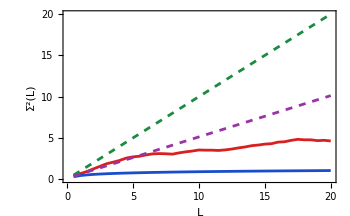

```mathematica
fontFamily="Times New Roman";
titlesSize=14;
fontSize=12;
lineThickness=2;
imageSize=350;
dataColor=RGBColor[0.85,0.12,0.12];
goeColor=RGBColor[0.1,0.3,0.8];
poissonColor=RGBColor[0.1,0.55,0.25];
semiColor=RGBColor[0.6,0.2,0.65];


(* ==============================================*)
(*NUMBER VARIANCE PLOT*)
(* ==============================================*)

ATGCHBNV=ListLinePlot[{empiricalCurve,GOECurve,poissonCurve,semiPoissonCurve},PlotStyle->{Directive[dataColor,AbsoluteThickness[lineThickness]],
Directive[goeColor,AbsoluteThickness[lineThickness]],
Directive[poissonColor,Dashed,AbsoluteThickness[lineThickness]],Directive[semiColor,Dashed,AbsoluteThickness[lineThickness]]},Frame->True,Axes->False,FrameLabel->{Style["L",titlesSize,Black,FontFamily->fontFamily],Style["Σ^2(L)",titlesSize,Black,FontFamily->fontFamily]},FrameStyle->Directive[Black,AbsoluteThickness[1.5]],FrameTicksStyle->Directive[Black,AbsoluteThickness[1.5],FontFamily->fontFamily(*,FontSize->fontSize*)],PlotRange->All,ImageSize->imageSize]
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\ATGCHBNV.png",ATGCHBNV,ImageResolution->300];
```

```mathematica
(* ======================================================*)(*10. MEAN ABSOLUTE ERROR*)(* ======================================================*)GOEDeviation=Mean[Abs[empiricalCurve[[All,2]]-GOECurve[[All,2]]]];


PoissonDeviation=Mean[Abs[empiricalCurve[[All,2]]-poissonCurve[[All,2]]]];


SemiPoissonDeviation=Mean[Abs[empiricalCurve[[All,2]]-semiPoissonCurve[[All,2]]]];


(*RESULTS TABLE*)

Grid[{{"Ensemble","Mean Absolute Error"},{"GOE",NumberForm[GOEDeviation,{8,4}]},{"Poisson",NumberForm[PoissonDeviation,{8,4}]},{"Semi-Poisson",NumberForm[SemiPoissonDeviation,{8,4}]}},Frame->All,Alignment->Center]
```

Ensemble | Mean Absolute Error
GOE | 2.4425
Poisson | 6.9471
Semi-Poisson | 2.0133

```mathematica
(*SPECTRAL COMPRESSIBILITY*)

fitLmin=5;
fitLmax=20;

spectralCompressibility[curve_]:=Module[{points,fit},points=Select[curve,fitLmin≤#[[1]]≤fitLmax&];
fit=Fit[points,{1,x},x];
Coefficient[fit,x]];

chiData=spectralCompressibility[empiricalCurve];
chiGOE=spectralCompressibility[GOECurve];
chiPoisson=spectralCompressibility[poissonCurve];
chiSemiPoisson=spectralCompressibility[semiPoissonCurve];

Grid[{{"Ensemble","Spectral compressibility (χ)"},{"Both HB",NumberForm[chiData,{6,4}]},{"GOE",NumberForm[chiGOE,{6,4}]},{"Poisson",NumberForm[chiPoisson,{6,4}]},{"Semi-Poisson",NumberForm[chiSemiPoisson,{6,4}]}},Frame->All,Alignment->Center]
```

Ensemble | Spectral compressibility (χ)
Both HB | 0.1474
GOE | 0.0177
Poisson | 1.0000
Semi-Poisson | 0.5000

#### AT-MM

```mathematica
(*CSV file pattern*)
filePattern="multimode_sample_*.csv";
orbitalSelection="All";
kdeBandwidth="Silverman";
Lvalues=Range[0.5,20,0.5];
nStarts=150;
edgeTrim=5;
minLevels=50;
```

```mathematica
folder=SystemDialogInput["Directory"];
If[folder===$Canceled,Abort[]];
files=Sort@FileNames[filePattern,folder];
Print["Files found: ",Length[files]];
If[files==={},Print["No CSV files found. Check the folder and file pattern."];
Abort[];];
If[!MemberQ[{"All","Occupied","Virtual"},orbitalSelection],Print["Invalid orbital selection."];
Abort[];];
```

Files found: 1000

```mathematica
readSpectrum[file_]:=Module[{data,rows,selectedRows,energies},data=Quiet@Check[Import[file,"CSV"],$Failed];
If[data===$Failed||!ListQ[data]||Length[data]<2,Return[$Failed]];
(*Remove header and select valid rows*)rows=Select[Rest[data],ListQ[#]&&Length[#]≥5&&NumericQ[#[[5]]]&&(orbitalSelection==="All"||NumericQ[#[[2]]])&];
(*Select occupied,virtual,or all orbitals*)selectedRows=Switch[orbitalSelection,"All",rows,"Occupied",Select[rows,#[[2]]>0&],"Virtual",Select[rows,#[[2]]==0&]];
If[selectedRows==={},Return[$Failed]];
(*Extract orbital energies in eV:column 5*)energies=N[selectedRows[[All,5]]];
If[!VectorQ[energies,NumericQ],Return[$Failed]];
If[!VectorQ[energies,TrueQ[Im[#]==0]&],Return[$Failed]];
Sort[Re[energies]]];
```

```mathematica
(*IMPORT ALL SPECTRA*)

rawSpectra=readSpectrum/@files;
validMask=ListQ/@rawSpectra;
spectra=Pick[rawSpectra,validMask];
validFiles=Pick[files,validMask];
Print["Valid spectra: ",Length[spectra]];
Print["Invalid files: ",Length[files]-Length[spectra]];
If[spectra==={},Print["No valid spectra found."];
Abort[];];


(*CHECK ORBITAL COUNTS*)

spectrumLengths=Length/@spectra;
Print["Orbital counts: ",Tally[spectrumLengths]];
If[Length[DeleteDuplicates[spectrumLengths]]≠1,Print["Error: Different numbers of orbitals per geometry."];
Abort[];];
nLevels=First[spectrumLengths];
If[nLevels<minLevels,Print["Insufficient number of orbitals."];
Abort[];];
Print["Orbitals per geometry: ",nLevels];
```

Valid spectra: 1000

Invalid files: 0

Orbital counts: {{321,1000}}

Orbitals per geometry: 321

```mathematica
(* ======================================================*)
(*4. CONSTRUCT THE COMMON ENSEMBLE KDE*)
(* ======================================================*)

(*Combine all orbital energies*)

allEnergies=Flatten[spectra];
Print["Total pooled energies: ",Length[allEnergies]];

(*Construct ONE KDE from the entire ensemble*)

commonKDE=Quiet@Check[SmoothKernelDistribution[allEnergies,kdeBandwidth],$Failed];
If[commonKDE===$Failed,Print["KDE construction failed."];
Abort[];];

(*Calculate the common cumulative density*)

commonCDFValues=N[CDF[commonKDE,#]&/@allEnergies];
If[!VectorQ[commonCDFValues,NumericQ],Print["Error in evaluating the common KDE CDF."];
Abort[];];
```

Total pooled energies: 321000

```mathematica
(* ======================================================*)
(*5. UNFOLD EACH GEOMETRY USING THE SAME KDE*)
(* ======================================================*)

(* Multiply the common CDF by the number of orbitals per geometry,NOT the total number of pooled energies *)

unfoldedFlat=nLevels commonCDFValues;

(*Restore the original geometry boundaries*)

unfoldedSpectra=Partition[unfoldedFlat,nLevels];

(*Sort individual unfolded spectra*)

unfoldedSpectra=Sort/@unfoldedSpectra;

Print["Common ensemble KDE unfolding completed."];
Print["Number of unfolded spectra: ",Length[unfoldedSpectra]];
```

Common ensemble KDE unfolding completed.

Number of unfolded spectra: 1000

```mathematica
(* ======================================================*)
(*6. NUMBER VARIANCE:INTERVAL COUNTING*)
(* ======================================================*)

ClearAll[intervalCounts,numberVarianceOne];


(*Count levels in intervals[x,x+L)*)

intervalCounts[levels_List,starts_List,len_?NumericQ]:=Module[{n=Length[levels],left=1,right=1,counts=ConstantArray[0,Length[starts]],t},Do[t=starts[[j]];
While[left≤n&&levels[[left]]<t,left++];
If[right<left,right=left];
While[right≤n&&levels[[right]]<t+len,right++];
counts[[j]]=right-left;,{j,Length[starts]}];
counts];


(*Number variance for one geometry*)

numberVarianceOne[levels_List,L_?NumericQ,nStarts_Integer,edgeTrim_?NumericQ]:=Module[{u,tMin,tMax,starts,counts},u=Sort[N[levels]];
If[Length[u]<2||L≤0,Return[Missing["Invalid"]]];
(*Remove edge regions*)tMin=First[u]+edgeTrim;
tMax=Last[u]-L-edgeTrim;
If[tMax≤tMin,Return[Missing["TooShort"]]];
(*Generate equally spaced window positions*)starts=N[Subdivide[tMin,tMax,nStarts]];
(*Count levels in all windows*)counts=intervalCounts[u,starts,L];
(*Calculate number variance*)Mean[(counts-L)^2]];
```

```mathematica
(* ======================================================*)
(*7. ENSEMBLE AVERAGING*)
(* ======================================================*)

numberVarianceEnsemble[unfolded_List,Lvals_List,nStarts_Integer,edgeTrim_?NumericQ]:=Table[Module[{vals},vals=Select[numberVarianceOne[#,ell,nStarts,edgeTrim]&/@unfolded,NumericQ];
If[Length[vals]≥2,{ell,Mean[vals],StandardDeviation[vals]/Sqrt[Length[vals]],Length[vals]},{ell,Indeterminate,Indeterminate,Length[vals]}]],{ell,Lvals}];
```

```mathematica
(* ======================================================*)
(*8. CALCULATE NUMBER VARIANCE FOR THE ENSEMBLE*)
(* ======================================================*)

Print["Calculating number variance..."];

commonKDEResults=numberVarianceEnsemble[unfoldedSpectra,Lvalues,nStarts,edgeTrim];


(*Extract results*)

commonKDEMean=commonKDEResults[[All,2]];

commonKDESE=commonKDEResults[[All,3]];

nContributing=commonKDEResults[[All,4]];


Print["Number variance calculation completed."];

Print["Minimum contributing geometries: ",Min[nContributing]];

Print["Maximum contributing geometries: ",Max[nContributing]];
```

Calculating number variance...

Number variance calculation completed.

Minimum contributing geometries: 1000

Maximum contributing geometries: 1000

```mathematica
(* ======================================================*)
(*9. THEORETICAL NUMBER VARIANCE CURVES*)
(* ======================================================*)

(* for large L *)
sigmaPoisson[L_?NumericQ]:=L;
sigmaSemiPoisson[L_?NumericQ]:=L/2+1/8;
sigmaGOE[L_?NumericQ]:=(2/Pi^2) (Log[2 Pi L]+EulerGamma+1-Pi^2/8);


(*sigmaPoisson[L_?NumericQ]:=L;
sigmaSemiPoisson[L_?NumericQ]:=L/2+(1-Exp[-4 L])/8;
sigmaGUE[L_?NumericQ]:=(Log[2 Pi L]+EulerGamma+1-Cos[2 Pi L]-CosIntegral[2 Pi L])/Pi^2+L (1-2 SinIntegral[2 Pi L]/Pi);
sigmaGOE[L_?NumericQ]:=2 sigmaGUE[L]+SinIntegral[Pi L]^2/Pi^2-SinIntegral[Pi L]/Pi;*)


(*Generate theoretical curves*)

poissonCurve=Table[{L,sigmaPoisson[L]},{L,Lvalues}];
semiPoissonCurve=Table[{L,sigmaSemiPoisson[L]},{L,Lvalues}];
GOECurve=Table[{L,sigmaGOE[L]},{L,Lvalues}];

(*Empirical KDE curve*)

empiricalCurve=Select[commonKDEResults[[All,{1,2}]],NumericQ[#[[2]]]&];
```

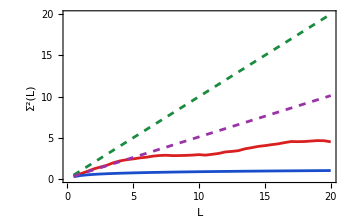

```mathematica
fontFamily="Times New Roman";
titlesSize=14;
fontSize=12;
lineThickness=2;
imageSize=350;
dataColor=RGBColor[0.85,0.12,0.12];
goeColor=RGBColor[0.1,0.3,0.8];
poissonColor=RGBColor[0.1,0.55,0.25];
semiColor=RGBColor[0.6,0.2,0.65];


(* ==============================================*)
(*NUMBER VARIANCE PLOT*)
(* ==============================================*)

ATMMNV=ListLinePlot[{empiricalCurve,GOECurve,poissonCurve,semiPoissonCurve},PlotStyle->{Directive[dataColor,AbsoluteThickness[lineThickness]],
Directive[goeColor,AbsoluteThickness[lineThickness]],
Directive[poissonColor,Dashed,AbsoluteThickness[lineThickness]],Directive[semiColor,Dashed,AbsoluteThickness[lineThickness]]},Frame->True,Axes->False,FrameLabel->{Style["L",titlesSize,Black,FontFamily->fontFamily],Style["Σ^2(L)",titlesSize,Black,FontFamily->fontFamily]},FrameStyle->Directive[Black,AbsoluteThickness[1.5]],FrameTicksStyle->Directive[Black,AbsoluteThickness[1.5],FontFamily->fontFamily(*,FontSize->fontSize*)],PlotRange->All,ImageSize->imageSize]
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\ATMMNV.png",ATMMNV,ImageResolution->300];
```

```mathematica
GOEDeviation=Mean[Abs[empiricalCurve[[All,2]]-GOECurve[[All,2]]]];
PoissonDeviation=Mean[Abs[empiricalCurve[[All,2]]-poissonCurve[[All,2]]]];
SemiPoissonDeviation=Mean[Abs[empiricalCurve[[All,2]]-semiPoissonCurve[[All,2]]]];


(*RESULTS TABLE*)
Grid[{{"Ensemble","Mean Absolute Error"},{"GOE",NumberForm[GOEDeviation,{8,4}]},{"Poisson",NumberForm[PoissonDeviation,{8,4}]},{"Semi-Poisson",NumberForm[SemiPoissonDeviation,{8,4}]}},Frame->All,Alignment->Center]
```

Ensemble | Mean Absolute Error
GOE | 2.2261
Poisson | 7.1634
Semi-Poisson | 2.1902

```mathematica
(*SPECTRAL COMPRESSIBILITY*)

fitLmin=5;
fitLmax=20;

spectralCompressibility[curve_]:=Module[{points,fit},points=Select[curve,fitLmin≤#[[1]]≤fitLmax&];
fit=Fit[points,{1,x},x];
Coefficient[fit,x]];

chiData=spectralCompressibility[empiricalCurve];
chiGOE=spectralCompressibility[GOECurve];
chiPoisson=spectralCompressibility[poissonCurve];
chiSemiPoisson=spectralCompressibility[semiPoissonCurve];

Grid[{{"Ensemble","Spectral compressibility (χ)"},{"AT MM",NumberForm[chiData,{6,4}]},{"GOE",NumberForm[chiGOE,{6,4}]},{"Poisson",NumberForm[chiPoisson,{6,4}]},{"Semi-Poisson",NumberForm[chiSemiPoisson,{6,4}]}},Frame->All,Alignment->Center]
```

Ensemble | Spectral compressibility (χ)
AT MM | 0.1631
GOE | 0.0177
Poisson | 1.0000
Semi-Poisson | 0.5000

#### GC-MM

```mathematica
(*CSV file pattern*)
filePattern="multimode_sample_*.csv";
orbitalSelection="All";
kdeBandwidth="Silverman";
Lvalues=Range[0.5,20,0.5];
nStarts=150;
edgeTrim=5;
minLevels=50;
```

```mathematica
folder=SystemDialogInput["Directory"];
If[folder===$Canceled,Abort[]];
files=Sort@FileNames[filePattern,folder];
Print["Files found: ",Length[files]];
If[files==={},Print["No CSV files found. Check the folder and file pattern."];
Abort[];];
If[!MemberQ[{"All","Occupied","Virtual"},orbitalSelection],Print["Invalid orbital selection."];
Abort[];];
```

Files found: 1000

```mathematica
readSpectrum[file_]:=Module[{data,rows,selectedRows,energies},data=Quiet@Check[Import[file,"CSV"],$Failed];
If[data===$Failed||!ListQ[data]||Length[data]<2,Return[$Failed]];
(*Remove header and select valid rows*)rows=Select[Rest[data],ListQ[#]&&Length[#]≥5&&NumericQ[#[[5]]]&&(orbitalSelection==="All"||NumericQ[#[[2]]])&];
(*Select occupied,virtual,or all orbitals*)selectedRows=Switch[orbitalSelection,"All",rows,"Occupied",Select[rows,#[[2]]>0&],"Virtual",Select[rows,#[[2]]==0&]];
If[selectedRows==={},Return[$Failed]];
(*Extract orbital energies in eV:column 5*)energies=N[selectedRows[[All,5]]];
If[!VectorQ[energies,NumericQ],Return[$Failed]];
If[!VectorQ[energies,TrueQ[Im[#]==0]&],Return[$Failed]];
Sort[Re[energies]]];
```

```mathematica
(*IMPORT ALL SPECTRA*)

rawSpectra=readSpectrum/@files;
validMask=ListQ/@rawSpectra;
spectra=Pick[rawSpectra,validMask];
validFiles=Pick[files,validMask];
Print["Valid spectra: ",Length[spectra]];
Print["Invalid files: ",Length[files]-Length[spectra]];
If[spectra==={},Print["No valid spectra found."];
Abort[];];


(*CHECK ORBITAL COUNTS*)

spectrumLengths=Length/@spectra;
Print["Orbital counts: ",Tally[spectrumLengths]];
If[Length[DeleteDuplicates[spectrumLengths]]≠1,Print["Error: Different numbers of orbitals per geometry."];
Abort[];];
nLevels=First[spectrumLengths];
If[nLevels<minLevels,Print["Insufficient number of orbitals."];
Abort[];];
Print["Orbitals per geometry: ",nLevels];
```

Valid spectra: 1000

Invalid files: 0

Orbital counts: {{316,1000}}

Orbitals per geometry: 316

```mathematica
(* ======================================================*)
(*4. CONSTRUCT THE COMMON ENSEMBLE KDE*)
(* ======================================================*)

(*Combine all orbital energies*)

allEnergies=Flatten[spectra];
Print["Total pooled energies: ",Length[allEnergies]];

(*Construct ONE KDE from the entire ensemble*)

commonKDE=Quiet@Check[SmoothKernelDistribution[allEnergies,kdeBandwidth],$Failed];
If[commonKDE===$Failed,Print["KDE construction failed."];
Abort[];];

(*Calculate the common cumulative density*)

commonCDFValues=N[CDF[commonKDE,#]&/@allEnergies];
If[!VectorQ[commonCDFValues,NumericQ],Print["Error in evaluating the common KDE CDF."];
Abort[];];
```

Total pooled energies: 316000

```mathematica
(* ======================================================*)
(*5. UNFOLD EACH GEOMETRY USING THE SAME KDE*)
(* ======================================================*)

(* Multiply the common CDF by the number of orbitals per geometry,NOT the total number of pooled energies *)

unfoldedFlat=nLevels commonCDFValues;

(*Restore the original geometry boundaries*)

unfoldedSpectra=Partition[unfoldedFlat,nLevels];

(*Sort individual unfolded spectra*)

unfoldedSpectra=Sort/@unfoldedSpectra;

Print["Common ensemble KDE unfolding completed."];
Print["Number of unfolded spectra: ",Length[unfoldedSpectra]];
```

Common ensemble KDE unfolding completed.

Number of unfolded spectra: 1000

```mathematica
(* ======================================================*)
(*6. NUMBER VARIANCE:INTERVAL COUNTING*)
(* ======================================================*)

ClearAll[intervalCounts,numberVarianceOne];


(*Count levels in intervals[x,x+L)*)

intervalCounts[levels_List,starts_List,len_?NumericQ]:=Module[{n=Length[levels],left=1,right=1,counts=ConstantArray[0,Length[starts]],t},Do[t=starts[[j]];
While[left≤n&&levels[[left]]<t,left++];
If[right<left,right=left];
While[right≤n&&levels[[right]]<t+len,right++];
counts[[j]]=right-left;,{j,Length[starts]}];
counts];


(*Number variance for one geometry*)

numberVarianceOne[levels_List,L_?NumericQ,nStarts_Integer,edgeTrim_?NumericQ]:=Module[{u,tMin,tMax,starts,counts},u=Sort[N[levels]];
If[Length[u]<2||L≤0,Return[Missing["Invalid"]]];
(*Remove edge regions*)tMin=First[u]+edgeTrim;
tMax=Last[u]-L-edgeTrim;
If[tMax≤tMin,Return[Missing["TooShort"]]];
(*Generate equally spaced window positions*)starts=N[Subdivide[tMin,tMax,nStarts]];
(*Count levels in all windows*)counts=intervalCounts[u,starts,L];
(*Calculate number variance*)Mean[(counts-L)^2]];
```

```mathematica
(* ======================================================*)
(*7. ENSEMBLE AVERAGING*)
(* ======================================================*)

numberVarianceEnsemble[unfolded_List,Lvals_List,nStarts_Integer,edgeTrim_?NumericQ]:=Table[Module[{vals},vals=Select[numberVarianceOne[#,ell,nStarts,edgeTrim]&/@unfolded,NumericQ];
If[Length[vals]≥2,{ell,Mean[vals],StandardDeviation[vals]/Sqrt[Length[vals]],Length[vals]},{ell,Indeterminate,Indeterminate,Length[vals]}]],{ell,Lvals}];
```

```mathematica
(* ======================================================*)
(*8. CALCULATE NUMBER VARIANCE FOR THE ENSEMBLE*)
(* ======================================================*)

Print["Calculating number variance..."];

commonKDEResults=numberVarianceEnsemble[unfoldedSpectra,Lvalues,nStarts,edgeTrim];


(*Extract results*)

commonKDEMean=commonKDEResults[[All,2]];

commonKDESE=commonKDEResults[[All,3]];

nContributing=commonKDEResults[[All,4]];


Print["Number variance calculation completed."];

Print["Minimum contributing geometries: ",Min[nContributing]];

Print["Maximum contributing geometries: ",Max[nContributing]];
```

Calculating number variance...

Number variance calculation completed.

Minimum contributing geometries: 1000

Maximum contributing geometries: 1000

```mathematica
(* ======================================================*)
(*9. THEORETICAL NUMBER VARIANCE CURVES*)
(* ======================================================*)

(* for large L *)
sigmaPoisson[L_?NumericQ]:=L;
sigmaSemiPoisson[L_?NumericQ]:=L/2+1/8;
sigmaGOE[L_?NumericQ]:=(2/Pi^2) (Log[2 Pi L]+EulerGamma+1-Pi^2/8);


(*sigmaPoisson[L_?NumericQ]:=L;
sigmaSemiPoisson[L_?NumericQ]:=L/2+(1-Exp[-4 L])/8;
sigmaGUE[L_?NumericQ]:=(Log[2 Pi L]+EulerGamma+1-Cos[2 Pi L]-CosIntegral[2 Pi L])/Pi^2+L (1-2 SinIntegral[2 Pi L]/Pi);
sigmaGOE[L_?NumericQ]:=2 sigmaGUE[L]+SinIntegral[Pi L]^2/Pi^2-SinIntegral[Pi L]/Pi;*)


(*Generate theoretical curves*)

poissonCurve=Table[{L,sigmaPoisson[L]},{L,Lvalues}];
semiPoissonCurve=Table[{L,sigmaSemiPoisson[L]},{L,Lvalues}];
GOECurve=Table[{L,sigmaGOE[L]},{L,Lvalues}];

(*Empirical KDE curve*)

empiricalCurve=Select[commonKDEResults[[All,{1,2}]],NumericQ[#[[2]]]&];
```

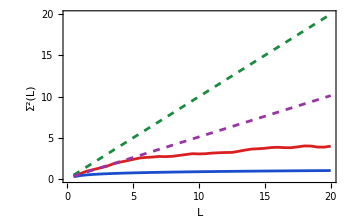

```mathematica
fontFamily="Times New Roman";
titlesSize=14;
fontSize=12;
lineThickness=2;
imageSize=350;
dataColor=RGBColor[0.85,0.12,0.12];
goeColor=RGBColor[0.1,0.3,0.8];
poissonColor=RGBColor[0.1,0.55,0.25];
semiColor=RGBColor[0.6,0.2,0.65];


(* ==============================================*)
(*NUMBER VARIANCE PLOT*)
(* ==============================================*)

GCMMNV=ListLinePlot[{empiricalCurve,GOECurve,poissonCurve,semiPoissonCurve},PlotStyle->{Directive[dataColor,AbsoluteThickness[lineThickness]],
Directive[goeColor,AbsoluteThickness[lineThickness]],
Directive[poissonColor,Dashed,AbsoluteThickness[lineThickness]],Directive[semiColor,Dashed,AbsoluteThickness[lineThickness]]},Frame->True,Axes->False,FrameLabel->{Style["L",titlesSize,Black,FontFamily->fontFamily],Style["Σ^2(L)",titlesSize,Black,FontFamily->fontFamily]},FrameStyle->Directive[Black,AbsoluteThickness[1.5]],FrameTicksStyle->Directive[Black,AbsoluteThickness[1.5],FontFamily->fontFamily(*,FontSize->fontSize*)],PlotRange->All,ImageSize->imageSize]
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\GCMMNV.png",GCMMNV,ImageResolution->300];
```

```mathematica
GOEDeviation=Mean[Abs[empiricalCurve[[All,2]]-GOECurve[[All,2]]]];
PoissonDeviation=Mean[Abs[empiricalCurve[[All,2]]-poissonCurve[[All,2]]]];
SemiPoissonDeviation=Mean[Abs[empiricalCurve[[All,2]]-semiPoissonCurve[[All,2]]]];


(*RESULTS TABLE*)
Grid[{{"Ensemble","Mean Absolute Error"},{"GOE",NumberForm[GOEDeviation,{8,4}]},{"Poisson",NumberForm[PoissonDeviation,{8,4}]},{"Semi-Poisson",NumberForm[SemiPoissonDeviation,{8,4}]}},Frame->All,Alignment->Center]
```

Ensemble | Mean Absolute Error
GOE | 2.0362
Poisson | 7.3534
Semi-Poisson | 2.3631

```mathematica
(*SPECTRAL COMPRESSIBILITY*)

fitLmin=5;
fitLmax=20;

spectralCompressibility[curve_]:=Module[{points,fit},points=Select[curve,fitLmin≤#[[1]]≤fitLmax&];
fit=Fit[points,{1,x},x];
Coefficient[fit,x]];

chiData=spectralCompressibility[empiricalCurve];
chiGOE=spectralCompressibility[GOECurve];
chiPoisson=spectralCompressibility[poissonCurve];
chiSemiPoisson=spectralCompressibility[semiPoissonCurve];

Grid[{{"Ensemble","Spectral compressibility (χ)"},{"GC MM",NumberForm[chiData,{6,4}]},{"GOE",NumberForm[chiGOE,{6,4}]},{"Poisson",NumberForm[chiPoisson,{6,4}]},{"Semi-Poisson",NumberForm[chiSemiPoisson,{6,4}]}},Frame->All,Alignment->Center]
```

Ensemble | Spectral compressibility (χ)
GC MM | 0.1099
GOE | 0.0177
Poisson | 1.0000
Semi-Poisson | 0.5000

#### Both-MM

```mathematica
(*AT DIRECTORY*)
atFolder="C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\AT\\Orbital Energy Levels";

(*GC DIRECTORY*)
gcFolder="C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\GC\\Orbital Energy Levels";


(*CSV FILE PATTERN*)
filePattern="multimode_sample_*.csv";


(*FIND FILES IN EACH DIRECTORY INDEPENDENTLY*)

atFiles=Sort@FileNames[filePattern,atFolder];

gcFiles=Sort@FileNames[filePattern,gcFolder];


(*COMBINE THE TWO FILE LISTS*)

files=Join[atFiles,gcFiles];


Print["AT files: ",Length[atFiles]];

Print["GC files: ",Length[gcFiles]];

Print["Total files: ",Length[files]];


If[files==={},Abort[]];
```

AT files: 1000

GC files: 1000

Total files: 2000

```mathematica
(*EXTRACT ALL ORBITAL ENERGIES*)readSpectrum[file_]:=Module[{data,rows,energies},data=Quiet@Check[Import[file,"CSV"],$Failed];
If[data===$Failed||!ListQ[data]||Length[data]<2,Return[$Failed]];
rows=Select[Rest[data],ListQ[#]&&Length[#]≥5&&NumericQ[#[[5]]]&];
If[rows==={},Return[$Failed]];
energies=N[rows[[All,5]]];
If[!VectorQ[energies,NumericQ],Return[$Failed]];
Sort[energies]];


(*IMPORT AT AND GC SEPARATELY*)

atRawSpectra=readSpectrum/@atFiles;

gcRawSpectra=readSpectrum/@gcFiles;


(*KEEP ONLY SUCCESSFULLY IMPORTED SPECTRA*)

atSpectra=Select[atRawSpectra,ListQ];

gcSpectra=Select[gcRawSpectra,ListQ];


(*COMBINE THE INDIVIDUAL SPECTRA*)

spectra=Join[atSpectra,gcSpectra];


Print["Valid AT spectra: ",Length[atSpectra]];

Print["Valid GC spectra: ",Length[gcSpectra]];

Print["Total valid spectra: ",Length[spectra]];

Print["Orbital counts: ",Tally[Length/@spectra]];


If[spectra==={},Abort[]];
```

Valid AT spectra: 1000

Valid GC spectra: 1000

Total valid spectra: 2000

Orbital counts: {{321,1000},{316,1000}}

```mathematica
(*POOL ALL AT AND GC ENERGIES*)
allEnergies=Flatten[spectra];

(*AVERAGE NUMBER OF ORBITALS PER GEOMETRY*)

meanLevels=Mean[Length/@spectra];


(*COMMON ENSEMBLE KDE*)

kdeBandwidth="Silverman";

commonKDE=SmoothKernelDistribution[allEnergies,kdeBandwidth];


(*APPLY THE SAME UNFOLDING FUNCTION TO EVERY SPECTRUM*)

unfoldingFunction[E_?NumericQ]:=meanLevels CDF[commonKDE,E];


(*PRESERVE INDIVIDUAL GEOMETRY BOUNDARIES*)

unfoldedSpectra=(unfoldingFunction/@#)&/@spectra;


Print["Combined AT + GC unfolding completed."];

Print["Total geometries: ",Length[unfoldedSpectra]];
```

Combined AT + GC unfolding completed.

Total geometries: 2000

```mathematica
Lvalues=Range[0.5,20,0.5];

nStarts=150;

edgeTrim=5;
```

```mathematica
(* ======================================================*)(*4. NUMBER VARIANCE FUNCTIONS*)(* ======================================================*)ClearAll[intervalCounts,numberVarianceOne,numberVarianceEnsemble];


(*COUNT LEVELS INSIDE EACH INTERVAL[x,x+L)*)

intervalCounts[levels_List,starts_List,len_?NumericQ]:=Module[{n=Length[levels],left=1,right=1,counts=ConstantArray[0,Length[starts]],t},Do[t=starts[[j]];
While[left≤n&&levels[[left]]<t,left++];
If[right<left,right=left];
While[right≤n&&levels[[right]]<t+len,right++];
counts[[j]]=right-left;,{j,Length[starts]}];
counts];


(*NUMBER VARIANCE FOR ONE GEOMETRY*)

numberVarianceOne[levels_List,L_?NumericQ,nStarts_Integer,edgeTrim_?NumericQ]:=Module[{u,tMin,tMax,starts,counts},u=Sort[N[levels]];
If[Length[u]<2||L≤0,Return[Missing["Invalid"]]];
tMin=First[u]+edgeTrim;
tMax=Last[u]-L-edgeTrim;
If[tMax≤tMin,Return[Missing["TooShort"]]];
(*Generate window starting positions*)starts=N[Subdivide[tMin,tMax,nStarts]];
(*Count levels in each interval*)counts=intervalCounts[u,starts,L];
(*Calculate number variance*)Mean[(counts-L)^2]];


(* ======================================================*)
(*5. ENSEMBLE AVERAGING*)
(* ======================================================*)

numberVarianceEnsemble[unfolded_List,Lvals_List,nStarts_Integer,edgeTrim_?NumericQ]:=Table[Module[{vals},vals=Select[numberVarianceOne[#,ell,nStarts,edgeTrim]&/@unfolded,NumericQ];
If[Length[vals]≥2,{ell,Mean[vals],StandardDeviation[vals]/Sqrt[Length[vals]],Length[vals]},{ell,Indeterminate,Indeterminate,Length[vals]}]],{ell,Lvals}];
```

```mathematica
(* ======================================================*)(*6. COMBINED AT+GC NUMBER VARIANCE*)(* ======================================================*)
Lvalues=N[Range[0.5,20,0.5]];

nStarts=150;

edgeTrim=5;


Print["Calculating combined AT + GC number variance..."];


combinedResults=numberVarianceEnsemble[unfoldedSpectra,Lvalues,nStarts,edgeTrim];


(*EXTRACT RESULTS*)

combinedMean=combinedResults[[All,2]];

combinedSE=combinedResults[[All,3]];

nContributing=combinedResults[[All,4]];


(*EMPIRICAL CURVE*)

empiricalCurve=Select[combinedResults[[All,{1,2}]],NumericQ[#[[2]]]&];


Print["Calculation completed."];

Print["Total geometries: ",Length[unfoldedSpectra]];

Print["Minimum contributing geometries: ",Min[nContributing]];

Print["Maximum contributing geometries: ",Max[nContributing]];
```

Calculating combined AT + GC number variance...

Calculation completed.

Total geometries: 2000

Minimum contributing geometries: 2000

Maximum contributing geometries: 2000

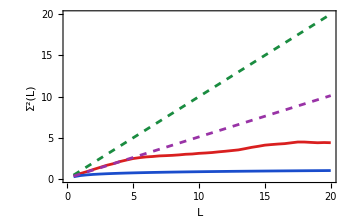

```mathematica
fontFamily="Times New Roman";
titlesSize=14;
fontSize=12;
lineThickness=2;
imageSize=350;
dataColor=RGBColor[0.85,0.12,0.12];
goeColor=RGBColor[0.1,0.3,0.8];
poissonColor=RGBColor[0.1,0.55,0.25];
semiColor=RGBColor[0.6,0.2,0.65];


(* ==============================================*)
(*NUMBER VARIANCE PLOT*)
(* ==============================================*)

ATGCMMNV=ListLinePlot[{empiricalCurve,GOECurve,poissonCurve,semiPoissonCurve},PlotStyle->{Directive[dataColor,AbsoluteThickness[lineThickness]],
Directive[goeColor,AbsoluteThickness[lineThickness]],
Directive[poissonColor,Dashed,AbsoluteThickness[lineThickness]],Directive[semiColor,Dashed,AbsoluteThickness[lineThickness]]},Frame->True,Axes->False,FrameLabel->{Style["L",titlesSize,Black,FontFamily->fontFamily],Style["Σ^2(L)",titlesSize,Black,FontFamily->fontFamily]},FrameStyle->Directive[Black,AbsoluteThickness[1.5]],FrameTicksStyle->Directive[Black,AbsoluteThickness[1.5],FontFamily->fontFamily(*,FontSize->fontSize*)],PlotRange->All,ImageSize->imageSize]
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\ATGCMMNV.png",ATGCMMNV,ImageResolution->300];
```

```mathematica
(* ======================================================*)(*10. MEAN ABSOLUTE ERROR*)(* ======================================================*)GOEDeviation=Mean[Abs[empiricalCurve[[All,2]]-GOECurve[[All,2]]]];


PoissonDeviation=Mean[Abs[empiricalCurve[[All,2]]-poissonCurve[[All,2]]]];


SemiPoissonDeviation=Mean[Abs[empiricalCurve[[All,2]]-semiPoissonCurve[[All,2]]]];


(*RESULTS TABLE*)

Grid[{{"Ensemble","Mean Absolute Error"},{"GOE",NumberForm[GOEDeviation,{8,4}]},{"Poisson",NumberForm[PoissonDeviation,{8,4}]},{"Semi-Poisson",NumberForm[SemiPoissonDeviation,{8,4}]}},Frame->All,Alignment->Center]
```

Ensemble | Mean Absolute Error
GOE | 2.2311
Poisson | 7.1584
Semi-Poisson | 2.1741

```mathematica
(*SPECTRAL COMPRESSIBILITY*)

fitLmin=5;
fitLmax=20;

spectralCompressibility[curve_]:=Module[{points,fit},points=Select[curve,fitLmin≤#[[1]]≤fitLmax&];
fit=Fit[points,{1,x},x];
Coefficient[fit,x]];

chiData=spectralCompressibility[empiricalCurve];
chiGOE=spectralCompressibility[GOECurve];
chiPoisson=spectralCompressibility[poissonCurve];
chiSemiPoisson=spectralCompressibility[semiPoissonCurve];

Grid[{{"Ensemble","Spectral compressibility (χ)"},{"Both MM",NumberForm[chiData,{6,4}]},{"GOE",NumberForm[chiGOE,{6,4}]},{"Poisson",NumberForm[chiPoisson,{6,4}]},{"Semi-Poisson",NumberForm[chiSemiPoisson,{6,4}]}},Frame->All,Alignment->Center]
```

Ensemble | Spectral compressibility (χ)
Both MM | 0.1478
GOE | 0.0177
Poisson | 1.0000
Semi-Poisson | 0.5000

## Important Tests

### Comparison with Erlang and Chi-squared

```mathematica
(*Define an Erlang distribution with shape k=3 and rate lambda=0.5*)
dist=ErlangDistribution[3,0.5];

(*Find the mean and variance*)
Mean[dist]
Variance[dist]
```

6.

12.

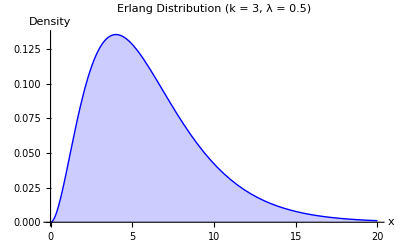

```mathematica
Plot[PDF[ErlangDistribution[3,0.5],x],{x,0,20},PlotLabel->"Erlang Distribution (k = 3, λ = 0.5)",AxesLabel->{"x","Density"},PlotStyle->Directive[Thick,Blue],Filling->Axis]
```

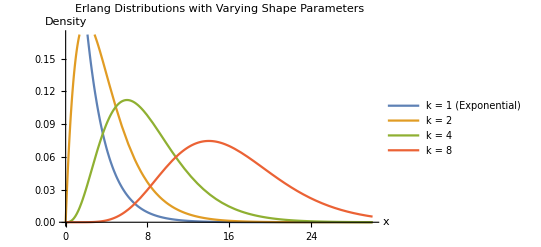

```mathematica
Plot[Evaluate[Table[PDF[ErlangDistribution[k,0.5],x],{k,{1,2,4,8}}]],{x,0,30},PlotLegends->{"k = 1 (Exponential)","k = 2","k = 4","k = 8"},AxesLabel->{"x","Density"},PlotLabel->"Erlang Distributions with Varying Shape Parameters"]
```

Very Important Result: the result of orbital energies (combined) perfectly matches Erlang distribution

```mathematica
(*Define a Chi-squared distribution with 4 degrees of freedom*)dist=ChiSquareDistribution[4];

(*Compute mean and variance*)
Mean[dist]     (*Returns 4*)
Variance[dist] (*Returns 8*)
```

4

8

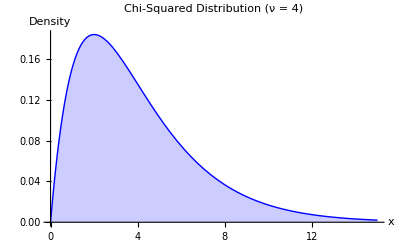

```mathematica
Plot[PDF[ChiSquareDistribution[4],x],{x,0,15},PlotLabel->"Chi-Squared Distribution (ν = 4)",AxesLabel->{"x","Density"},PlotStyle->Directive[Thick,Blue],Filling->Axis]
```

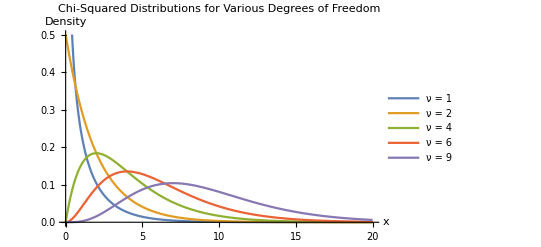

```mathematica
Plot[Evaluate[Table[PDF[ChiSquareDistribution[nu],x],{nu,{1,2,4,6,9}}]],{x,0,20},PlotRange->{0,0.5},PlotLegends->{"ν = 1","ν = 2","ν = 4","ν = 6","ν = 9"},AxesLabel->{"x","Density"},PlotLabel->"Chi-Squared Distributions for Various Degrees of Freedom"]
```

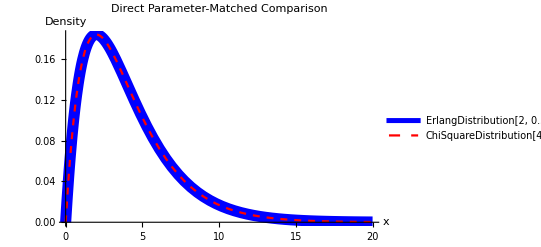

```mathematica
(* Let k=2 and lambda=0.5.Then the equivalent Chi-squared has nu=2*2=4 degrees of freedom,and its rate parameter matches naturally when lambda=0.5 *)Plot[Evaluate[{PDF[ErlangDistribution[2,0.5],x],PDF[ChiSquareDistribution[4],x]}],{x,0,20},PlotStyle->{Directive[Blue,Thickness[0.02]],Directive[Red,Dashed,Thick]},PlotLegends->{"ErlangDistribution[2, 0.5]","ChiSquareDistribution[4]"},AxesLabel->{"x","Density"},PlotLabel->"Direct Parameter-Matched Comparison",PlotRange->All]
```

### Find the fitting function for the combined plot

```mathematica
(*REGENERATE ORIGINAL COMBINED SPACINGS WITHOUT UPPER CUTOFF*)ProcessSingleFileFull[filePath_]:=Module[{importedData,rawEnergies,sortedLevels,nTotal,trimCount,coreLevels,nCore,kdeDist,unfoldedLevels,spacings,meanS},importedData=Import[filePath,"Data"];
If[Length[importedData]≤1,Return[{}]];
rawEnergies=ToExpression[Rest[importedData][[All,5]]];
sortedLevels=Sort[N[DeleteCases[rawEnergies,_Missing|Null|""|_String]]];
nTotal=Length[sortedLevels];
If[nTotal<20,Return[{}]];
trimCount=Floor[0.1*nTotal];
coreLevels=Take[sortedLevels,{trimCount+1,nTotal-trimCount}];
nCore=Length[coreLevels];
If[nCore<10,Return[{}]];
kdeDist=SmoothKernelDistribution[coreLevels];
unfoldedLevels=nCore*(CDF[kdeDist,#]&/@coreLevels);
spacings=Differences[unfoldedLevels];
If[Length[spacings]==0,Return[{}]];
meanS=Mean[spacings];
If[!NumberQ[meanS]||meanS≤0,Return[{}]];
Select[spacings/meanS,#>0&]];

AllSpacingsFull=Flatten[ParallelTable[ProcessSingleFileFull[file],{file,filePaths}]];

Print["Total spacings: ",Length[AllSpacingsFull]];
Print["Mean spacing: ",N[Mean[AllSpacingsFull]]];
Print["Maximum spacing: ",Max[AllSpacingsFull]];
```

Total spacings: 256000

Mean spacing: 1.

Maximum spacing: 13.4328

```mathematica
data=N[AllSpacingsFull];
n=Length[data]
```

256000

```mathematica
(*PROBABILITY DISTRIBUTIONS*)

pPoisson[s_]:=Exp[-s];

pGOE[s_]:=(Pi/2)*s*Exp[-Pi*s^2/4];

pGUE[s_]:=(32/Pi^2)*s^2*Exp[-4*s^2/Pi];
```

```mathematica
(*BRODY DISTRIBUTION*)

brodyB[beta_]:=Gamma[(beta+2)/(beta+1)]^(beta+1);

pBrody[s_,beta_]:=(beta+1)*brodyB[beta]*s^beta*Exp[-brodyB[beta]*s^(beta+1)];
```

```mathematica
(*GAMMA DISTRIBUTION WITH MEAN FIXED TO ONE*)

pGamma[s_,a_]:=a^a/Gamma[a]*s^(a-1)*Exp[-a*s];
```

```mathematica
(*LOG-LIKELIHOODS*)

LLPoisson=Total[Log[pPoisson[#]]&/@data];

LLGOE=Total[Log[pGOE[#]]&/@data];

LLGUE=Total[Log[pGUE[#]]&/@data];

LLBrody[beta_?NumericQ]:=Total[Log[pBrody[#,beta]]&/@data];

LLGamma[a_?NumericQ]:=Total[Log[pGamma[#,a]]&/@data];
```

```mathematica
(*Precalculate quantities*)
sumLogS=Total[Log[data]];
sumS=Total[data];

(*BRODY FIT*)

brodyB[beta_]:=Gamma[(beta+2)/(beta+1)]^(beta+1);

brodyLL[beta_?NumericQ]:=Module[{b},b=brodyB[beta];
n*Log[(beta+1)*b]+beta*sumLogS-b*Total[data^(beta+1)]];

brodyFit=NMaximize[{brodyLL[beta],0≤beta≤1},beta,Method->"NelderMead"];

betaBest=beta/.Last[brodyFit];

(*GAMMA FIT*)

gammaLL[a_?NumericQ]:=n*(a*Log[a]-LogGamma[a])+(a-1)*sumLogS-a*sumS;

gammaFit=NMaximize[{gammaLL[a],0.01≤a≤100},a,Method->"NelderMead"];

gammaBest=a/.Last[gammaFit];

(*RESULTS*)

Print["Best Brody beta = ",N[betaBest]];
Print["Best Gamma shape = ",N[gammaBest]];
```

Best Brody beta = 0.258724

Best Gamma shape = 1.73098

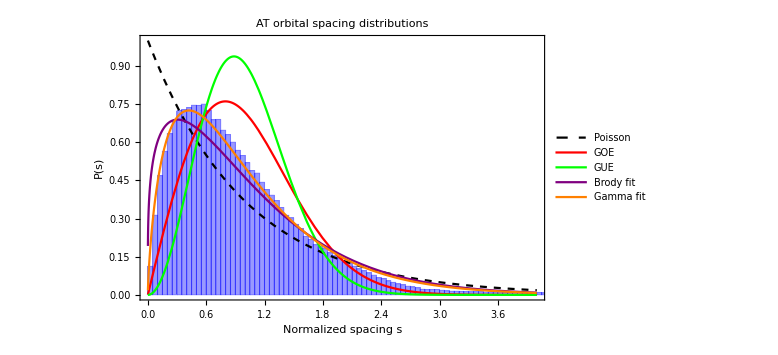

```mathematica
Show[Histogram[data,{0.05},"PDF",ChartStyle->Directive[Blue,Opacity[0.4]]],Plot[{pPoisson[s],pGOE[s],pGUE[s],pBrody[s,betaBest],pGamma[s,gammaBest]},{s,0.001,4},PlotStyle->{{Black,Dashed},{Red,Thick},{Green,Thick},{Purple,Thick},{Orange,Thick}},PlotLegends->{"Poisson","GOE","GUE","Brody fit","Gamma fit"}],Frame->True,FrameLabel->{"Normalized spacing s","P(s)"},PlotLabel->"AT orbital spacing distributions",PlotRange->{{0,4},All},ImageSize->Large]
```

### Different bandwidth for KDE

OCCUPIED ORBITALS

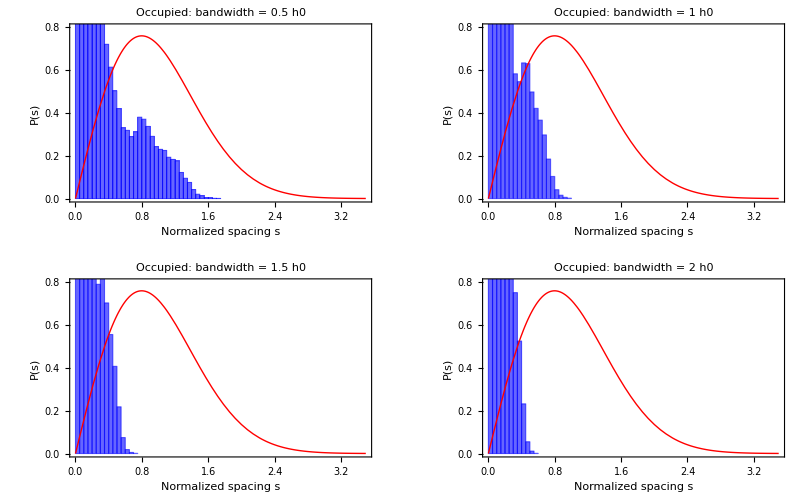

VIRTUAL ORBITALS

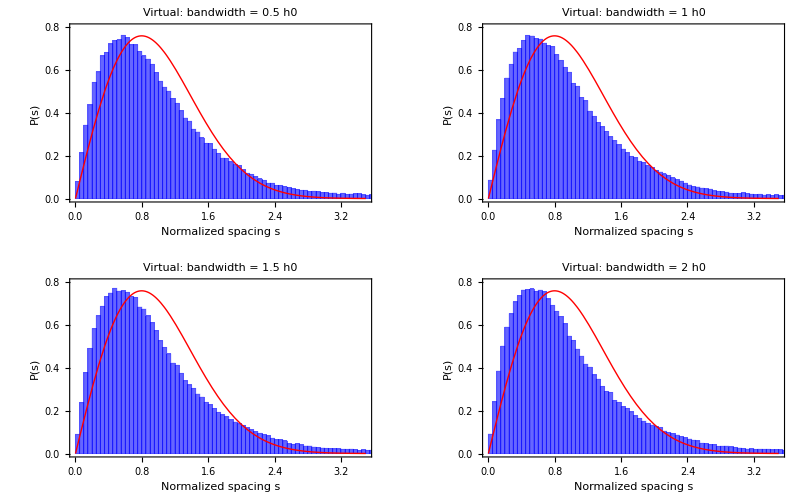

```mathematica
(*BANDWIDTH MULTIPLIERS*)bandwidthMultipliers={0.5,1,1.5,2};

(*PROCESS ONE FILE WITH A SPECIFIED BANDWIDTH*)
ProcessOrbitalsBW[filePath_,type_,multiplier_]:=Module[{data,rows,records,selectedLevels,sortedLevels,nTotal,trimCount,coreLevels,nCore,h0,h,kdeDist,unfoldedLevels,spacings,meanS},data=Import[filePath,"Data"];
If[Length[data]≤1,Return[{}]];
rows=Rest[data];
records=({parseNum[#[[2]]],parseNum[#[[5]]]}&)/@Select[rows,Length[#]≥5&];
records=Select[records,NumericQ[#[[1]]]&&NumericQ[#[[2]]]&];
selectedLevels=Which[type=="Occupied",Cases[records,{occ_,energy_}/;occ>0:>energy],type=="Virtual",Cases[records,{occ_,energy_}/;occ==0:>energy],True,{}];
sortedLevels=Sort[N[selectedLevels]];
nTotal=Length[sortedLevels];
If[nTotal<20,Return[{}]];
trimCount=Floor[0.1*nTotal];
coreLevels=Take[sortedLevels,{trimCount+1,nTotal-trimCount}];
nCore=Length[coreLevels];
If[nCore<10,Return[{}]];
(*Normal-reference bandwidth*)h0=1.06*StandardDeviation[coreLevels]*nCore^(-1/5);
h=multiplier*h0;
(*KDE unfolding with specified bandwidth*)kdeDist=SmoothKernelDistribution[coreLevels,h];
unfoldedLevels=nCore*(CDF[kdeDist,#]&/@coreLevels);
spacings=Differences[unfoldedLevels];
If[Length[spacings]==0,Return[{}]];
meanS=Mean[spacings];
If[!NumberQ[meanS]||meanS≤0,Return[{}]];
spacings/meanS];

(*CALCULATE ALL DISTRIBUTIONS*)

OccupiedResults=Association[Table[ToString[mult]->Flatten[ParallelTable[ProcessOrbitalsBW[file,"Occupied",mult],{file,filePaths}]],{mult,bandwidthMultipliers}]];

VirtualResults=Association[Table[ToString[mult]->Flatten[ParallelTable[ProcessOrbitalsBW[file,"Virtual",mult],{file,filePaths}]],{mult,bandwidthMultipliers}]];

(*PLOT FUNCTION*)

pGOE[s_]:=(Pi/2)*s*Exp[-Pi*s^2/4];

MakeBWPlot[data_,title_]:=Show[Histogram[data,{0.05},"PDF",ChartStyle->Directive[Blue,Opacity[0.6]]],Plot[pGOE[s],{s,0,3.5},PlotStyle->{Red,Thick}],Frame->True,FrameLabel->{"Normalized spacing s","P(s)"},PlotLabel->title,PlotRange->{{0,3.5},{0,0.8}},ImageSize->400];

(*OCCUPIED ORBITALS*)
OccupiedBWPlots=Table[MakeBWPlot[OccupiedResults[ToString[mult]],"Occupied: bandwidth = "<>ToString[mult]<>" h0"],{mult,bandwidthMultipliers}];

(*VIRTUAL ORBITALS*)
VirtualBWPlots=Table[MakeBWPlot[VirtualResults[ToString[mult]],"Virtual: bandwidth = "<>ToString[mult]<>" h0"],{mult,bandwidthMultipliers}];

Print["OCCUPIED ORBITALS"];
Print[GraphicsGrid[Partition[OccupiedBWPlots,2]]];

Print["VIRTUAL ORBITALS"];
Print[GraphicsGrid[Partition[VirtualBWPlots,2]]];
```

Mean occupied r = 0.393303

Mean virtual r = 0.48765

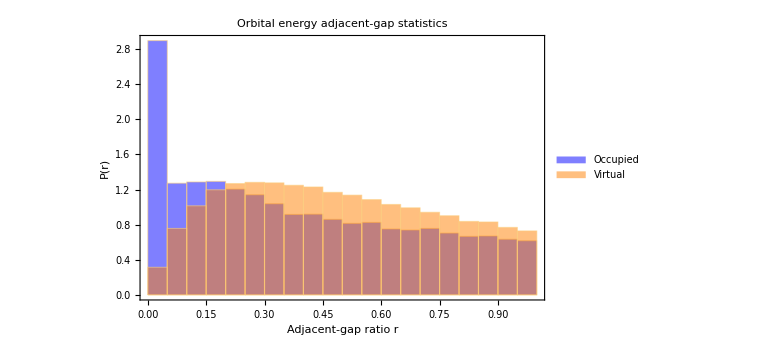

```mathematica
(*ADJACENT-GAP RATIO FOR EACH GEOMETRY*)ProcessRatios[filePath_,type_]:=Module[{data,rows,records,levels,gaps,ratios},data=Import[filePath,"Data"];
If[Length[data]≤1,Return[{}]];
rows=Rest[data];
records=({parseNum[#[[2]]],parseNum[#[[5]]]}&)/@Select[rows,Length[#]≥5&];
records=Select[records,NumericQ[#[[1]]]&&NumericQ[#[[2]]]&];
levels=Which[type=="Occupied",Cases[records,{occ_,energy_}/;occ>0:>energy],type=="Virtual",Cases[records,{occ_,energy_}/;occ==0:>energy],True,{}];
levels=Sort[N[levels]];
If[Length[levels]<3,Return[{}]];
gaps=Differences[levels];
ratios=(Min[#]/Max[#])&/@Partition[gaps,2,1];
Select[ratios,NumericQ[#]&&0≤#≤1&]];

(*PROCESS ALL GEOMETRIES*)

OccupiedRatios=Flatten[ParallelTable[ProcessRatios[file,"Occupied"],{file,filePaths}]];

VirtualRatios=Flatten[ParallelTable[ProcessRatios[file,"Virtual"],{file,filePaths}]];

(*MEAN VALUES*)

Print["Mean occupied r = ",N[Mean[OccupiedRatios]]];

Print["Mean virtual r = ",N[Mean[VirtualRatios]]];

(*HISTOGRAMS*)

Histogram[{OccupiedRatios,VirtualRatios},{0.05},"PDF",ChartLegends->{"Occupied","Virtual"},ChartStyle->{Blue,Orange},Frame->True,FrameLabel->{"Adjacent-gap ratio r","P(r)"},PlotLabel->"Orbital energy adjacent-gap statistics",ImageSize->Large]
```

Important Result: Changing

.08[.08]

### Separate Occupied and Virtual Orbitals

```mathematica
(*FIND ALL CSV FILES*)filePaths=FileNames["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\AT\\Orbital Energy Levels\\multimode_sample_*.csv"];

Print["Total files found: ",Length[filePaths]];

(*ROBUST NUMERICAL CONVERSION*)
parseNum[x_]:=Which[NumberQ[x],N[x],StringQ[x],Quiet[Check[N[ToExpression[StringTrim[x]]],Indeterminate]],True,Indeterminate];

(*PROCESS ONE SPECTRUM*)
ProcessOrbitals[filePath_,type_]:=Module[{data,rows,records,selectedLevels,sortedLevels,nTotal,trimCount,coreLevels,kdeDist,unfoldedLevels,spacings,meanS},data=Import[filePath,"Data"];
If[Length[data]≤1,Return[{}]];
rows=Rest[data];
(*Extract occupation and energy together*)records=({parseNum[#[[2]]],parseNum[#[[5]]]}&)/@Select[rows,Length[#]≥5&];
(*Remove invalid entries*)records=Select[records,NumericQ[#[[1]]]&&NumericQ[#[[2]]]&];
(*Separate occupied and virtual orbitals*)selectedLevels=Which[type=="Occupied",Cases[records,{occ_,energy_}/;occ>0:>energy],type=="Virtual",Cases[records,{occ_,energy_}/;occ==0:>energy],True,{}];
sortedLevels=Sort[N[selectedLevels]];
nTotal=Length[sortedLevels];
If[nTotal<20,Return[{}]];
(*Remove outer 10 percent*)trimCount=Floor[0.1*nTotal];
coreLevels=Take[sortedLevels,{trimCount+1,nTotal-trimCount}];
If[Length[coreLevels]<10,Return[{}]];
(*KDE unfolding*)kdeDist=SmoothKernelDistribution[coreLevels];
unfoldedLevels=Length[coreLevels]*(CDF[kdeDist,#]&/@coreLevels);
(*Calculate normalized spacings*)spacings=Differences[unfoldedLevels];
If[Length[spacings]==0,Return[{}]];
meanS=Mean[spacings];
If[!NumberQ[meanS]||meanS≤0,Return[{}]];
spacings/meanS];

(*PROCESS ALL FILES*)
AllOccupiedSpacings=Flatten[ParallelTable[ProcessOrbitals[file,"Occupied"],{file,filePaths}]];

AllVirtualSpacings=Flatten[ParallelTable[ProcessOrbitals[file,"Virtual"],{file,filePaths}]];

(*KEEP ALL POSITIVE SPACINGS*)
AllOccupiedSpacings=Select[AllOccupiedSpacings,#>0&];

AllVirtualSpacings=Select[AllVirtualSpacings,#>0&];

(*DISPLAY RESULTS*)
Print["Occupied spacings: ",Length[AllOccupiedSpacings]];
Print["Virtual spacings: ",Length[AllVirtualSpacings]];

If[Length[AllOccupiedSpacings]>0,Print["Mean occupied spacing: ",N[Mean[AllOccupiedSpacings]]]];

If[Length[AllVirtualSpacings]>0,Print["Mean virtual spacing: ",N[Mean[AllVirtualSpacings]]]];
```

Total files found: 1000

Occupied spacings: 55000

Virtual spacings: 202000

Mean occupied spacing: 1.

Mean virtual spacing: 1.

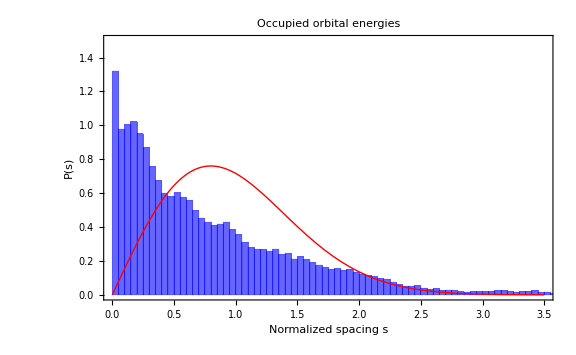

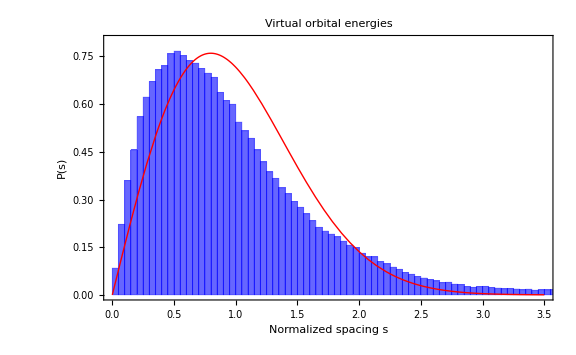

```mathematica
pGOE[s_]:=(Pi/2)*s*Exp[-Pi*s^2/4];

OccupiedPlot=Show[Histogram[AllOccupiedSpacings,{0.05},"PDF",ChartStyle->Directive[Blue,Opacity[0.6]]],Plot[pGOE[s],{s,0,3.5},PlotStyle->{Red,Thick}],Frame->True,FrameLabel->{"Normalized spacing s","P(s)"},PlotLabel->"Occupied orbital energies",PlotRange->{{0,3.5},{0,1.5}},ImageSize->Large];

VirtualPlot=Show[Histogram[AllVirtualSpacings,{0.05},"PDF",ChartStyle->Directive[Blue,Opacity[0.6]]],Plot[pGOE[s],{s,0,3.5},PlotStyle->{Red,Thick}],Frame->True,FrameLabel->{"Normalized spacing s","P(s)"},PlotLabel->"Virtual orbital energies",PlotRange->{{0,3.5},{0,0.8}},ImageSize->Large];

Print[OccupiedPlot];
Print[VirtualPlot];
```

```mathematica
filePaths=FileNames["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\AT\\Orbital Energy Levels\\multimode_sample_*.csv"];
Print["Total files found: ",Length[filePaths]];
```

Total files found: 1000

```mathematica
(*2. DEFINE FUNCTION TO COMPUTE r-VALUES FOR A SINGLE FILE*)
ProcessSingleFileForR[filePath_]:=Module[{importedData,rawEnergies,sortedLevels,rawSpacings,rValues},(*Import CSV as raw Data table*)importedData=Import[filePath,"Data"];
If[Length[importedData]≤1,Return[{}]];
(*Extract column 4 ("orbital_energy_hartree") and clean*)rawEnergies=ToExpression[Rest[importedData][[All,4]]];
sortedLevels=Sort[N[DeleteCases[rawEnergies,_Missing|Null|""|_String]]];
If[Length[sortedLevels]<10,Return[{}]];(*Skip files with too few levels*)(*Compute consecutive raw spacings s_i=E_{i+1}-E_i*)rawSpacings=Differences[sortedLevels];
If[Length[rawSpacings]<2,Return[{}]];
(*Compute adjacent-gap ratios r_i=Min(s_i,s_{i+1})/Max(s_i,s_{i+1})*)rValues=Table[Min[rawSpacings[[i]],rawSpacings[[i+1]]]/Max[rawSpacings[[i]],rawSpacings[[i+1]]],{i,1,Length[rawSpacings]-1}];
rValues];
```

```mathematica
(*3. PROCESS ALL FILES IN PARALLEL AND FLATTEN*)
allRValues=Flatten[ParallelTable[ProcessSingleFileForR[file],{file,filePaths}]];

Print["Total pooled r-values across all files: ",Length[allRValues]];
If[Length[allRValues]>0,Print["Ensemble Mean Adjacent-Gap Ratio <r>: ",N[Mean[allRValues]]],Print["Warning: allRValues is empty. Please check file paths and format."]];
```

Total pooled r-values across all files: 319000

Ensemble Mean Adjacent-Gap Ratio <r>: 0.46553

### AdjGapRatio

```mathematica
filePaths=FileNames["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\GC\\Orbital Energy Levels\\multimode_sample_*.csv"];
Print["Total files found: ",Length[filePaths]];
```

Total files found: 1000

```mathematica
(*2. DEFINE FUNCTION TO COMPUTE r-VALUES FOR A SINGLE FILE*)
ProcessSingleFileForR[filePath_]:=Module[{importedData,rawEnergies,sortedLevels,rawSpacings,rValues},(*Import CSV as raw Data table*)importedData=Import[filePath,"Data"];
If[Length[importedData]≤1,Return[{}]];
(*Extract column 4 ("orbital_energy_hartree") and clean*)rawEnergies=ToExpression[Rest[importedData][[All,4]]];
sortedLevels=Sort[N[DeleteCases[rawEnergies,_Missing|Null|""|_String]]];
If[Length[sortedLevels]<10,Return[{}]];(*Skip files with too few levels*)(*Compute consecutive raw spacings s_i=E_{i+1}-E_i*)rawSpacings=Differences[sortedLevels];
If[Length[rawSpacings]<2,Return[{}]];
(*Compute adjacent-gap ratios r_i=Min(s_i,s_{i+1})/Max(s_i,s_{i+1})*)rValues=Table[Min[rawSpacings[[i]],rawSpacings[[i+1]]]/Max[rawSpacings[[i]],rawSpacings[[i+1]]],{i,1,Length[rawSpacings]-1}];
rValues];
```

```mathematica
(*3. PROCESS ALL FILES IN PARALLEL AND FLATTEN*)
allRValues=Flatten[ParallelTable[ProcessSingleFileForR[file],{file,filePaths}]];

Print["Total pooled r-values across all files: ",Length[allRValues]];
If[Length[allRValues]>0,Print["Ensemble Mean Adjacent-Gap Ratio <r>: ",N[Mean[allRValues]]],Print["Warning: allRValues is empty. Please check file paths and format."]];
```

Total pooled r-values across all files: 314000

Ensemble Mean Adjacent-Gap Ratio <r>: 0.477781

```mathematica
(* =========================================================================*)
(*4. THEORETICAL BENCHMARKS& PLOTTING*)
(* =========================================================================*)
(*Theoretical Mean<r>Benchmarks for comparison:-Poisson (Integrable/Regular): ~0.3863-Semi-Poisson (Critical/Transition): ~0.50 (depends on exact model)-GOE (Quantum Chaos): ~0.5359*)
```

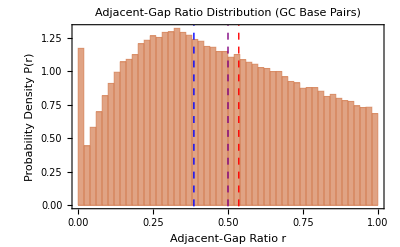

```mathematica
If[Length[allRValues]>0,Module[{rPlot},rPlot=Histogram[allRValues,{0.02},"PDF",ChartStyle->Directive[RGBColor[0.8,0.4,0.2],Opacity[0.6]],PlotRange->{{0,1},All},Frame->True,FrameLabel->{Style["Adjacent-Gap Ratio r",12,Bold,Black],Style["Probability Density P(r)",12,Bold,Black]},PlotLabel->Style["Adjacent-Gap Ratio Distribution (GC Base Pairs)",13,Bold,Black],Epilog->{{Directive[Blue,Thick,Dashed],InfiniteLine[{{0.3863,0},{0.3863,1}}]},{Directive[Purple,Thick,Dashed],InfiniteLine[{{0.50,0},{0.50,1}}]},{Directive[Red,Thick,Dashed],InfiniteLine[{{0.5359,0},{0.5359,1}}]}}];
(*Display plot directly without Display["STDOUT",...]*)Print[rPlot];
(*Export plot to Desktop*)Export["C:\\Users\\Mehdi Ameri\\Desktop\\GC_adjacent_gap_ratios.png",rPlot,ImageResolution->300];],Print["Skipping plot generation because no r-values were collected."]]
```

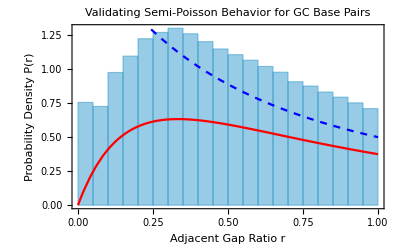

```mathematica
(*Define theoretical r-distribution functions for k=1*)(*Poisson:P(r)=2/(1+r)^2*)pPoisson[x_]:=2/(1+x)^2;

(*Semi-Poisson:P(r)=6r/(1+r)^4*)
pSemiPoisson[x_]:=6*x/(1+x)^4;

(*GOE distribution (approximate analytic form for r)*)
(*Or use a histogram of your pooled r values*)

Histogram[allRValues,{0.05},"PDF",ChartStyle->Directive[RGBColor[0.2,0.6,0.8],Opacity[0.5]],PlotRange->{{0,1},All},Frame->True,FrameLabel->{"Adjacent Gap Ratio r","Probability Density P(r)"},PlotLabel->Style["Validating Semi-Poisson Behavior for GC Base Pairs",Bold,12],Epilog->{{Red,Thick,Plot[pSemiPoisson[x],{x,0,1},PlotStyle->{Red,Thick}][[1]]},{Blue,Dashed,Thick,Plot[pPoisson[x],{x,0,1},PlotStyle->{Blue,Dashed,Thick}][[1]]}}]
```

```mathematica
fileMeans=DeleteCases[ProcessSingleFileForR/@filePaths,_?(_=={})];
fileMeans=Mean/@fileMeans;

Print["Mean of file-level <r>: ",Mean[fileMeans]];
Print["Standard Error of the Mean: ",StandardDeviation[fileMeans]/Sqrt[Length[fileMeans]]];
```

Mean of file-level <r>: 0.477781

Standard Error of the Mean: 0.000498307

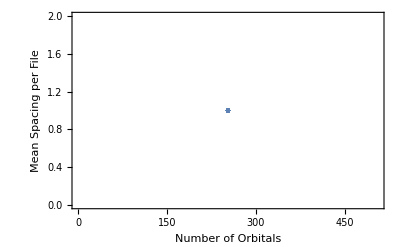

```mathematica
fileSizesAndMeans=Table[Module[{levels=ProcessSingleFile[filePath]},{Length[levels],If[Length[levels]>0,Mean[levels],Nothing]}],{filePath,filePaths}];

ListPlot[fileSizesAndMeans,Frame->True,FrameLabel->{"Number of Orbitals","Mean Spacing per File"},PlotStyle->Directive[PointSize[Small],Opacity[0.5]]]
```

### test - adenine

```mathematica
filePaths=FileNames["C:\\Users\\Mehdi Ameri\\Dropbox\\Chaotic signature in DNA\\Result of OE-Adenine\\multimode_sample_*.csv"];
Print["Total files found: ",Length[filePaths]];
```

Total files found: 1000

```mathematica
(* DEFINE UNFOLDING& NORMALIZATION FUNCTION FOR A SINGLE FILE *)
ProcessSingleFile[filePath_]:=Module[{importedData,rawEnergies,sortedLevels,nTotal,trimCount,coreLevels,nCore,kdeDist,unfoldedLevels,spacings,meanS,normSpacings},importedData=Import[filePath,"Data"];
If[Length[importedData]≤1,Return[{}]];

(* Extract energy column *)
rawEnergies=ToExpression[Rest[importedData][[All,5]]];
sortedLevels=Sort[N[DeleteCases[rawEnergies,_Missing|Null|""|_String]]];
nTotal=Length[sortedLevels];
If[nTotal<20,Return[{}]];

(* Band-edge trimming (outer 10%)*)
trimCount=Floor[0.1*nTotal];
coreLevels=Take[sortedLevels,{trimCount+1,nTotal-trimCount}];
nCore=Length[coreLevels];
If[nCore<10,Return[{}]];

(* Gaussian KDE Unfolding *)
kdeDist=SmoothKernelDistribution[coreLevels];
unfoldedLevels=Table[nCore*CDF[kdeDist,e],{e,coreLevels}];

(* Spacings& Local Normalization *)
spacings=Differences[unfoldedLevels];
If[Length[spacings]==0,Return[{}]];
meanS=Mean[spacings];
If[meanS≤0||!NumberQ[meanS],Return[{}]];
normSpacings=spacings/meanS;

(* Filter strictly within plot range boundary *)
(*Select[normSpacings,(#>0&&#≤3.5)&]];*)
Select[normSpacings,(#>0)&]]
```

```mathematica
(* PROCESS ALL FILES IN PARALLEL AND FLATTEN *)
AllSpacingsKDE=Flatten[ParallelTable[ProcessSingleFile[file],{file,filePaths}]];

Print["Total pooled normalized spacings across all files: ",Length[AllSpacingsKDE]];
Print["Ensemble Mean Spacing: ",N[Mean[AllSpacingsKDE]]];
```

Total pooled normalized spacings across all files: 132000

Ensemble Mean Spacing: 1.

```mathematica
Print[ "Maximum value of spacings: ",Max[AllSpacingsKDE]"ev"]
Print[ "Minimum value of spacings: ",Min[AllSpacingsKDE]"ev"]
```

Maximum value of spacings: 7.44468 ev

Minimum value of spacings: 0.00151256 ev

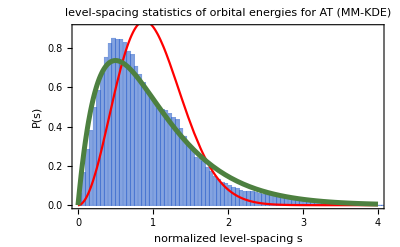

```mathematica
(* Generate Customized Plot *)
Histogram[AllSpacingsKDE,{0.05},"PDF",
ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},{0,0.9}},Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],
BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacing s",10,Bold,FontFamily->"Arial",Black],
Style["P(s)",10,Bold,FontFamily->"Arial",Black]},
PlotLabel->Style["level-spacing statistics of orbital energies for AT (MM-KDE)",10,Bold,FontFamily->"Arial",Darker[Blue]],Epilog->{{Red,,Thickness[0.005],Plot[pGUE[x],{x,0,4},PlotStyle->Directive[Red,(*Dashed,*)Thick]][[1]]},{Green,Thickness[0.005],Plot[pSP[x],{x,0,4},PlotStyle->Directive[RGBColor[0.3,0.5,0.25],Thickness[0.009]]][[1]]}}]
```

One single monomer does not show a matching with neither models!

### Old code for number variance

Main Code (old code)

```mathematica
(*IMPORT ALL ORBITAL SPECTRA*)
folder=SystemDialogInput["Directory"];
If[folder===$Canceled,Abort[]];
files=Sort@FileNames["frame_*.csv",folder];
Print["Files found: ",Length[files]];

(*EXTRACT ALL ORBITAL ENERGIES*)

readSpectrum[file_]:=Module[{data,energies},data=Quiet@Check[Import[file,"CSV"],$Failed];
If[data===$Failed||!ListQ[data]||Length[data]<2,Return[$Failed]];
If[!ListQ[First[data]]||Length[First[data]]<5,Return[$Failed]];
energies=Quiet@Check[N[data[[2;;,5]]],$Failed];
If[energies===$Failed||!VectorQ[energies,NumericQ],Return[$Failed]];
Sort[energies]];


rawSpectra=readSpectrum/@files;
validPairs=Select[MapThread[{#1,#2}&,{files,rawSpectra}],#[[2]]=!=$Failed&];
If[Length[validPairs]==0,Abort[]];

validFiles=validPairs[[All,1]];
spectra=validPairs[[All,2]];

Print["Valid spectra: ",Length[spectra]];
Print["Invalid files: ",Length[files]-Length[spectra]];

lengths=Length/@spectra;

Print["Orbital counts: ",Tally[lengths]];

If[Length[DeleteDuplicates[lengths]]≠1,Print["Error: The files contain different numbers of orbitals."];
Abort[]];

nLevels=First[lengths];
"Valid spectra: "1000;
"Invalid files: "0;
"Orbital counts: "{{321,1000}};

(*COMMON ENSEMBLE UNFOLDING*)Clear[binEdges,binCounts,binCenters,smoothedCounts,cdfEdges,unfoldingFunction,rawMin,rawMax,binWidth,nBins,smoothBins,histogram];


(*NUMBER OF ORBITALS PER GEOMETRY*)

nLevels=Length[First[spectra]];


(*COMBINE ALL ENERGIES FOR THE COMMON DENSITY*)

allEnergies=Flatten[spectra];

rawMin=Min[allEnergies];
rawMax=Max[allEnergies];

nBins=20000;

binWidth=(rawMax-rawMin)/nBins;


(*CONSTRUCT HISTOGRAM*)

histogram=HistogramList[allEnergies,{rawMin-binWidth,rawMax+binWidth,binWidth}];
binEdges=histogram[[1]];
binCounts=histogram[[2]];


(*SMOOTH THE HISTOGRAM*)

smoothBins=20;

smoothedCounts=GaussianFilter[N[binCounts],smoothBins];


(*CONSTRUCT THE CUMULATIVE COUNTING FUNCTION*)

cdfEdges=nLevels*Prepend[Accumulate[smoothedCounts],0.]/Total[smoothedCounts];


(*CHECK DIMENSIONS*)

Print["bin width: ",binWidth];
Print["Number of bins: ",Length[binCounts]];
Print["Number of bin edges: ",Length[binEdges]];
Print["Number of CDF values: ",Length[cdfEdges]];
Print["Total histogram counts: ",Total[binCounts]];
Print["CDF minimum: ",First[cdfEdges]];
Print["CDF maximum: ",Last[cdfEdges]];


(*CREATE THE UNFOLDING FUNCTION*)

If[Length[binEdges]≠Length[cdfEdges],Print["Error: Incompatible dimensions."];
Abort[]];


unfoldingFunction=Interpolation[Transpose[{binEdges,cdfEdges}],InterpolationOrder->1];


(*UNFOLD EACH GEOMETRY*)

unfoldedSpectra=(unfoldingFunction/@#)&/@spectra;

Print["Unfolding completed successfully."];

(*NUMBER VARIANCE*)ClearAll[intervalCounts,numberVarianceOne];

intervalCounts[levels_List,starts_List,len_?NumericQ]:=Module[{n=Length[levels],left=1,right=1,counts=ConstantArray[0,Length[starts]],t},Do[t=starts[[j]];
While[left≤n&&levels[[left]]<t,left++];
If[right<left,right=left];
While[right≤n&&levels[[right]]<t+len,right++];
counts[[j]]=right-left,{j,Length[starts]}];
counts];


numberVarianceOne[levels_List,L_?NumericQ,nStarts_Integer,edgeTrim_?NumericQ]:=Module[{u,tMin,tMax,starts,counts},u=Sort[N[levels]];
If[Length[u]<2||L≤0,Return[Missing["Invalid"]]];
tMin=First[u]+edgeTrim;
tMax=Last[u]-L-edgeTrim;
If[tMax≤tMin,Return[Missing["TooShort"]]];
starts=Subdivide[tMin,tMax,nStarts];
counts=intervalCounts[u,starts,L];
Mean[(counts-L)^2]];


(*ENSEMBLE AVERAGING*)

numberVarianceEnsemble[unfolded_List,Lvalues_List,nStarts_Integer,edgeTrim_?NumericQ]:=Table[Module[{vals},vals=Select[numberVarianceOne[#,ell,nStarts,edgeTrim]&/@unfolded,NumericQ];
If[Length[vals]≥2,{ell,Mean[vals],StandardDeviation[vals]/Sqrt[Length[vals]],Length[vals]},{ell,Indeterminate,Indeterminate,Length[vals]}]],{ell,Lvalues}];
```

```mathematica
Lvalues=Range[0.5,25,0.5];
combinedResults=numberVarianceEnsemble[unfoldedSpectra,Lvalues,150,5];
combinedMean=combinedResults[[All,2]];
combinedSE=combinedResults[[All,3]];
```

```mathematica
(* for large L *)
sigmaPoisson[L_]:=L;
sigmaSemiPoisson[L_]:=L/2+1/8;
sigmaGOE[L_]:=(2/Pi^2) (Log[2 Pi L]+EulerGamma+1-Pi^2/8);
```

```mathematica
(* for finite L *)
(*sigmaPoisson[L_?NumericQ]:=L;
sigmaSemiPoisson[L_?NumericQ]:=L/2+(1-Exp[-4 L])/8;
sigmaGUE[L_?NumericQ]:=(Log[2 Pi L]+EulerGamma+1-Cos[2 Pi L]-CosIntegral[2 Pi L])/Pi^2+L (1-2 SinIntegral[2 Pi L]/Pi);
sigmaGOE[L_?NumericQ]:=2 sigmaGUE[L]+SinIntegral[Pi L]^2/Pi^2-SinIntegral[Pi L]/Pi;*)
```

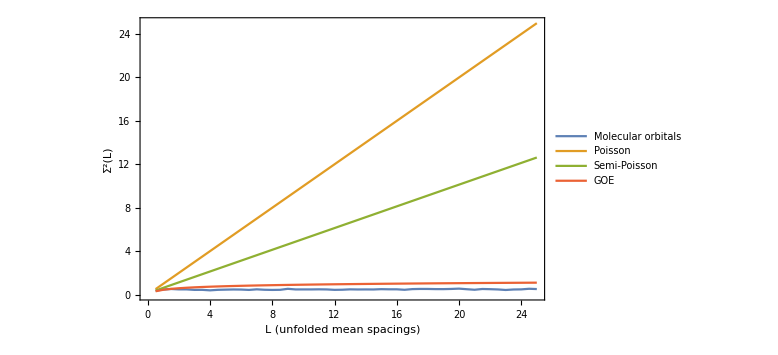

```mathematica
empiricalCurve=combinedResults[[All,{1,2}]];
poissonCurve=Transpose[{Lvalues,sigmaPoisson/@Lvalues}];
semiPoissonCurve=Transpose[{Lvalues,sigmaSemiPoisson/@Lvalues}];
GOECurve=Transpose[{Lvalues,sigmaGOE/@Lvalues}];

combinedPlot=ListLinePlot[{empiricalCurve,poissonCurve,semiPoissonCurve,GOECurve},PlotLegends->{"Molecular orbitals","Poisson","Semi-Poisson","GOE"},Frame->True,FrameLabel->{"L (unfolded mean spacings)","Σ^2(L)"},PlotRange->All,ImageSize->Large]
```

```mathematica
(* ===ADJUSTABLE STYLE SETTINGS===*)fontFamily="Arial";(*e.g.,"Arial","Helvetica","Times","Calibri"*)titleSize=15;
labelSize=13;
tickSize=11;
legendSize=11;
curveThickness=Thickness[0.004];

(*Colors*)
empColor=RGBColor[0.05,0.25,0.75];(*Empirical curve color*)poissonColor=Darker[Gray];
semiPoissonColor=RGBColor[0.85,0.35,0.05];
goeColor=Darker[Green];
frameColor=RGBColor[0.15,0.15,0.15];
textColor=Black;

(*Optional:include GUECurve if you also want to plot it*)
empiricalCurve=combinedResults[[All,{1,2}]];
poissonCurve=Transpose[{Lvalues,sigmaPoisson/@Lvalues}];
semiPoissonCurve=Transpose[{Lvalues,sigmaSemiPoisson/@Lvalues}];
GOECurve=Transpose[{Lvalues,sigmaGOE/@Lvalues}];

combinedPlot=ListLinePlot[{empiricalCurve,poissonCurve,semiPoissonCurve,GOECurve},PlotStyle->{Directive[empColor,Thick,curveThickness],Directive[poissonColor,Dashed,curveThickness],Directive[semiPoissonColor,DotDashed,curveThickness],Directive[goeColor,curveThickness]},PlotLegends->Placed[Style[#,legendSize,FontFamily->fontFamily,textColor]&/@{"Molecular orbitals","Poisson","Semi-Poisson","GOE"},{Left,Top}],Frame->True,FrameStyle->Directive[frameColor,Thickness[0.002]],BaseStyle->{FontSize->tickSize,FontFamily->fontFamily,textColor},FrameLabel->{Style["L (unfolded mean spacings)",labelSize,Bold,FontFamily->fontFamily,textColor],Style["\!\(\*SuperscriptBox[\(Σ\), \(2\)]\)(L)",labelSize,Bold,FontFamily->fontFamily,textColor]},PlotLabel->Style["Number Variance Σ\!\(\*SuperscriptBox[\(\), \(2\)]\)(L)",titleSize,Bold,FontFamily->fontFamily,textColor],PlotRange->All,ImageSize->Large]
```

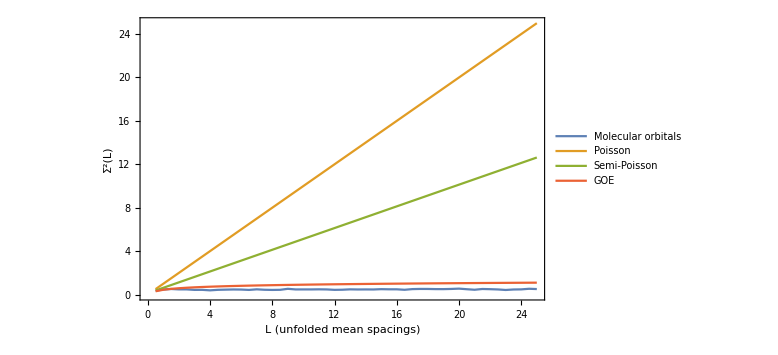

```mathematica
combinedPlot
```

```mathematica
(*COMBINED PERCENTAGE DEVIATIONS*)combinedL=combinedResults[[All,1]];

combinedMean=combinedResults[[All,2]];


combinedPercentData=Table[With[{L=combinedL[[i]],empirical=combinedMean[[i]]},{L,100 Abs[empirical-sigmaPoisson[L]]/sigmaPoisson[L],100 Abs[empirical-sigmaSemiPoisson[L]]/sigmaSemiPoisson[L],100 Abs[empirical-sigmaGOE[L]]/sigmaGOE[L]}],{i,Length[combinedL]}];
```

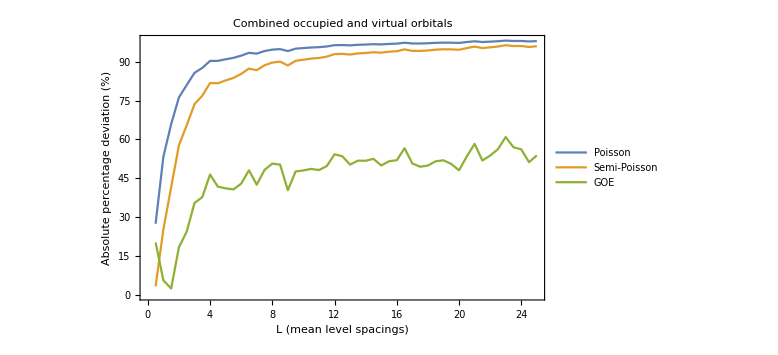

```mathematica
combinedPercentPlot=ListLinePlot[{combinedPercentData[[All,{1,2}]],combinedPercentData[[All,{1,3}]],combinedPercentData[[All,{1,4}]]},PlotLegends->{"Poisson","Semi-Poisson","GOE"},Frame->True,FrameLabel->{"L (mean level spacings)","Absolute percentage deviation (%)"},PlotLabel->"Combined occupied and virtual orbitals",PlotRange->All,ImageSize->Large];

combinedPercentPlot
```

```mathematica
combinedAverageDeviation=Mean/@Transpose[combinedPercentData[[All,2;;4]]];


Grid[Prepend[MapThread[{#1,NumberForm[#2,{8,3}]}&,{{"Poisson","Semi-Poisson","GOE"},combinedAverageDeviation}],{"Statistical model","Average deviation (%)"}],Frame->All,Alignment->Center]
```

Statistical model | Average deviation (%)
Poisson | 92.018
Semi-Poisson | 86.020
GOE | 46.188

### Hessian

```mathematica
SetDirectory["C:\\Users\\Mehdi Ameri\\Desktop"];
```

```mathematica
Eig=Import["covar_all_massweighted.dat"];
%//Length
```

1899

```mathematica
EigN=PseudoInverse[Eig];
%//Length
```

1899

```mathematica
(*EigN=1/Eig;*)
```

```mathematica
EigF=Sort[Flatten[EigN]];
%//Length
```

3606201

```mathematica
Print[ "Maximum Value: ",Max[EigF]"T^-2/J"]
Print[ "Minimum Value: ",Min[EigF]"T^-2/J"]
```

Maximum Value: 368.374 T^-2/J

Minimum Value: -400.329 T^-2/J

```mathematica
(* Perform Spectral Unfolding via KDE *)
nTotal=Length[EigF];
kdeDist=SmoothKernelDistribution[EigF];

(* Compute smooth cumulative counting function N_smooth(E)*)
unfoldedLevels=Table[nTotal*CDF[kdeDist,e],{e,EigF}];

(* Compute Normalized Spacings (s)*)
spacings=Differences[unfoldedLevels];
s=spacings/Mean[spacings];

(*Filter out extreme outliers for a clean plot*)
sClean=Select[s,(#>0&&#<4.0)&];
```

$Aborted

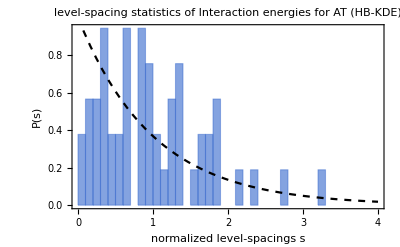

```mathematica
Histogram[sClean,{0.1},"PDF",ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},All},
Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacings s",10,Bold,FontFamily->"Arial",Black],Style["P(s)",10,Bold,FontFamily->"Arial",Black]},PlotLabel->Style["level-spacing statistics of Interaction energies for AT (HB-KDE)",10,Bold,FontFamily->"Arial",Darker[Blue]],Epilog->{{Darker[Black],Thickness[0.005],Dashed,Plot[pPoisson[x],{x,0,4},PlotStyle->Directive[Darker[Black],Dashed,Thick]][[1]]}}]
```

### Linear Unfolding Done

#### AT-HB

Linear Unfolding

```mathematica
filePaths=FileNames["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\AT\\Orbital Energy Levels\\frame_*.csv"];
Print["Total files found: ",Length[filePaths]];
```

Total files found: 1000

```mathematica
(*2. DEFINE POLYNOMIAL UNFOLDING& NORMALIZATION FUNCTION FOR A SINGLE FILE*)
ProcessSingleFile[filePath_]:=Module[{importedData,rawEnergies,sortedLevels,nTotal,trimCount,coreLevels,nCore,indices,polyDegree,fit,unfoldedLevels,spacings,meanS,normSpacings},(*Import CSV as raw Data table*)importedData=Import[filePath,"Data"];
If[Length[importedData]≤1,Return[{}]];

(*Extract energy column (column 4:"orbital_energy_hartree")*)rawEnergies=ToExpression[Rest[importedData][[All,5]]];
sortedLevels=Sort[N[DeleteCases[rawEnergies,_Missing|Null|""|_String]]];
nTotal=Length[sortedLevels];
If[nTotal<20,Return[{}]];
(*Skip files with too few levels*)

(*Band-edge trimming (outer 10%) to remove finite-size boundary effects*)trimCount=Floor[0.1*nTotal];
coreLevels=Take[sortedLevels,{trimCount+1,nTotal-trimCount}];
nCore=Length[coreLevels];
If[nCore<10,Return[{}]];(*Polynomial Unfolding (Using'x' instead of'E')*)indices=Range[1,nCore];

(*Fit cumulative level count with a smooth polynomial using variable'x'*)
polyDegree=6;
fit=Fit[Transpose[{coreLevels,indices}],Table[x^k,{k,0,polyDegree}],x];

(*Transform core energy levels into unfolded levels using'x'*)
unfoldedLevels=Table[fit/.x->e,{e,coreLevels}];

(*Compute nearest-neighbor unfolded level spacings*)
spacings=Differences[unfoldedLevels];
If[Length[spacings]==0,Return[{}]];

(*Normalize spacings so mean=1.0*)
meanS=Mean[spacings];
If[meanS≤0||!NumberQ[meanS],Return[{}]];
normSpacings=spacings/meanS;

(*Filter strictly within plot range (0 to 3.5)*)
Select[normSpacings,(#>0&&#≤3.5)&]];
```

```mathematica
(*3. PROCESS ALL FILES IN PARALLEL AND FLATTEN*)
AllSpacingsLinear=Flatten[ParallelTable[ProcessSingleFile[file],{file,filePaths}]];

Print["Total pooled normalized spacings across all files: ",Length[AllSpacingsLinear]];
Print["Ensemble Mean Spacing: ",N[Mean[AllSpacingsLinear]]];
```

Total pooled normalized spacings across all files: 251791

Ensemble Mean Spacing: 0.910787

```mathematica
Print[ "Maximum value of spacings: ",Max[AllSpacingsLinear]"ev"]
Print[ "Minimum value of spacings: ",Min[AllSpacingsLinear]"ev"]
```

Maximum value of spacings: 3.49994 ev

Minimum value of spacings: 0.000472748 ev

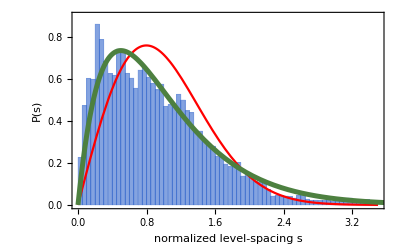

```mathematica
(* Generate Customized Plot *)
ATHBOrbEnergyLinearUnf=Histogram[AllSpacingsLinear,{0.05},"PDF",ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,3.5},{0,0.9}},
Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},FrameLabel->{Style["normalized level-spacing s",10,Bold,FontFamily->"Arial",Black],
Style["P(s)",10,Bold,FontFamily->"Arial",Black]},
Epilog->{{Red,Thickness[0.005],Plot[pGOE[x],{x,0,3.5},PlotStyle->Directive[Red,Thick]][[1]]},{Green,Thickness[0.005],Plot[pSP[x],{x,0,4},PlotStyle->Directive[RGBColor[0.3,0.5,0.25],Thickness[0.009]]][[1]]}}]
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\ATHBOrbEnergyLinearUnf.png",ATHBOrbEnergyLinearUnf,ImageResolution->300];
```

#### GC-HB

Linear Unfolding

```mathematica
filePaths=FileNames["C:\\Users\\Mehdi Ameri\\Desktop\\HB-Results\\GC\\Orbital Energy Levels\\frame_*.csv"];
Print["Total files found: ",Length[filePaths]];
```

Total files found: 1000

```mathematica
(*2. DEFINE POLYNOMIAL UNFOLDING& NORMALIZATION FUNCTION FOR A SINGLE FILE*)
ProcessSingleFile[filePath_]:=Module[{importedData,rawEnergies,sortedLevels,nTotal,trimCount,coreLevels,nCore,indices,polyDegree,fit,unfoldedLevels,spacings,meanS,normSpacings},(*Import CSV as raw Data table*)importedData=Import[filePath,"Data"];
If[Length[importedData]≤1,Return[{}]];

(*Extract energy column (column 4:"orbital_energy_hartree")*)rawEnergies=ToExpression[Rest[importedData][[All,5]]];
sortedLevels=Sort[N[DeleteCases[rawEnergies,_Missing|Null|""|_String]]];
nTotal=Length[sortedLevels];
If[nTotal<20,Return[{}]];
(*Skip files with too few levels*)

(*Band-edge trimming (outer 10%) to remove finite-size boundary effects*)trimCount=Floor[0.1*nTotal];
coreLevels=Take[sortedLevels,{trimCount+1,nTotal-trimCount}];
nCore=Length[coreLevels];
If[nCore<10,Return[{}]];(*Polynomial Unfolding (Using'x' instead of'E')*)indices=Range[1,nCore];

(*Fit cumulative level count with a smooth polynomial using variable'x'*)
polyDegree=6;
fit=Fit[Transpose[{coreLevels,indices}],Table[x^k,{k,0,polyDegree}],x];

(*Transform core energy levels into unfolded levels using'x'*)
unfoldedLevels=Table[fit/.x->e,{e,coreLevels}];

(*Compute nearest-neighbor unfolded level spacings*)
spacings=Differences[unfoldedLevels];
If[Length[spacings]==0,Return[{}]];

(*Normalize spacings so mean=1.0*)
meanS=Mean[spacings];
If[meanS≤0||!NumberQ[meanS],Return[{}]];
normSpacings=spacings/meanS;

(*Filter strictly within plot range (0 to 3.5)*)
Select[normSpacings,(#>0&&#≤3.5)&]];
```

```mathematica
(*3. PROCESS ALL FILES IN PARALLEL AND FLATTEN*)
AllSpacingsLinear=Flatten[ParallelTable[ProcessSingleFile[file],{file,filePaths}]];

Print["Total pooled normalized spacings across all files: ",Length[AllSpacingsLinear]];
Print["Ensemble Mean Spacing: ",N[Mean[AllSpacingsLinear]]];
```

Total pooled normalized spacings across all files: 251663

Ensemble Mean Spacing: 0.968196

```mathematica
Print[ "Maximum value of spacings: ",Max[AllSpacingsLinear]"ev"]
Print[ "Minimum value of spacings: ",Min[AllSpacingsLinear]"ev"]
```

Maximum value of spacings: 3.4999 ev

Minimum value of spacings: 0.00134478 ev

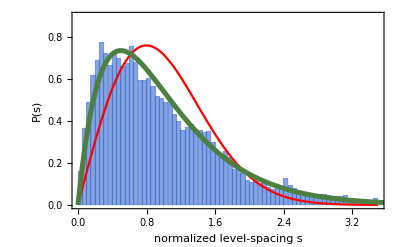

```mathematica
(* Generate Customized Plot *)
GCHBOrbEnergyLinearUnf=Histogram[AllSpacingsLinear,{0.05},"PDF",ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,3.5},{0,0.9}},
Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},FrameLabel->{Style["normalized level-spacing s",10,Bold,FontFamily->"Arial",Black],
Style["P(s)",10,Bold,FontFamily->"Arial",Black]},
Epilog->{{Red,Thickness[0.005],Plot[pGOE[x],{x,0,3.5},PlotStyle->Directive[Red,Thick]][[1]]},{Green,Thickness[0.005],Plot[pSP[x],{x,0,4},PlotStyle->Directive[RGBColor[0.3,0.5,0.25],Thickness[0.009]]][[1]]}}]
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\GCHBOrbEnergyLinearUnf.png",GCHBOrbEnergyLinearUnf,ImageResolution->300];
```

#### AT-MM

Linear Unfolding

```mathematica
filePaths=FileNames["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\AT\\Orbital Energy Levels\\multimode_sample_*.csv"];
Print["Total files found: ",Length[filePaths]];
```

Total files found: 1000

```mathematica
(*2. DEFINE POLYNOMIAL UNFOLDING& NORMALIZATION FUNCTION FOR A SINGLE FILE*)
ProcessSingleFile[filePath_]:=Module[{importedData,rawEnergies,sortedLevels,nTotal,trimCount,coreLevels,nCore,indices,polyDegree,fit,unfoldedLevels,spacings,meanS,normSpacings},(*Import CSV as raw Data table*)importedData=Import[filePath,"Data"];
If[Length[importedData]≤1,Return[{}]];

(*Extract energy column (column 4:"orbital_energy_hartree")*)rawEnergies=ToExpression[Rest[importedData][[All,5]]];
sortedLevels=Sort[N[DeleteCases[rawEnergies,_Missing|Null|""|_String]]];
nTotal=Length[sortedLevels];
If[nTotal<20,Return[{}]];
(*Skip files with too few levels*)

(*Band-edge trimming (outer 10%) to remove finite-size boundary effects*)trimCount=Floor[0.1*nTotal];
coreLevels=Take[sortedLevels,{trimCount+1,nTotal-trimCount}];
nCore=Length[coreLevels];
If[nCore<10,Return[{}]];(*Polynomial Unfolding (Using'x' instead of'E')*)indices=Range[1,nCore];

(*Fit cumulative level count with a smooth polynomial using variable'x'*)
polyDegree=6;
fit=Fit[Transpose[{coreLevels,indices}],Table[x^k,{k,0,polyDegree}],x];

(*Transform core energy levels into unfolded levels using'x'*)
unfoldedLevels=Table[fit/.x->e,{e,coreLevels}];

(*Compute nearest-neighbor unfolded level spacings*)
spacings=Differences[unfoldedLevels];
If[Length[spacings]==0,Return[{}]];

(*Normalize spacings so mean=1.0*)
meanS=Mean[spacings];
If[meanS≤0||!NumberQ[meanS],Return[{}]];
normSpacings=spacings/meanS;

(*Filter strictly within plot range (0 to 3.5)*)
Select[normSpacings,(#>0&&#≤3.5)&]];
```

```mathematica
(*3. PROCESS ALL FILES IN PARALLEL AND FLATTEN*)
AllSpacingsLinear=Flatten[ParallelTable[ProcessSingleFile[file],{file,filePaths}]];

Print["Total pooled normalized spacings across all files: ",Length[AllSpacingsLinear]];
Print["Ensemble Mean Spacing: ",N[Mean[AllSpacingsLinear]]];
```

Total pooled normalized spacings across all files: 252069

Ensemble Mean Spacing: 0.920999

```mathematica
Print[ "Maximum value of spacings: ",Max[AllSpacingsLinear]"ev"]
Print[ "Minimum value of spacings: ",Min[AllSpacingsLinear]"ev"]
```

Maximum value of spacings: 3.4994 ev

Minimum value of spacings: 0.000990738 ev

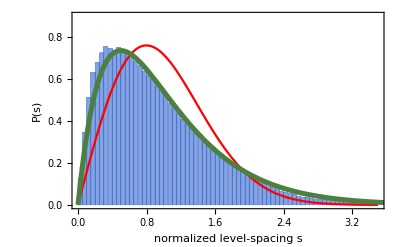

```mathematica
(* Generate Customized Plot *)
ATMMOrbEnergyLinearUnf=Histogram[AllSpacingsLinear,{0.05},"PDF",ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,3.5},{0,0.9}},
Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},FrameLabel->{Style["normalized level-spacing s",10,Bold,FontFamily->"Arial",Black],
Style["P(s)",10,Bold,FontFamily->"Arial",Black]},
Epilog->{{Red,Thickness[0.005],Plot[pGOE[x],{x,0,3.5},PlotStyle->Directive[Red,Thick]][[1]]},{Green,Thickness[0.005],Plot[pSP[x],{x,0,4},PlotStyle->Directive[RGBColor[0.3,0.5,0.25],Thickness[0.009]]][[1]]}}]
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\ATMMOrbEnergyLinearUnf.png",ATMMOrbEnergyLinearUnf,ImageResolution->300];
```

#### GC-MM

Linear Unfolding

```mathematica
filePaths=FileNames["C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\GC\\Orbital Energy Levels\\multimode_sample_*.csv"];
Print["Total files found: ",Length[filePaths]];
```

Total files found: 1000

```mathematica
(*2. DEFINE POLYNOMIAL UNFOLDING& NORMALIZATION FUNCTION FOR A SINGLE FILE*)
ProcessSingleFile[filePath_]:=Module[{importedData,rawEnergies,sortedLevels,nTotal,trimCount,coreLevels,nCore,indices,polyDegree,fit,unfoldedLevels,spacings,meanS,normSpacings},(*Import CSV as raw Data table*)importedData=Import[filePath,"Data"];
If[Length[importedData]≤1,Return[{}]];

(*Extract energy column (column 4:"orbital_energy_hartree")*)rawEnergies=ToExpression[Rest[importedData][[All,5]]];
sortedLevels=Sort[N[DeleteCases[rawEnergies,_Missing|Null|""|_String]]];
nTotal=Length[sortedLevels];
If[nTotal<20,Return[{}]];
(*Skip files with too few levels*)

(*Band-edge trimming (outer 10%) to remove finite-size boundary effects*)trimCount=Floor[0.1*nTotal];
coreLevels=Take[sortedLevels,{trimCount+1,nTotal-trimCount}];
nCore=Length[coreLevels];
If[nCore<10,Return[{}]];(*Polynomial Unfolding (Using'x' instead of'E')*)indices=Range[1,nCore];

(*Fit cumulative level count with a smooth polynomial using variable'x'*)
polyDegree=6;
fit=Fit[Transpose[{coreLevels,indices}],Table[x^k,{k,0,polyDegree}],x];

(*Transform core energy levels into unfolded levels using'x'*)
unfoldedLevels=Table[fit/.x->e,{e,coreLevels}];

(*Compute nearest-neighbor unfolded level spacings*)
spacings=Differences[unfoldedLevels];
If[Length[spacings]==0,Return[{}]];

(*Normalize spacings so mean=1.0*)
meanS=Mean[spacings];
If[meanS≤0||!NumberQ[meanS],Return[{}]];
normSpacings=spacings/meanS;

(*Filter strictly within plot range (0 to 3.5)*)
Select[normSpacings,(#>0&&#≤3.5)&]];
```

```mathematica
(*3. PROCESS ALL FILES IN PARALLEL AND FLATTEN*)
AllSpacingsLinear=Flatten[ParallelTable[ProcessSingleFile[file],{file,filePaths}]];

Print["Total pooled normalized spacings across all files: ",Length[AllSpacingsLinear]];
Print["Ensemble Mean Spacing: ",N[Mean[AllSpacingsLinear]]];
```

Total pooled normalized spacings across all files: 251433

Ensemble Mean Spacing: 0.966866

```mathematica
Print[ "Maximum value of spacings: ",Max[AllSpacingsLinear]"ev"]
Print[ "Minimum value of spacings: ",Min[AllSpacingsLinear]"ev"]
```

Maximum value of spacings: 3.49901 ev

Minimum value of spacings: 0.00103781 ev

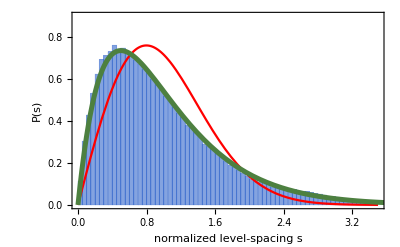

```mathematica
(* Generate Customized Plot *)
GCMMOrbEnergyLinearUnf=Histogram[AllSpacingsLinear,{0.05},"PDF",ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,3.5},{0,0.9}},
Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},FrameLabel->{Style["normalized level-spacing s",10,Bold,FontFamily->"Arial",Black],
Style["P(s)",10,Bold,FontFamily->"Arial",Black]},
Epilog->{{{Red,Thickness[0.005],Plot[pGOE[x],{x,0,3.5},PlotStyle->Directive[Red,Thick]][[1]]}},{Green,Thickness[0.005],Plot[pSP[x],{x,0,4},PlotStyle->Directive[RGBColor[0.3,0.5,0.25],Thickness[0.009]]][[1]]}}]
```

```mathematica
Export["C:\\Users\\Mehdi Ameri\\Desktop\\GCMMOrbEnergyLinearUnf.png",GCMMOrbEnergyLinearUnf,ImageResolution->300];
```

## Tracy-Widom

```mathematica
(*SELECT THE DATASET:AT OR GC*)

filePaths=FileNames["multimode_sample_*.csv","C:\\Users\\Mehdi Ameri\\Desktop\\MM-Results\\GC\\Orbital Energy Levels"];

Print["Total files found: ",Length[filePaths]];

(*EXTRACT THE ORIGINAL ORBITAL ENERGIES*)

spectra=Table[Module[{data,energies},data=Import[file,"CSV"];
energies=Cases[Rest[data][[All,5]],_?NumericQ];
If[Length[energies]>0,energies,$Failed]],{file,filePaths}];

(*REMOVE INVALID FILES*)

validSpectra=Select[spectra,ListQ];

Print["Valid spectra: ",Length[validSpectra]];

(*EXTRACT EXTREME EIGENVALUES*)

maxEigenvalues=Max/@validSpectra;

minEigenvalues=Min/@validSpectra;

Print["Number of maximum eigenvalues: ",Length[maxEigenvalues]];

Print["Number of minimum eigenvalues: ",Length[minEigenvalues]];

(*BASIC STATISTICS*)

Print["Maximum eigenvalue range (eV): ",MinMax[maxEigenvalues]];

Print["Minimum eigenvalue range (eV): ",MinMax[minEigenvalues]];
```

Total files found: 1000

Valid spectra: 1000

Number of maximum eigenvalues: 1000

Number of minimum eigenvalues: 1000

Maximum eigenvalue range (eV): {102.501,104.59}

Minimum eigenvalue range (eV): {-520.555,-519.464}

```mathematica
(*SELECT TRACY-WIDOM DISTRIBUTION*)
beta=1;
twDist=TracyWidomDistribution[beta];

(*THEORETICAL MEAN AND STANDARD DEVIATION*)

twMean=N[Mean[twDist]];
twSD=N[Sqrt[Variance[twDist]]];
Print["TW mean: ",twMean];
Print["TW standard deviation: ",twSD];
```

TW mean: -1.20653

TW standard deviation: 1.26798

```mathematica
zMax=N[(maxEigenvalues-Mean[maxEigenvalues])/StandardDeviation[maxEigenvalues]];

reflectedMin=-minEigenvalues;

zMin=N[(reflectedMin-Mean[reflectedMin])/StandardDeviation[reflectedMin]];

twStandardizedPDF[x_]:=twSD PDF[twDist,twMean+twSD x];

twStandardizedCDF[x_]:=CDF[twDist,twMean+twSD x];
```

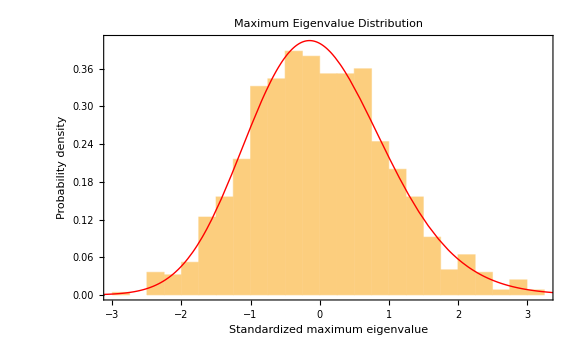

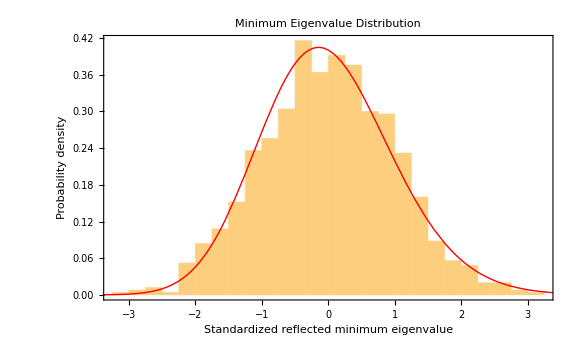

```mathematica
maxPlot=Show[Histogram[zMax,{0.25},"PDF"],Plot[twStandardizedPDF[x],{x,Min[zMax]-0.5,Max[zMax]+0.5},PlotStyle->{Red,Thick}],PlotLabel->"Maximum Eigenvalue Distribution",Frame->True,FrameLabel->{"Standardized maximum eigenvalue","Probability density"},PlotLegends->{"Numerical data","Tracy-Widom"},ImageSize->Large];

(*MINIMUM EIGENVALUES*)

minPlot=Show[Histogram[zMin,{0.25},"PDF"],Plot[twStandardizedPDF[x],{x,Min[zMin]-0.5,Max[zMin]+0.5},PlotStyle->{Red,Thick}],PlotLabel->"Minimum Eigenvalue Distribution",Frame->True,FrameLabel->{"Standardized reflected minimum eigenvalue","Probability density"},PlotLegends->{"Numerical data","Tracy-Widom"},ImageSize->Large];

maxPlot
minPlot
```

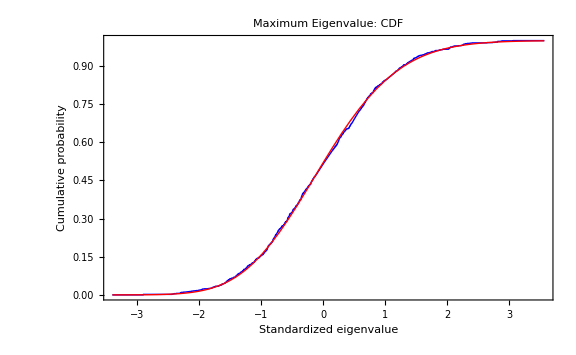

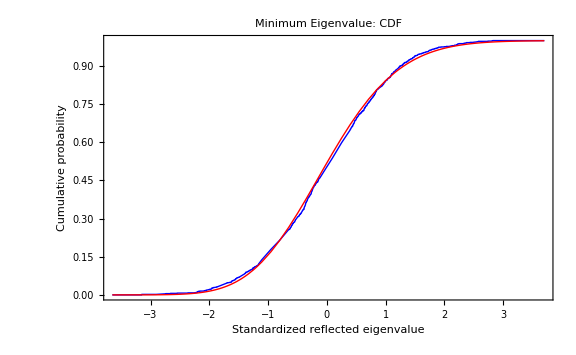

```mathematica
(*5. CUMULATIVE DISTRIBUTION COMPARISON*)

empiricalCDF[data_List]:=Module[{sorted,n},sorted=Sort[data];
n=Length[sorted];
Interpolation[Join[{{First[sorted]-10^-8,0}},Transpose[{sorted,Range[n]/n}]],InterpolationOrder->0]];

(*MAXIMUM EIGENVALUES*)

maxEmpCDF=empiricalCDF[zMax];

maxCDFPlot=Show[Plot[maxEmpCDF[x],{x,Min[zMax]-0.5,Max[zMax]+0.5},PlotStyle->{Blue,Thick}],Plot[twStandardizedCDF[x],{x,Min[zMax]-0.5,Max[zMax]+0.5},PlotStyle->{Red,Thick}],PlotLabel->"Maximum Eigenvalue: CDF",Frame->True,FrameLabel->{"Standardized eigenvalue","Cumulative probability"},PlotLegends->{"Numerical data","Tracy-Widom"},ImageSize->Large];

(*MINIMUM EIGENVALUES*)

minEmpCDF=empiricalCDF[zMin];

minCDFPlot=Show[Plot[minEmpCDF[x],{x,Min[zMin]-0.5,Max[zMin]+0.5},PlotStyle->{Blue,Thick}],Plot[twStandardizedCDF[x],{x,Min[zMin]-0.5,Max[zMin]+0.5},PlotStyle->{Red,Thick}],PlotLabel->"Minimum Eigenvalue: CDF",Frame->True,FrameLabel->{"Standardized reflected eigenvalue","Cumulative probability"},PlotLegends->{"Numerical data","Tracy-Widom"},ImageSize->Large];

maxCDFPlot
minCDFPlot
```

```mathematica
KSdistance[data_List,theoreticalCDF_]:=Module[{sorted,n,i,dPlus,dMinus},sorted=Sort[data];
n=Length[sorted];
dPlus=Max[Table[i/n-theoreticalCDF[sorted[[i]]],{i,n}]];
dMinus=Max[Table[theoreticalCDF[sorted[[i]]]-(i-1)/n,{i,n}]];
Max[dPlus,dMinus]];

maxKS=KSdistance[zMax,twStandardizedCDF];

minKS=KSdistance[zMin,twStandardizedCDF];

Print["Maximum eigenvalue KS distance: ",maxKS];

Print["Minimum eigenvalue KS distance: ",minKS];
```

Maximum eigenvalue KS distance: 0.0230868

Minimum eigenvalue KS distance: 0.0271438

```mathematica
Print["Number of geometries: ",Length[validSpectra]];

Print["Orbital counts per geometry: ",DeleteDuplicates[Length/@validSpectra]];

Print["Maximum eigenvalue statistics:"];
Print["Mean = ",N[Mean[maxEigenvalues]]];
Print["SD = ",N[StandardDeviation[maxEigenvalues]]];

Print["Minimum eigenvalue statistics:"];
Print["Mean = ",N[Mean[minEigenvalues]]];
Print["SD = ",N[StandardDeviation[minEigenvalues]]];

Print["TW beta = ",beta];
Print["TW mean = ",twMean];
Print["TW SD = ",twSD];
```

Number of geometries: 1000

Orbital counts per geometry: {316}

Maximum eigenvalue statistics:

Mean = 103.516

SD = 0.349845

Minimum eigenvalue statistics:

Mean = -520.005

SD = 0.171675

TW beta = 1

TW mean = -1.20653

TW SD = 1.26798

```mathematica
(* ============================================*)(*7. SKEWNESS AND KURTOSIS COMPARISON*)(* ============================================*)Print["TRACY-WIDOM THEORETICAL VALUES"];

Print["TW1 skewness = ",N[Skewness[twDist]]];

Print["TW1 kurtosis = ",N[Kurtosis[twDist]]];

Print[""];

Print["MAXIMUM EIGENVALUE DISTRIBUTION"];

Print["Skewness = ",N[Skewness[zMax]]];

Print["Kurtosis = ",N[Kurtosis[zMax]]];

Print[""];

Print["MINIMUM EIGENVALUE DISTRIBUTION"];

Print["Skewness = ",N[Skewness[zMin]]];

Print["Kurtosis = ",N[Kurtosis[zMin]]];
```

TRACY-WIDOM THEORETICAL VALUES

TW1 skewness = 0.293465

TW1 kurtosis = 3.16524

MAXIMUM EIGENVALUE DISTRIBUTION

Skewness = 0.208917

Kurtosis = 2.93904

MINIMUM EIGENVALUE DISTRIBUTION

Skewness = 0.0266169

Kurtosis = 2.92594